## Functions and PSF

### MyConvertFileToInputer (cc)

```mathematica
(*Input: An inported datafile from Particle Tracking code, unlinked, like "redspots.dat". Positions {{X,Y},...}...} at all times. 

Blank times get a spot added at centroid {15,15}, which should just be dark background
*)
MyConvertFileToInputer[spotsdata_] := Module[{step0,step1,step2,step3},
step0= spotsdata/.{}->{{15,15}};
step1={{#}}&/@#&/@step0; 
step2 = Table[Prepend[#,i]&/@step1⟦i⟧,{i,1,Length@spotsdata,1}];
step3=Table[Table[Prepend[step2⟦frame,spot⟧,spot],{spot,1,Length@step2⟦frame⟧,1}],{frame,1,Length@step2,1}]
]
```

### MyParticleFitter (OG)

```mathematica
(* input not tracked, contains multiple information from component measurments. intensity centroid is the first component
   fitted result is appended after the component measurments 
    output list has 3 components
    1. component measurements + fit results
    2. fit centroid in the cropped data
    3. cropped data *)
MyParticleFitter[myColMovie_,channel_,mySpots_,pad_,avgFrameN_]:=Module[{myTrimSize,myAllParametersEach,myTrimImgs,myOrigins,tempTime,tempCenter,frameShift,myImgs,myData,myFits,tempData3D,myFit,myPos,myPosImgCoordn,myAbsPos,myIntBG,mySigma,myPos90Conf,myPos90ConfImgCoordn,myAbsPos90Conf,myIntBG90Conf,mySigma90Conf,myParametersAll,my90ConfAll,myFitData,CC,A,x0,a,y0,b,x,y},

myTrimSize=2*pad+1;
frameShift=Ceiling[avgFrameN/2];

Table[
{myTrimImgs,myOrigins}=Table[
tempTime=mySpots⟦frame,spot,2⟧;
tempCenter=Ceiling[mySpots⟦frame,spot,3,1⟧];
{myImgs=ImageTrim[myColMovie⟦channel,tempTime+frameShift-1⟧,{tempCenter-pad,tempCenter+pad-0.1}],
myOrigins=tempCenter-pad-1}
,{spot,1,Length[mySpots⟦frame⟧],1}]//Transpose;
myData=ImageData/@myTrimImgs;
myFits=Table[
tempData3D=Flatten[MapIndexed[{#2⟦2⟧,#2⟦1⟧,#1}&,myData⟦i⟧,{2}],1];
Clear[CC,A,x0,a,y0,b,x,y];
myFit=NonlinearModelFit[tempData3D,CC+A E^(-(x-x0)^2/(2 a^2)-(y-y0)^2/(2 b^2)),
{{CC,0.01},{A,tempData3D⟦(2*pad*(pad+1)+1),3⟧},{x0,pad+1},{a,1},{y0,pad+1},{b,1}},{x,y}];
myFit[{"ParameterTable","ANOVATable","ParameterConfidenceIntervals"}]
,{i,1,Length@myData,1}];

(* Rearrange the parameters *)
myPos=myFits⟦All,1,1,1,{4,6},2⟧;
myPosImgCoordn={myPos⟦All,1⟧-0.5,myTrimSize-myPos⟦All,2⟧+0.5}//Thread;
myAbsPos=myPosImgCoordn+myOrigins;
myIntBG=myFits⟦All,1,1,1,{3,2},2⟧;
mySigma=myFits⟦All,1,1,1,{5,7},2⟧;
myPos90Conf=myFits⟦All,3,{3,5}⟧;
myPos90ConfImgCoordn={myPos90Conf⟦All,2⟧-0.5,myTrimSize-myPos90Conf⟦All,1⟧+0.5}//Thread;
myPos90ConfImgCoordn⟦All,2,{1,2}⟧=myPos90ConfImgCoordn⟦All,2,{2,1}⟧;
myAbsPos90Conf=myPos90ConfImgCoordn+myOrigins;
myIntBG90Conf=myFits⟦All,3,{2,1}⟧;
mySigma90Conf=myFits⟦All,3,{4,6}⟧;
myParametersAll=Thread@{myAbsPos,myIntBG,mySigma};
my90ConfAll=Thread@{myAbsPos90Conf,myIntBG90Conf,mySigma90Conf};

(* Output the paramters *)
myAllParametersEach={Thread@{mySpots⟦frame⟧,myParametersAll,my90ConfAll},myPos,myData};
myAllParametersEach⟦1⟧=Append[Append[#⟦1⟧,#⟦2⟧],#⟦3⟧]&/@myAllParametersEach⟦1⟧;
myAllParametersEach

,{frame,1,Length@mySpots,1}]//Transpose
]
```

### MyFilterFitOutliers (cc)

```mathematica
(* This function removes outliers based on intensity, 90% confidence interval of xy positions and the size of sigma 
NOTE: 
This fxn was modified to retain the image data and centroid info;

INPUT: the output of MyParticleFitter 
*)

MyFilterFitOutlier[mySpotsFit_,maxDxy_,maxSig_]:=Module[{idxInt,idxX90Conf,idxY90Conf,idxSigX,idxSigY,idxOutliers},
idxInt=Position[mySpotsFit⟦1,All,All,4,2,1⟧,x_/;x<0||x>2];
idxX90Conf=Position[(Differences/@#&/@mySpotsFit⟦1,All,All,5,1,1⟧)⟦All,All,1⟧,x_/;x>maxDxy];
idxY90Conf=Position[(Differences/@#&/@mySpotsFit⟦1,All,All,5,1,2⟧)⟦All,All,1⟧,x_/;x>maxDxy];
idxSigX=Position[mySpotsFit⟦1,All,All,4,3,1⟧,x_/;Abs@x>maxSig];
idxSigY=Position[mySpotsFit⟦1,All,All,4,3,2⟧,x_/;Abs@x>maxSig];
idxOutliers=Union[idxInt,idxX90Conf,idxY90Conf,idxSigX,idxSigY];
Delete[#,idxOutliers]&/@mySpotsFit
]
```

### Filter Out Blue Red Spots that have no Green

```mathematica
BandPass[img_,{lo_,hi_}]:=Module[{imgb,imgc},
imgb=ImageConvolve[img,GaussianMatrix[{hi,lo}]];
(*imgc=ImageConvolve[img,BoxMatrix[hi]/(2 hi+1)^2];*)
imgc=ImageConvolve[img,DiskMatrix[hi]/(Plus@@Plus@@DiskMatrix[hi])];
ImageSubtract[imgb,imgc]
]
```

```mathematica
(*BandPass[-Graphics-,{1,12}]//ImageAdjust*)
```

```mathematica
FindParticlesWeighted[img_,{lo_,hi_},max_,th_,imgmask_,{small_,large_}]:=Module[{imgb,imgc,pos},
imgb=BandPass[img,{lo,hi}];
imgc=SelectComponents[ImageMultiply[imgb//Binarize[#, max th]&,imgmask],{"Count","AdjacentBorderCount"},small<#1<large&&#2==0&];
ComponentMeasurements[ImageMultiply[img,imgc],{"IntensityCentroid"}]⟦All,2,1⟧
(*{Show[img,Graphics[{Color,Circle[#,hi 1.5]&/@(pos=ComponentMeasurements[imgc,{"Centroid"}][[All,2,1]])}]],pos}*)
]
```

```mathematica
FindParticlesWeightedMask[img_,{lo_,hi_},max_,th_,imgmask_,{small_,large_}]:=Module[{imgb,imgc,pos},
imgb=BandPass[img,{lo,hi}];
imgc=SelectComponents[ImageMultiply[imgb//Binarize[#, max th]&,imgmask],{"Count","AdjacentBorderCount"},small<#1<large&&#2==0&]
]
```

```mathematica
imgmask=Table[1,{i,1,15,1},{j,1,15,1}]//Image;
```

### ErrorPropagator

```mathematica
MyErrorPropagator[f_,xmean_,ymean_,zmean_,σx_,σy_,σz_]:=Evaluate[((D[f,x]^2 σx^2+D[f,y]^2 σy^2+D[f,z]^2 σz^2)^(1/2))]/.{x-> xmean,y-> ymean,z-> zmean}
```

### Get Trim Peak Intensity with Fixed Sigma

```mathematica
GetTrimPeakIntFixedSigma[myMeanTrim_,sigma_]:=Module[{myTrim=myMeanTrim,myTrimtempData,myTrimtempPos,myTrimtempGauss},
myTrimtempData=Table[ImageData[myTrim[[spot]]],{spot,1,Length@myTrim,1}];
myTrimtempPos=Table[Flatten[MapIndexed[{#2[[2]]1,#2[[1]]1,#1}&,myTrimtempData[[i]],{2}],1],{i,1,Length@myTrimtempData}];
Table[myTrimtempGauss=Quiet[Table[NonlinearModelFit[myTrimtempPos[[i]],CC+A E^(-(x-x0)^2/(2 sigma^2)-(y-y0)^2/(2 sigma^2)),
{{CC,0},{A,0},{x0,8},{y0,8}},{x,y}],{i,1,Length@myTrimtempPos,1}]];
{A /.myTrimtempGauss[[fit]]["BestFitParameters"]},{fit,1,Length@myTrimtempPos,1}]]
```

### Get Integrated Trim Peak Intensity and Sigma and Peak Intensity 90% Confidence Interval Error Propagated

```mathematica
GetTrimPeakIntSigmaIntergrate90Conf[myMeanTrim_]:=Module[{myTrim=myMeanTrim,myTrimtempData,myTrimtempPos,myTrimtempGauss},
myTrimtempData=Table[ImageData[myTrim[[spot]]],{spot,1,Length@myTrim,1}];
myTrimtempPos=Table[Flatten[MapIndexed[{#2[[2]]1,#2[[1]]1,#1}&,myTrimtempData[[i]],{2}],1],{i,1,Length@myTrimtempData}];
Table[myTrimtempGauss=Quiet[Table[NonlinearModelFit[myTrimtempPos[[i]],CC+A E^(-(x-x0)^2/(2 a^2)-(y-y0)^2/(2 b^2)),
{{CC,0},{A,0},{x0,8},{a,1},{y0,8},{b,1}},{x,y}],{i,1,Length@myTrimtempPos,1}]];
Flatten@{A √(2 π) a/.myTrimtempGauss[[fit]]["BestFitParameters"],MyErrorPropagator[x y,A/.myTrimtempGauss[[fit]]["BestFitParameters"],a/.myTrimtempGauss[[fit]]["BestFitParameters"],1,Differences@myTrimtempGauss[[fit]]["ParameterConfidenceIntervals"][[2]],Differences@myTrimtempGauss[[fit]]["ParameterConfidenceIntervals"][[4]],1]},{fit,1,Length@myTrimtempPos,1}]]
```

### MyNumString

```mathematica
MyNumString[myn_,L_]:=If[myn>10^L-1,IntegerString[myn,10,L+1],IntegerString[myn,10,L]];
```

```mathematica
MyNumString[30,3]
```

030

### BandPass

```mathematica
BandPass[img_,{lo_,hi_}]:=Module[{imgb,imgc},
imgb=ImageConvolve[img,GaussianMatrix[{hi,lo}]];
(*imgc=ImageConvolve[img,BoxMatrix[hi]/(2 hi+1)^2];*)
imgc=ImageConvolve[img,DiskMatrix[hi]/(Plus@@Plus@@DiskMatrix[hi])];
ImageSubtract[imgb,imgc]
]
```

```mathematica
(*BandPass[-Graphics-,{1,12}]//ImageAdjust*)
```

### FindParticles (updated to remove adjacentbordercounts)

```mathematica
FindParticlesWeighted[img_,{lo_,hi_},max_,th_,imgmask_,{small_,large_}]:=Module[{imgb,imgc,pos},
imgb=BandPass[img,{lo,hi}];
imgc=SelectComponents[ImageMultiply[imgb//Binarize[#, max th]&,imgmask],{"Count","AdjacentBorderCount"},small<#1<large&&#2==0&];
ComponentMeasurements[ImageMultiply[img,imgc],{"IntensityCentroid"}]⟦All,2,1⟧
(*{Show[img,Graphics[{Color,Circle[#,hi 1.5]&/@(pos=ComponentMeasurements[imgc,{"Centroid"}][[All,2,1]])}]],pos}*)
]
```

```mathematica
FindParticlesWeightedMask[img_,{lo_,hi_},max_,th_,imgmask_,{small_,large_}]:=Module[{imgb,imgc,pos},
imgb=BandPass[img,{lo,hi}];
imgc=SelectComponents[ImageMultiply[imgb//Binarize[#, max th]&,imgmask],{"Count","AdjacentBorderCount"},small<#1<large&&#2==0&]
]
```

### PairConnect2 (still one small error, but doesn’t seem to mess up stuff)

```mathematica
PairConnect2[{ticker_,anolist1t_},list2t_,dist_]:=Module[{newticker,finalticker,list1,list2,flag,out,newTracks,mypos,myind,myl,out2,out3},
newticker=ticker;
list1=Sort[anolist1t,#1⟦2,1⟧<#2⟦2,1⟧&];
list2=Sort@list2t;
flag=0;
out=Table[
myind=1;
mypos=list2⟦myind,1⟧;
Reap[
While[(*list1⟦m,2,1⟧-dist≤ *)mypos≤list1⟦m,2,1⟧+dist &&myind≤ Length@list2,
If[EuclideanDistance[list2⟦myind⟧,list1⟦m,2⟧]≤dist,
Sow[{list1⟦m,1⟧,list2⟦myind⟧}];
list2=Delete[list2,myind];
myind=myind-1;
flag=flag+1;
];
myind=myind+1;
If[Length@list2>0&&myind≤Length@list2,mypos=list2⟦myind,1⟧,m=Length@list1];
];
],
{m,1,Length@list1,1}];
out2=DeleteCases[out⟦All,2⟧//Flatten[#,2]&,Null];
If[Length@list2>0,
finalticker=newticker+Length[list2];
newTracks={Range[newticker+1,finalticker],list2}//Transpose;
out3=Join[out2,newTracks];,
finalticker=newticker;
out3=out2;
];
{finalticker,out3}
]
```

### PairConnect3 (Connect a dot in frame(n) to the nearest dot in frame(n-1) which is less than the determined jumping distance > there is no conversion, but diversion)

```mathematica
(* This function is used with LinkTracks or LinkTracks2

	A cordinate of each dots at frame# N+1 is compared with dots at frame# N by Table function
	Those dots located +/- "dist_" are listed as "potentialDots"
	If the nearest dots in "potentialDots" is actually less than "dist_"
	the track number of the dot is given to the current dot at frame# N+1
	This will ensure there is no conversion in tracks
	If there is no dots closeby in frame #N, the current dot gets the new track number

		list1⟦1⟧: the latest (biggest) track number being used (newticker)
		list1⟦2⟧: the list of cordinate of points with a track number at frame# N 
		list2:    the list of cordinate of points at frame# N+1

	 out:      the list of cordinate of points with a track number at frame# N+1
 *)
```

```mathematica
PairConnect3[{ticker_,anolist1t_},list2t_,dist_]:=Module[{newticker,list1,list2,out,mypos},
newticker=ticker;
list1=Sort[anolist1t,#1⟦2,1⟧<#2⟦2,1⟧&];
list2=Sort@list2t;
out=Table[mypos=list2⟦myi⟧;
potentialDots=Cases[list1,x_/;mypos⟦1⟧-dist<x⟦2,1⟧<mypos⟦1⟧+dist&&mypos⟦2⟧-dist<x⟦2,2⟧<mypos⟦2⟧+dist];
If[potentialDots=={},
newticker+=1;out={newticker,mypos};,
potentialDot=Flatten[Cases[potentialDots,x_/;x⟦2⟧==Flatten@Nearest[potentialDots⟦All,2⟧,mypos]],1];
	If[EuclideanDistance[mypos,potentialDot⟦2⟧]>dist,
	newticker+=1;out={newticker,mypos};,out={potentialDot⟦1⟧,mypos};]];out,{myi,1,Length@list2,1}];
{newticker,out}
]
```

### PairConnect4 (PairConnect3 + removing diversion)

```mathematica
(* This function is used with LinkTracks or LinkTracks2

	After connecting all dots at frame# N+1 to dots at frame# N
	finding redundant track numbers by using RedundantTrack function

	RedundantTrack[{1,2,5,1,6,7,2,2,5}]
	{{1,2,5,6,7},{1,2,5},{{{1},{4}},{{2},{7},{8}},{{3},{9}}}}

	redundant track numbers means track gets split at frame# N+1
	in order to avoid this, choosing the nearest point and assign a new track number to the other points
*)
```

```mathematica
RedundantTrack[list_,test_: Identity]:=Composition[{#⟦1⟧,#⟦2⟧,Position[list,#]&/@#⟦2⟧}&,{#⟦All,1⟧,DeleteCases[#,{_}]⟦All,1⟧}&,GatherBy[#,test]&][list]
```

```mathematica
PairConnect4[{ticker_,anolist1t_},list2t_,dist_]:=Module[{newticker,list1,list2,out,mypos,myRedundant,null,tempOriginalPoint,tempNewPoints,tempTruePoint,tempOutlierPointPosi},
newticker=ticker;
list1=Sort[anolist1t,#1⟦2,1⟧<#2⟦2,1⟧&];
list2=Sort@list2t;
out=Table[mypos=list2⟦myi⟧;
potentialDots=Cases[list1,x_/;mypos⟦1⟧-dist<x⟦2,1⟧<mypos⟦1⟧+dist&&mypos⟦2⟧-dist<x⟦2,2⟧<mypos⟦2⟧+dist];
If[potentialDots=={},
newticker+=1;out={newticker,mypos};,
potentialDot=Flatten[Cases[potentialDots,x_/;x⟦2⟧==Flatten@Nearest[potentialDots⟦All,2⟧,mypos]],1];
	If[EuclideanDistance[mypos,potentialDot⟦2⟧]>dist,
	newticker+=1;out={newticker,mypos};,out={potentialDot⟦1⟧,mypos};]];out,{myi,1,Length@list2,1}];
myRedundant=RedundantTrack[out⟦All,1⟧];
null=Table[
tempOriginalPoint=Extract[list1,Position[list1⟦All,1⟧,myRedundant⟦2,myj⟧]];
tempNewPoints=out⟦Flatten@myRedundant⟦3,myj⟧⟧;
tempTruePoint=Position[tempNewPoints,Flatten@Nearest[tempNewPoints⟦All,2⟧,tempOriginalPoint⟦1,2⟧]]⟦1,1⟧;
tempOutlierPointPosi=Delete[myRedundant⟦3,myj⟧,tempTruePoint]//Flatten;
Range[newticker+1,newticker+Length@tempOutlierPointPosi];
out⟦tempOutlierPointPosi,1⟧=Range[newticker+1,newticker+Length@tempOutlierPointPosi];
newticker=newticker+Length@tempOutlierPointPosi;
,{myj,1,Length@myRedundant⟦2⟧,1}];
{newticker,out}
]
```

### LinkTracks

```mathematica
LinkTracks[testgreenP_,dist_]:=Module[{list1,list2,listResult,listResultFrame,listResultTrack},
list1=Thread@{Range@Length@testgreenP⟦1⟧,Sort@testgreenP⟦1⟧};
list1={Length@list1,list1};
list2=testgreenP⟦2;;⟧;
listResult=FoldList[PairConnect4[#1,#2,dist]&,list1,list2];
listResultFrame=Table[Insert[listResult⟦i⟧,i,Table[{2,j,2,1},{j,1,Length@listResult⟦i,2⟧,1}]],{i,1,Length@listResult,1}];
listResultTrack=SplitBy[listResultFrame⟦All,2⟧//Flatten[#,1]&//Sort,First];
{listResultFrame,listResultTrack}
]
```

### LinkTracks2

```mathematica
(* get rid of tracks which last only 1 or 2 frame(s) and re-assign consecutive track numbers *)
```

```mathematica
LinkTracks2[testgreenP_,dist_]:=Module[{list1,list2,listResult,listResultFrame,listResultTrack,listResultTrackL},
list1=Thread@{Range@Length@testgreenP⟦1⟧,Sort@testgreenP⟦1⟧};
list1={Length@list1,list1};
list2=testgreenP⟦2;;⟧;
listResult=FoldList[PairConnect4[#1,#2,dist]&,list1,list2];
listResultFrame=Table[Insert[listResult⟦i⟧,i,Table[{2,j,2,1},{j,1,Length@listResult⟦i,2⟧,1}]],{i,1,Length@listResult,1}];
listResultTrack=SplitBy[listResultFrame⟦All,2⟧//Flatten[#,1]&//Sort,First];
listResultTrackL=Extract[listResultTrack,Position[Length/@listResultTrack,x_/;x>2]];
listResultTrackL⟦All,All,1⟧=Range@Length@listResultTrackL;
listResultTrackL
]
```

### Relinking

```mathematica
(* Only the longest path will be taken for the last frame if the track split in the middle *)
```

```mathematica
Relinking[sortedbyframe_,sortedbytrack_,gap_,distance_]:=Module[{ftrackList,ltrackList,linkinglist,mytrack,mytrackN,myt,mypos,newrange,flag,targetFrame,targetTracks,candidateTracks,closestTrack,out,newlinkinglist,newsortedbytrack,oldtrackN,newtrackN,newsortedbyframe,oldtrackPos},

(* extracting the begining and the ending of all tracks *)
ftrackList=SortBy[(First/@sortedbytrack⟦All⟧),{#⟦2,1⟧,#⟦1⟧}&];
ftrackList=DeleteCases[ftrackList,x_/;x⟦2,1⟧≤2];
ltrackList=SortBy[Last/@sortedbytrack⟦All⟧,{#⟦2,1⟧,#⟦1⟧}&];

(* relinking tracks and making a list*)
linkinglist={};
Table[
mytrack=ftrackList⟦i⟧;
mytrackN=mytrack⟦1⟧;
myt=mytrack⟦2,1⟧;
mypos=mytrack⟦2,2;;3⟧;
newrange=Range[myt-gap-1,myt-2,1]//Reverse;
flag=0;
Table[
targetFrame=newrange⟦j⟧;
If[flag==0,
targetTracks=Extract[ltrackList,Position[ltrackList⟦All,2,1⟧,targetFrame]];
candidateTracks=Select[targetTracks,EuclideanDistance[#⟦2,2;;3⟧,mypos]<distance&];
If[Length[candidateTracks]>0,
If[Length[candidateTracks]==1,out={mytrackN,candidateTracks⟦1,1⟧};ltrackList⟦mytrackN,1⟧=candidateTracks⟦1,1⟧;flag=1;,
closestTrack=Extract[candidateTracks,Position[x=EuclideanDistance[#,mypos]&/@candidateTracks⟦All,2,2;;3⟧,Min[x]]];
out={mytrackN,closestTrack⟦1,1⟧};ltrackList⟦mytrackN,1⟧=closestTrack⟦1,1⟧;flag=1;],out={};flag=0]];
,{j,1,Length[newrange],1}];
linkinglist=Append[linkinglist,out];
,{i,1,Length[ftrackList],1}];

(* convert old track numbers to new track numbers in "sortedbytrack" and "sortedbyframe" *)
newlinkinglist=DeleteCases[linkinglist,{}];
newsortedbytrack=sortedbytrack;
newsortedbyframe=sortedbyframe;
Table[
oldtrackN=newlinkinglist⟦i,1⟧;
newtrackN=newlinkinglist⟦i,2⟧;
newsortedbytrack⟦oldtrackN,All,1⟧=newtrackN;
oldtrackPos=Position[newsortedbyframe⟦All,2,All,1⟧,oldtrackN]//Flatten//Riffle[#,{2,1}]&//Append[#,1]&//Partition[#,4]&;
newsortedbyframe=ReplacePart[newsortedbyframe,oldtrackPos -> newtrackN];,
{i,1,Length[newlinkinglist],1}];
newsortedbytrack=newsortedbytrack//Flatten[#,1]&//Sort//SplitBy[#,First]&;

{newsortedbyframe,newsortedbytrack,newlinkinglist}
]
```

```mathematica
(*{sortedbyframe,sortedbytrack}=LinkTracks[testgreenP,1];*)
```

### BeadsFitting

```mathematica
BeadsFitting[myRefBeadsImg_,myPosGuess_,pad_]:=
Module[{myTrimSize,myTrimImgs,myOrigins,tempCenter,myImgs,myData,myFits,tempData3D,myFit,CC,A,x,x0,a,y,y0,b,myPos,myPosImgCoordn,myAbsPos},

myTrimSize=2*pad+1;
{myTrimImgs,myOrigins}=Table[
tempCenter=Ceiling[myPosGuess⟦i⟧];
{myImgs=ImageTrim[myRefBeadsImg,{tempCenter-pad,tempCenter+pad-0.1}],
myOrigins=tempCenter-pad-1}
,{i,1,Length[myPosGuess],1}]//Transpose;
myData=ImageData/@myTrimImgs;
myFits=Table[
tempData3D=Flatten[MapIndexed[{#2⟦1⟧,#2⟦2⟧,#1}&,myData⟦i⟧,{2}],1];
Clear[CC,A,x0,a,y0,b,x,y];
myFit=NonlinearModelFit[tempData3D,CC+A E^(-(x-x0)^2/(2 a^2)-(y-y0)^2/(2 b^2)),
{{CC,0},{A,tempData3D⟦(2*pad*(pad+1)+1),3⟧},{x0,pad+1},{a,1},{y0,pad+1},{b,1}},{x,y}];
myFit[{"ParameterTable","ANOVATable","ParameterConfidenceIntervals"}]
,{i,1,Length[myData],1}];
myPos=myFits⟦All,1,1,1,{4,6},2⟧;
myPosImgCoordn={myPos⟦All,2⟧-0.5,myTrimSize-myPos⟦All,1⟧+0.5}//Thread;
myAbsPos=myPosImgCoordn+myOrigins
]
```

```mathematica
BeadsSorting[myRedAbsPos_,myGreenAbsPos_,dist_]:=
Module[{myRedAbsPosSort,distanceOriginal,idx,myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw},

myRedAbsPosSort=Nearest[myRedAbsPos,myGreenAbsPos]//Flatten[#,1]&;
distanceOriginal=EuclideanDistance@@@Thread@{myGreenAbsPos,myRedAbsPosSort};
idx=Position[distanceOriginal,x_/;x>dist];
{myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw}=Delete[#,idx]&/@{myRedAbsPosSort,myGreenAbsPos,distanceOriginal}
]
```

```mathematica
BeadsTransform[myRedAbsPos_,myGreenAbsPos_,dist_]:=
Module[{myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw,myTfFuncError,myTfFunc,myRedCorrPos,distanceCorrected},

{myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw}=BeadsSorting[myRedAbsPos,myGreenAbsPos,dist];
{myTfFuncError,myTfFunc}=FindGeometricTransform[myGreenAbsPos4Calc,myRedAbsPos4Calc];
myRedCorrPos=myTfFunc[myRedAbsPos4Calc];
distanceCorrected=EuclideanDistance@@@Thread@{myGreenAbsPos4Calc,myRedCorrPos};
{myTfFuncError,myTfFunc,distanceRaw,distanceCorrected}

]
```

```mathematica
BeadsCheck[myRedAbsPos_,myGreenAbsPos_,dist_]:=
Module[{myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw,myRedCorrPos,distanceCorrected},

{myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw}=BeadsSorting[myRedAbsPos,myGreenAbsPos,dist];
myRedCorrPos=myTfFunc[myRedAbsPos4Calc];
distanceCorrected=EuclideanDistance@@@Thread@{myGreenAbsPos4Calc,myRedCorrPos};
Insert[{distanceRaw,distanceCorrected}//Transpose,{"Distance Before Correction","Distance After Correction"},1]//TableForm
]
```

### FindOverlapDistance[track1,track2,τ] (measures average distance between two tracks when they overlap in time for at least time τ, otherwise outputs -1)

```mathematica
FindOverlapDist[track1_,track2_,τ_]:=Module[{t1,t2,ol,avgpos1,avgpos2},
(*makes tracks have form: t1={{track#,time1,x1,y1},{track#,time2,x2,y2} ...}*)
t1=track1//Flatten//Partition[#,7]&; 
t2=track2//Flatten//Partition[#,7]&;
(* The following just sorts by time rather than track # and splits. If the two tracks have overlapping time, then the split will contain 2 elements. Thus, DeleteCases eliminates all parts of the track that do not overlap. Finally, the Transpose command gives back a list of overlapping segments of tracks: {segment from t1, segment from t2} so the mean can be computed for each.*)
ol={t1⟦All,{2,1,3,4,5,6,7}⟧,t2⟦All,{2,1,3,4,5,6,7}⟧}//Flatten[#,1]&//Sort//SplitBy[#,First]&//DeleteCases[#,x_/;Length[x]<2]&;
If[Length[ol]>τ,{avgpos1,avgpos2}=(Mean/@(Transpose[ol]))⟦All,3;;4⟧;EuclideanDistance[avgpos1,avgpos2],-1]
]
```

### ColorLinker[gbtrackpairs, greentracklist, blueflag] → bluetracklist connected to greentracklist

```mathematica
(*This returns all green (or blue, specified by colorN = 1 for green and 2 for blue) elements of gbpairs whose blue (or green) element is a member of colorList  *)
ColorLinker[pairs_,colorList_,colorN_]:=Module[{},
Cases[pairs,x_/;MemberQ[colorList,x⟦If[colorN==1,2,1]⟧]]⟦All,colorN⟧//Union
]
```

### CrossPairFinder[gbtrackpairs] → list of green tracks gi connected to list of blue tracks bi : {{g1,b1}, {g2, b2}, ...}

```mathematica
CrossPairFinder[myGBpairs_]:=Module[{b1,g1,seed,myFlag=0,i},
Table[
seed={myGBpairs⟦i,1⟧}; (*seed with ith green element from pair list*)
While[myFlag==0 , 
b1=ColorLinker[myGBpairs,seed,2]//Union; (*bluelist b1 connected to greenlist seed *)
g1=ColorLinker[myGBpairs,b1,1]//Union; (*greenlist g1 connected to bluelist b1*)
If[g1==seed,myFlag=1, seed=g1] (*exit if greenlist g1 is the same as seed; if not, g1 becomes new seed*)
];
myFlag=0; (*repeat loop for all possible green seeds*)
{g1,b1},{i,1,Length[myGBpairs],1}]//Union
]
```

### ConnectByColor

```mathematica
Connect2Colors[track1_,track2_,minOverlapTime_,maxOverlapDistance_]:=Module[{idxTrack1,idxTrack2,myAllLink,tempTrack1,tempTrack2,myLinkList,newTrack1,newTrack2,myMergedTrack,bigTrack1,bigTrack2},
	(*Getting color index assuming the tracks have never been connected with any other colors*)
idxTrack1=track1⟦1,1,3⟧;
idxTrack2=track2⟦1,1,3⟧;
	(*Creating linking pair list*)
myAllLink=Table[
tempTrack1=track1⟦i⟧;
tempTrack2=track2⟦j⟧;
FindOverlapDist[tempTrack1,tempTrack2,minOverlapTime],{i,1,Length@track1,1},{j,1,Length@track2,1}];
myLinkList=CrossPairFinder[Position[myAllLink,x_/;0≤x<maxOverlapDistance]];
	(*Preparing output track*)
newTrack1=track1;
newTrack2=track2;
	(*Connecting tracks*)
Table[
myMergedTrack={track1⟦myLinkList⟦i,1⟧⟧,track2⟦myLinkList⟦i,2⟧⟧}//Flatten[#,2]&//SortBy[#,#⟦2,1⟧&]&//SplitBy[#,#⟦2,1⟧&]&;

bigTrack1=(If[Length[#]==2, Cases[#,x_/;x⟦3⟧==idxTrack1],If[Length[#]==1, #,{}]]&/@myMergedTrack);  (*Note that this automatically deletes times where three or more points appears at once*)
bigTrack1=DeleteCases[bigTrack1,x_/;Length@x>1]//Flatten[#,1]&;(*Note that this automatically deletes times where there is overlap in multiple tracks in track1*)
bigTrack1⟦All,1⟧=myLinkList⟦i,1,1⟧; (*Choose to label big track as lowest #'d track1*)
bigTrack1⟦All,3⟧=idxTrack1+idxTrack2;(*Change color index to two colors from one color*)
newTrack1⟦myLinkList⟦i,1,1⟧⟧=bigTrack1; 
If[Length@myLinkList⟦i,1⟧>1,newTrack1⟦myLinkList⟦i,1,2;;⟧⟧={}];
(*lowest # track1 that should be linked is replaced with bigTrack1; others become {};*)

bigTrack2=(If[Length[#]==2, Cases[#,x_/;x⟦3⟧==idxTrack2],If[Length[#]==1, #,{}]]&/@myMergedTrack);
bigTrack2=DeleteCases[bigTrack2,x_/;Length@x>1]//Flatten[#,1]&;
bigTrack2⟦All,1⟧=myLinkList⟦i,1,1⟧; 
bigTrack2⟦All,3⟧=idxTrack1+idxTrack2;
newTrack2⟦myLinkList⟦i,2,1⟧⟧=bigTrack2; 
If[Length@myLinkList⟦i,2⟧>1,newTrack2⟦myLinkList⟦i,2,2;;⟧⟧={}];

,{i,1,Length@myLinkList,1}];

newTrack1=DeleteCases[newTrack1,{}]; (*Now get rid of the {}*)
newTrack1⟦All,All,1⟧=Range@Length@newTrack1;(*renumber*)
newTrack2=DeleteCases[newTrack2,{}]; 
newTrack2⟦All,All,1⟧=Range@Length@newTrack2;

{newTrack1,newTrack2}
]
```

```mathematica
Connect2ColorsFor3[track1_,track2_,minOverlapTime_,maxOverlapDistance_,track1Color_]:=Module[{idxTrack1,idxTrack2,myAllLink,tempTrack1,tempTrack2,myLinkList,newTrack1,newTrack2,myMergedTrack,bigTrack1,bigTrack2},
myAllLink=Table[
tempTrack1=track1⟦i⟧;
tempTrack2=track2⟦j⟧;
FindOverlapDist[tempTrack1,tempTrack2,minOverlapTime],{i,1,Length@track1,1},{j,1,Length@track2,1}];
myLinkList=CrossPairFinder[Position[myAllLink,x_/;0≤x<maxOverlapDistance]];
newTrack1=track1;
Table[
myMergedTrack={track1⟦myLinkList⟦i,1⟧⟧,track2⟦myLinkList⟦i,2⟧⟧}//Flatten[#,2]&//SortBy[#,#⟦2,1⟧&]&//SplitBy[#,#⟦2,1⟧&]&;
bigTrack1=(If[Length[#]==2, Cases[#,x_/;x⟦3,track1Color⟧==1],If[Length[#]==1, #,{}]]&/@myMergedTrack);
bigTrack1=DeleteCases[bigTrack1,x_/;Length@x>1]//Flatten[#,1]&;
bigTrack1⟦All,1⟧=myLinkList⟦i,1,1⟧; 
idxTrack1=Total@track1⟦myLinkList⟦i,1⟧,1,3⟧;
idxTrack2=Total@track2⟦myLinkList⟦i,2⟧,1,3⟧;
bigTrack1⟦All,3⟧=(idxTrack1+idxTrack2)/.x_/;x>0->1;
newTrack1⟦myLinkList⟦i,1,1⟧⟧=bigTrack1; 
If[Length@myLinkList⟦i,1⟧>1,newTrack1⟦myLinkList⟦i,1,2;;⟧⟧={}];
,{i,1,Length@myLinkList,1}];
newTrack1=DeleteCases[newTrack1,{}]; 
newTrack1⟦All,All,1⟧=Range@Length@newTrack1;
newTrack2=Delete[track2,{#}&/@(myLinkList⟦All,2⟧//Flatten//Sort)]; 
newTrack2⟦All,All,1⟧=Range@Length@newTrack2;
{newTrack1,newTrack2}
]
```

```mathematica
Connect3Colors[trackr_,trackg_,trackb_,minOverlapTime_,maxOverlapDistance_]:=
Module[{trackgb,trackbAlone,trackrgb,newTrackr,trackbr,trackrAlone1,trackgbr,newTrackg,trackgr,trackrAlone2,trackbgr,newTrackb,dum},

{trackgb,trackbAlone}=Connect2ColorsFor3[trackg,trackb,minOverlapTime,maxOverlapDistance,2];
{trackrgb,dum}=Connect2ColorsFor3[trackr,trackgb,minOverlapTime,maxOverlapDistance,1];
{newTrackr,dum}=Connect2ColorsFor3[trackrgb,trackbAlone,minOverlapTime,maxOverlapDistance,1];

{trackbr,trackrAlone1}=Connect2ColorsFor3[trackb,trackr,minOverlapTime,maxOverlapDistance,3];
{trackgbr,dum}=Connect2ColorsFor3[trackg,trackbr,minOverlapTime,maxOverlapDistance,2];
{newTrackg,dum}=Connect2ColorsFor3[trackgbr,trackrAlone1,minOverlapTime,maxOverlapDistance,2];

{trackgr,trackrAlone2}=Connect2ColorsFor3[trackg,trackr,minOverlapTime,maxOverlapDistance,2];
{trackbgr,dum}=Connect2ColorsFor3[trackb,trackgr,minOverlapTime,maxOverlapDistance,3];
{newTrackb,dum}=Connect2ColorsFor3[trackbgr,trackrAlone2,minOverlapTime,maxOverlapDistance,3];

{newTrackr,newTrackg,newTrackb}
]
```

### ConnectTracks[tracks_,listConnectTracks, (renumberQ)]

```mathematica
ConnectTracks[tracksList_,listConnectTracks_]:=Module[{newTracksList},
newTracksList=tracksList;
newTracksList⟦listConnectTracks⟦2;;⟧,All,1⟧=tracksList⟦listConnectTracks⟦1⟧,1,1⟧;
newTracksList=SplitBy[Sort@Flatten[newTracksList,1],First];
newTracksList⟦All,All,1⟧=Range@Length@newTracksList;
newTracksList
]
```

```mathematica
ConnectTracks[tracksList_,listConnectTracks_,renumberQ_]:=Module[{newTracksList},
newTracksList=tracksList;
newTracksList⟦listConnectTracks⟦2;;⟧,All,1⟧=tracksList⟦listConnectTracks⟦1⟧,1,1⟧;
If[renumberQ,newTracksList=SplitBy[Sort@Flatten[newTracksList,1],First];
newTracksList⟦All,All,1⟧=Range@Length@newTracksList,newTracksList];
newTracksList
]
```

```mathematica
ConnectTracksFilled[tracksList_,listConnectTracks_]:=Module[{newTracksList,spotEnd,spotStart,missingNum,fillingNum,fillingPos,fillingSpots},
newTracksList=tracksList;
Table[
spotEnd=(Last@newTracksList⟦listConnectTracks⟦i⟧⟧)⟦2⟧;
spotStart=newTracksList⟦listConnectTracks⟦i+1⟧,1,2⟧;
missingNum=spotStart⟦1⟧-spotEnd⟦1⟧-1;
If[missingNum>0,
fillingNum=Range[spotEnd⟦1⟧+1,spotStart⟦1⟧-1];
fillingPos=Plus[#,spotEnd⟦{2,3}⟧]&/@Outer[Times,Range@missingNum/(missingNum+1),spotStart⟦{2,3}⟧-spotEnd⟦{2,3}⟧];
fillingSpots=ConstantArray[Last@newTracksList⟦listConnectTracks⟦i⟧⟧,missingNum];
fillingSpots⟦All,2⟧=Thread@{fillingNum,fillingPos}//Flatten//Partition[#,3]&;
newTracksList⟦listConnectTracks⟦i⟧⟧=PadRight[newTracksList⟦listConnectTracks⟦i⟧⟧,Length@newTracksList⟦listConnectTracks⟦i⟧⟧+missingNum,fillingSpots]];
,{i,1,Length@listConnectTracks-1,1}];
newTracksList⟦listConnectTracks⟦2;;⟧,All,1⟧=tracksList⟦listConnectTracks⟦1⟧,1,1⟧;
newTracksList=SplitBy[Sort@Flatten[newTracksList,1],First];
newTracksList⟦All,All,1⟧=Range@Length@newTracksList;
newTracksList
]
```

### TrackFiller

```mathematica
(* This module fills any gaps in tracks by interpolating the position from the last postion before the gap and the first position after the gap *)
```

```mathematica
TrackFiller[tracksList_]:=Module[{filledTracksList,myIdx,missingStart,missingNum,missingStartShifted,spotEnd,spotStart,fillingNum,fillingPos,fillingSpots,},
filledTracksList=tracksList;
Table[
myIdx=filledTracksList⟦i,2;;,2,1⟧-filledTracksList⟦i,;;Length@filledTracksList⟦i⟧-1,2,1⟧;
missingStart=Position[myIdx,x_/;x>1]+1//Flatten;
missingNum=Cases[myIdx,x_/;x>1]-1;
If[missingStart≠{},
missingStartShifted=missingStart;
missingStartShifted⟦2;;⟧=missingStart⟦2;;⟧+(FoldList[Plus,missingNum])⟦;;Length@missingNum-1⟧;
Table[
spotEnd=(filledTracksList⟦i,missingStartShifted⟦j⟧-1⟧)⟦2⟧;
spotStart=filledTracksList⟦i,missingStartShifted⟦j⟧,2⟧;
fillingNum=Range[spotEnd⟦1⟧+1,spotStart⟦1⟧-1];
fillingPos=Plus[#,spotEnd⟦{2,3}⟧]&/@Outer[Times,Range@missingNum⟦j⟧/(missingNum⟦j⟧+1),spotStart⟦{2,3}⟧-spotEnd⟦{2,3}⟧];
fillingSpots=ConstantArray[filledTracksList⟦i,missingStartShifted⟦j⟧-1⟧,missingNum⟦j⟧];
fillingSpots⟦All,2⟧=Thread@{fillingNum,fillingPos}//Flatten//Partition[#,3]&;
Table[filledTracksList⟦i⟧=Insert[filledTracksList⟦i⟧,fillingSpots⟦k⟧,missingStartShifted⟦j⟧+k-1],{k,1,missingNum⟦j⟧,1}];
,{j,1,Length@missingStart,1}];];
,{i,1,Length@filledTracksList,1}];
filledTracksList]
```

### FindConnectableTracks

```mathematica
FindConnectableTracks2[tracksList_,myMaxN_,dist_,time_,trackNumber_]:=Module[{allTracksStart,timeEnd,posiEnd,afterTracks,listConnectTracks,tempConnectTracks,tempConnectTracks2,tempConnectTracks3,posiConnectTracks,tempTrack,tempFrame},
allTracksStart=tracksList⟦(trackNumber+1);;,1⟧;
timeEnd=(Last@tracksList⟦trackNumber⟧)⟦2,1⟧;
posiEnd=(Last@tracksList⟦trackNumber⟧)⟦2,{2,3}⟧;
afterTracks=Cases[allTracksStart,x_/;timeEnd<x⟦2,1⟧≤timeEnd+time&&posiEnd⟦1⟧-dist<x⟦2,2⟧<posiEnd⟦1⟧+dist&&posiEnd⟦2⟧-dist<x⟦2,3⟧<posiEnd⟦2⟧+dist];
listConnectTracks=Flatten@{trackNumber,If[afterTracks≠{},afterTracks⟦All,1⟧,{}]};
tempConnectTracks=tracksList⟦listConnectTracks⟧//Flatten//Partition[#,Length@Flatten@tracksList⟦1,1⟧]&;
tempConnectTracks⟦All,{1,2}⟧=tempConnectTracks⟦All,{2,1}⟧;
tempConnectTracks2=tempConnectTracks//Sort//SplitBy[#,First]&;
tempConnectTracks3=Thread@{tempConnectTracks2⟦All,1,1⟧,tempConnectTracks2⟦All,All,2;;⟧};
posiConnectTracks=Thread@{Range@myMaxN,ConstantArray[{{0,0,0},{0,0,0}},myMaxN]};
Table[tempFrame=tempConnectTracks3⟦i,1⟧;posiConnectTracks⟦tempFrame,2⟧=tempConnectTracks3⟦i,2⟧;,{i,1,Length@tempConnectTracks3,1}];
{listConnectTracks,posiConnectTracks}
]
```

### MyCrossCorrelatePlotter[myColorParameters_,listHead_,colN1_,colN2_,color_optional]

```mathematica
MyCrossCorrelatePlotter[myColorParameters_,listHead_,colN1_,colN2_]:=Module[{},
myColorParameters[[1;;All,All,colN1;;colN2;;(colN2-colN1)]]//ListPlot[#,Frame->True,BaseStyle->{FontFamily->"Arial",FontSize->12},FrameLabel->{listHead[[colN1]],listHead[[colN2]]},ImageSize->300,PlotStyle->PointSize[0.007]]&
]
```

```mathematica
MyCrossCorrelatePlotter[myColorParameters_,listHead_,colN1_,colN2_,color_]:=Module[{},
myColorParameters[[1;;All,All,colN1;;colN2;;(colN2-colN1)]]//ListPlot[#,Frame->True,BaseStyle->{FontFamily->"Arial",FontSize->12},PlotStyle->color,FrameLabel->{listHead[[colN1]],listHead[[colN2]]},ImageSize->300,PlotStyle->PointSize[0.007]]&
]
```

### TickFormat[xmin_,xmax_,digits_,divisions_]

```mathematica
TickFormat[xmin_,xmax_,digits_,divisions_: 10]:=Function[tickNumber,{tickNumber,PaddedForm[Round[tickNumber,0.01],{Max@(Length@IntegerDigits@IntegerPart[#]&/@(10^digits {xmin,xmax})),digits}]}]/@FindDivisions[{xmin,xmax},divisions];
```

### MyHistogramPlotter[myColorParameter_,listHead_,col_,color_,bins_optional]

```mathematica
MyHistogramPlotter[myColorParameter_,listHead_,col_,color_]:=Module[{myList,myMed,mybinsize},
If[myColorParameter≠{},
myList=(Flatten[myColorParameter,1])⟦All,col⟧;
If[myList⟦1⟧≠"",myMed=Median[myList//DeleteCases[#,x_/;x==""]&],myMed=0];
If[myMed≠0,
mybinsize=myMed/20;
myList//Histogram[#,{Table[mybinsize i,{i,1,60,1}]},"Probability",PlotTheme->"Detailed",FrameLabel->{listHead⟦col⟧,""},FrameTicks->{{(TickFormat[#1,#2,2,4]&),None},{Automatic,None}},BaseStyle->{FontFamily->"Arial",FontSize->12},ChartStyle->color,ImageSize->250]&]
]
]
```

```mathematica
MyHistogramPlotter[myColorParameter_,listHead_,col_,color_,bins_]:=Module[{myList,myMed,mybinsize},
If[myColorParameter≠{},
myList=(Flatten[myColorParameter,1])⟦All,col⟧;
If[myList⟦1⟧≠"",myMed=Median[myList//DeleteCases[#,x_/;x==""]&],myMed=0];
If[myMed≠0,
mybinsize=myMed/20;
myList//Histogram[#,{bins},"Probability",PlotTheme->"Detailed",Frame->True,FrameLabel->{listHead⟦col⟧,""},FrameTicks->{{(TickFormat[#1,#2,2,4]&),None},{Automatic,None}},BaseStyle->{FontFamily->"Arial",FontSize->12},ChartStyle->color,ImageSize->250]&]
]
]
```

### TXYDiffusionPlotter[txylsits,maxt,color,shapeN,size]

```mathematica
TXYDiffusionPlotter[txylists_,maxt_,color_,shapeN_,size_]:=Module[{msds,p1,p2,msds2},
msds=Table[{#⟦1⟧,(#⟦2⟧+#⟦3⟧)^2}&/@Differences[txylists⟦i⟧,1,j],{i,1,Length[txylists],1},{j,1,maxt,1}];
p1=Table[Mean/@msds[[i]],{i,1,Length[msds],1}]//ErrorListPlot[#,Joined->True,PlotTheme->"Detailed",PlotRange->All,FrameLabel->{"Frame #","MSD (pix^2)"},BaseStyle->{FontFamily->"Arial",FontSize->12}]&;
msds2=msds//Flatten//Partition[#,2]&//Union//SplitBy[#,First]&;
p2={(Mean/@msds2),ErrorBar/@(StandardDeviation[#]/(√Length[#])&/@msds2⟦All,All,2⟧)}//Transpose//ErrorListPlot[#,Joined->True,PlotTheme->"Detailed",PlotRange->{{0,maxt-1},All},PlotMarkers->{Graphics`PlotMarkers[]⟦shapeN,1⟧,size}
,FrameLabel->{"Frame #","MSD (pix^2)"},BaseStyle->{FontFamily->"Arial",FontSize->12},PlotStyle->color]&;
{p1,p2}
]
```

### InteractionAnalyzer[componentAnalysisList_,column_(3=red,4=green,5=blue),shapeN,size]

```mathematica
InteractionAnalyzer[ca_,column_,shapeN_,size_]:=Module[{goodi,redis,p1,greenis,p2,blueis,p3,myAvgBlueis,myAvgRedis,myAvgGreenis,mySizes,p4,p5,p6,p4d,p5d,p6d,p7},
(*We need to delete those cases when we cannot see, eg., blue in every track (assuming blue is the seed column for the track). In other words, sometimes we cannot match up the centroid to a specific track. In that case, we will not include in the analysis. *)
goodi=1+Position[Table[Count[MovingAverage[ca[[i,All,column]],2],x_/;NumericQ[x]==True&&x≠0]/(Length[ca⟦i⟧]-1),{i,2,Length[ca],1}],1]//Flatten;
redis=Table[Length/@((If[#>0,1,0]&/@MovingAverage[ca[[goodi⟦i⟧,All,3]],2])//SplitBy[#,1]&//DeleteCases[#,x_/;x[[1]]==0]&),{i,1,Length[goodi],1}];
p1=redis//Flatten//Histogram[#,{10},{"Log","Probability"},PlotRange->{{0,300},All},ChartStyle->If[column==5,Purple,If[column==4,Darker[Yellow,0.13],Red]],PlotTheme->"Detailed",FrameLabel->{"Interaction time (frames)","Percentage"},PlotLabel->"Red to "<>If[column==5,"Blue",If[column==4,"Green","Red"]]<>" Interactions"]&;
greenis=Table[Length/@((If[#>0,1,0]&/@MovingAverage[ca[[goodi⟦i⟧,All,4]],2])//SplitBy[#,1]&//DeleteCases[#,x_/;x[[1]]==0]&),{i,1,Length[goodi],1}];
p2=greenis//Flatten//Histogram[#,{10},{"Log","Probability"},PlotRange->{{0,300},All},ChartStyle->If[column==5,Cyan,If[column==4,Green,Darker[Yellow,0.13]]],PlotTheme->"Detailed",FrameLabel->{"Interaction time (frames)","Percentage"},PlotLabel->"Green to "<>If[column==5,"Blue",If[column==4,"Green","Red"]]<>" Interactions"]&;
blueis=Table[Length/@((If[#>0,1,0]&/@MovingAverage[ca[[goodi⟦i⟧,All,5]],2])//SplitBy[#,1]&//DeleteCases[#,x_/;x[[1]]==0]&),{i,1,Length[goodi],1}];
p3=blueis//Flatten//Histogram[#,{10},{"Log","Probability"},PlotRange->{{0,300},All},ChartStyle->If[column==5,Blue,If[column==4,Cyan,Purple]],PlotTheme->"Detailed",FrameLabel->{"Interaction time (frames)","Percentage"},PlotLabel->"Blue to "<>If[column==5,"Blue",If[column==4,"Green","Red"]]<>" Interactions"]&;
myAvgRedis=Mean/@redis;
myAvgGreenis=Mean/@greenis;
myAvgBlueis=Mean/@blueis;
mySizes=N[Mean/@bca⟦goodi,1;;maxt,If[column==5,8,If[column==4,7,6]]⟧];
p4d={myAvgRedis,mySizes}//Transpose;
p4=p4d//ListLogLogPlot[#,PlotTheme->"Detailed",PlotLabel->If[column==5,"Blue",If[column==4,"Green","Red"]]<>" Size vs. Red Int'n Time",FrameLabel->{"Avg. red int'n time (frames)", If[column==5,"Blue",If[column==4,"Green","Red"]]<>" size (pixels)"},PlotStyle->If[column==5,Purple,If[column==4,Darker[Yellow,0.13],Red]],PlotMarkers->{Graphics`PlotMarkers[]⟦shapeN,1⟧,size},PlotRange->All,ImageSize->300]&;
p5d={myAvgGreenis,mySizes}//Transpose;
p5=p5d//ListLogLogPlot[#,PlotTheme->"Detailed",PlotLabel->If[column==5,"Blue",If[column==4,"Green","Red"]]<>" Size vs. Green Int'n Time",FrameLabel->{"Avg. green int'n time (frames)", If[column==5,"Blue",If[column==4,"Green","Red"]]<>" size (pixels)"},PlotStyle->If[column==5,Cyan,If[column==4,Green,Darker[Yellow,0.13]]],PlotMarkers->{Graphics`PlotMarkers[]⟦shapeN,1⟧,size},PlotRange->All,ImageSize->300]&;
p6d={myAvgBlueis,mySizes}//Transpose;
p6=p6d//ListLogLogPlot[#,PlotTheme->"Detailed",PlotLabel->If[column==5,"Blue",If[column==4,"Green","Red"]]<>" Size vs. Blue Int'n Time",FrameLabel->{"Avg. blue int'n time (frames)", If[column==5,"Blue",If[column==4,"Green","Red"]]<>" size (pixels)"},PlotStyle->If[column==5,Blue,If[column==4,Cyan,Purple]],PlotMarkers->{Graphics`PlotMarkers[]⟦shapeN,1⟧,size},PlotRange->All,ImageSize->300]&;
p7=(MovingAverage[#,3]&/@ca[[goodi,All,If[column==5,8,If[column==4,7,6]]]])//ListPlot[#,Joined->True,PlotTheme->"Detailed",PlotLabel->"Size of Tracked "<>If[column==5,"Blue",If[column==4,"Green","Red"]]<>" Clusters",FrameLabel->{"Time (frames)","Size (pixels)"},PlotRange->All,PlotMarkers->{Graphics`PlotMarkers[]⟦shapeN,1⟧,size}]&;
If[column==5,p6=p7,If[column==4,p5=p7,p4=p7]];
{redis//Flatten//HistogramList[#,{10},{"Log","Probability"}]&,greenis//Flatten//HistogramList[#,{10},{"Log","Probability"}]&,blueis//Flatten//HistogramList[#,{10},{"Log","Probability"}]&,p4d,p5d,p6d,p1,p2,p3,p4,p5,p6}
]
```

### MyMSDPlotter[myColorParameter_,color_]

```mathematica
MyMSDPlotter[myColorParameter_,color_]:=Module[{msds,p1,p2,poz},
mycol=If[color=="Red"||color=="Darker[Yellow,0.2]"||color=="Purple"||color=="White",13,If[color=="Green"||color=="Cyan",15,17]];
If[myColorParameter≠{},
msds=Table[poz=myColorParameter[[j,1;;All,mycol;;mycol+1]];
Table[Mean[Total/@((Differences[#,1,i]&@poz)^2)],{i,1,Length[poz]-1}],{j,1,Length[myColorParameter],1}];
p1=msds[[1;;All]]//ListPlot[#,Joined->True,PlotTheme->"Detailed",PlotRange->All,FrameLabel->{"Frame #","MSD (pix^2)"},BaseStyle->{FontFamily->"Arial",FontSize->12}]&;
p2=Table[Mean[Cases[msds,x_/;Length[x]>i]⟦1;;All,i⟧],{i,1,Max@(Length/@msds)/2,1}]//ListPlot[#,Joined->True,PlotTheme->"Detailed",PlotRange->All,PlotMarkers->Automatic,FrameLabel->{"Frame #","MSD (pix^2)"},BaseStyle->{FontFamily->"Arial",FontSize->12},PlotStyle->ToExpression[color]]&;
{p2,p1}
]
]
```

### My3DImager[dir_, fileNameHead_, myt_, myx_, myy_, myc_, dimxy_, dz_, rangez_] dz in nanometers, assuming pixels are 130 nm

```mathematica
My3DImager[dir_,fileNameHead_,myt_,myx_,myy_,myc_,dimxy_,dz_,rangez_]:=Module[{myImg3D,myGrid},
myImg3D=Table[ImageTrim[Import[dir<>"\\"<>fileNameHead<>"_t"<>MyNumString[myt,3]<>"_z"<>MyNumString[myz,3]<>"_c"<>MyNumString[myc,3]<>".tif"],{{myx-dimxy,myy-dimxy},{myx+dimxy,myy+dimxy}}],{myz,rangez⟦1⟧,rangez⟦2⟧,1}]//Image3D[#,ColorFunction->"XRay",Background->Black,BoxRatios->{1.3*(2 dimxy+1),1.3*(2 dimxy+1),5*dimz}]&;
myGrid=Grid[{{myImg3D//Image3DProjection[#,"YZ"]&//ImageAdjust//ImageResize[#,{1.3(2 dimxy+1),5*dimz}]&//ImageRotate[#,-π/2]&,myImg3D//Image3DProjection[#,"XY"]&//ImageAdjust//ImageResize[#,{1.3(2 dimxy+1),1.3 (2 dimxy +1) }]&},{, myImg3D//Image3DProjection[#,"XZ"]&//ImageAdjust//ImageResize[#,{1.3(2 dimxy+1),5*dimz}]&//ImageReflect[#,Left->Right]&}}]
]
```

```mathematica
My3DImagerRaw[dir_,fileNameHead_,myt_,myx_,myy_,myc_,dimxy_,dz_,rangez_]:=Module[{myImg3D,myGrid},
myImg3D=Table[ImageTrim[Import[dir<>"\\"<>fileNameHead<>"_t"<>MyNumString[myt,3]<>"_z"<>MyNumString[myz,3]<>"_c"<>MyNumString[myc,3]<>".tif"],{{myx-dimxy,myy-dimxy},{myx+dimxy,myy+dimxy}}],{myz,rangez⟦1⟧,rangez⟦2⟧,1}]//Image3D[#,ColorFunction->"XRay",Background->Black,BoxRatios->{1.3*(2 dimxy+1),1.3*(2 dimxy+1),5*dimz}]&
]
```

## PER CELL: Run each cell thru this code separately Input spot locations Gaussian fit spots, filter spots, call spots, count spots, calculate intensities, and make crops

### Calculating the spots that disappear over time for green

#### Read in parameters:

```mathematica
(*

 need nt4  ;

ta01 needs a spot.dat file    

NEEDS tl06, missingw redspots;
NEEDS tl09, missing redspots;
```

```mathematica
{FileNameSetter[Dynamic[mymovie]],Dynamic[mymovie]}
```

{$CellContext`mymovieOpenAll,}

```mathematica
(*MAC version*)
```

```mathematica
mymovie=If[StringTake[FileBaseName[mymovie],4]=="AVG_",StringReplace[mymovie,"AVG_"->""],mymovie];
myColMovie=Import[mymovie]//Partition[#,3]&//Transpose;
analysisFolder=DirectoryName[mymovie]<>"Analysis/"<>StringDrop[StringDelete[mymovie,DirectoryName[mymovie]],-4];
redRunAvp=<<(analysisFolder<>"_redspots.dat");
greenRunAvp=<<(analysisFolder<>"_greenspots.dat");
blueRunAvp=<<(analysisFolder<>"_bluespots.dat");
myTfFunc=Import[DirectoryName[mymovie]<>"TransformationFunction.m"];
myTfFuncInv=InverseFunction@myTfFunc;
thred=Import[(analysisFolder<>"_allParameters.xls")]//{#[[1,2,2]],#[[1,3,2]]}&;
thgreen=Import[(analysisFolder<>"_allParameters.xls")]//{#[[1,16,2]],#[[1,17,2]]}&;
thblue=Import[(analysisFolder<>"_allParameters.xls")]//{#[[1,30,2]],#[[1,31,2]]}&;
```

```mathematica
avgFrameN=1;
myMaxN=Length[myColMovie⟦1⟧]-avgFrameN+1;
(*myColMovieRunAv=Table[ImageMultiply[ImageAdd[myColMovie⟦i,j;;j+avgFrameN-1⟧],1/avgFrameN],{i,1,3,1},{j,1,myMaxN,1}]; *)
red = 1; green = 2; blue = 3;
MyTh[color_, thred_ ,thgreen_, thblue_]:= Which[color == 1,thred,color == 2, thgreen,color == 3, thblue]
```

## Gaussian fit

### Convert imported Spots.dat files, convert format, Gaussian fit, and remove bad spots:

```mathematica
redspots= MyConvertFileToInputer[redRunAvp];
greenspots= MyConvertFileToInputer[greenRunAvp];
bluespots= MyConvertFileToInputer[blueRunAvp];
```

```mathematica
fitredspots =Quiet[MyParticleFitter[myColMovie,1,redspots,5,1]] ;
fitgreenspots =Quiet[MyParticleFitter[myColMovie,2,greenspots,5,1]] ;
fitbluespots =Quiet[MyParticleFitter[myColMovie,3,bluespots,5,1]] ;
```

Exporting fit spots:

```mathematica
fitredspots>>(analysisFolder<>"_RedUNFILTERFitsXYCrops.dat");
fitgreenspots>>(analysisFolder<>"_GreenUNFILTERFitsXYCrops.dat");
fitbluespots>>(analysisFolder<>"_BlueUNFILTERFitsXYCrops.dat");
```

### Checking dimensions of fits:

At each time output[[1, #]], there is a list the length of the @ of spots that's
{{ mySpots⟦frame⟧,myParametersAll,my90ConfAll} , myPos,myData} ;
The origins are in temp[[1,1]] ; 
The centroids are in temp[[2]] ; 
The crops are in temp[[3]] in IMAGE DATA form. Just Image[temp[[3,1,1]]] = -Graphics- reconstructs your crops;

```mathematica
Length/@fitredspots[[2]]
Length/@fitgreenspots[[2]]
Length/@fitbluespots[[2]]
Length/@fitbluespots==Length/@fitgreenspots
Length/@fitbluespots==Length/@fitredspots
Image[fitbluespots[[3,1,1]]]//ImageAdjust
```

{86,85,82,81,83,89,95,88,75,76,81,77,93,82,81,85,77,77,75,76,78,71,76,71,74,77,78,68,73,77,74,73,69,71,69,70,62,67,65,67,70,75,68,70,70,67,73,67,70,75,72,67,76,72,68,76,69,71,70,73,70,67,60,71,74}

{72,76,75,64,71,64,55,73,59,68,59,57,61,52,52,53,48,45,53,42,45,42,47,47,45,47,40,34,37,46,33,39,40,34,34,38,35,37,44,35,35,37,28,31,28,25,28,30,31,30,24,33,30,29,29,25,32,27,26,30,24,25,26,27,20}

{57,60,54,54,61,55,45,55,56,53,55,48,59,54,57,50,57,53,53,56,46,52,54,52,55,59,52,51,57,55,55,50,49,60,53,52,53,48,52,46,47,61,54,52,51,55,51,42,46,53,49,46,44,47,47,53,55,51,44,53,54,57,42,48,44}

True

True

-Graphics-

### Filter Outliers

```mathematica
fitBspotsfiltered=MyFilterFitOutlier[fitbluespots,5,20];
```

```mathematica
fitRspotsfiltered=MyFilterFitOutlier[fitredspots,5,20];
fitGspotsfiltered=MyFilterFitOutlier[fitgreenspots,5,20];
fitBspotsfiltered=MyFilterFitOutlier[fitbluespots,5,20];
```

```mathematica
fitRspotsfiltered>>(analysisFolder<>"_RedFitsXYCrops.dat");
fitGspotsfiltered>>(analysisFolder<>"_GreenFitsXYCrops.dat");
fitBspotsfiltered>>(analysisFolder<>"_BlueFitsXYCrops.dat");
```

### Checking filtered spots:

At each time output[[1, #]], there is a list the length of the @ of spots that's
{{ mySpots⟦frame⟧,myParametersAll,my90ConfAll} , myPos,myData} ;
The origins are in temp[[1,1]] ; 
The centroids are in temp[[2]] ; 
The crops are in temp[[3]] in IMAGE DATA form. Just Image[temp[[3,1,1]]] = -Graphics- reconstructs your crops;

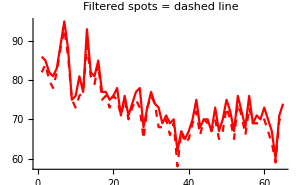
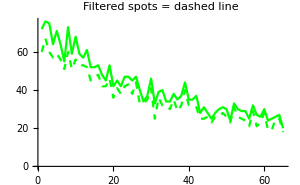
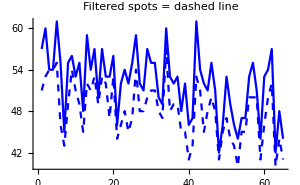

```mathematica
pfiltered = Row[{
ListLinePlot[{Length/@fitRspotsfiltered[[1]],Length/@fitredspots[[1]]},ImageSize->300,PlotStyle->{{Red,Dashed},{Red}},PlotLabel->"Filtered spots = dashed line"],
ListLinePlot[{Length/@fitGspotsfiltered[[1]],Length/@fitgreenspots[[1]]},ImageSize->300,PlotStyle->{{Green,Dashed},{Green}},PlotLabel->"Filtered spots = dashed line" ],
ListLinePlot[{Length/@fitBspotsfiltered[[1]],Length/@fitbluespots[[1]]},ImageSize->300,PlotStyle->{{Blue,Dashed},{Blue}} ,PlotLabel->"Filtered spots = dashed line" ]  }]
```

```mathematica
pfiltered
```

-Graphics--Graphics--Graphics-

```mathematica
pfiltered>>(analysisFolder<>"_pFiltered.dat");
```

#### Visually check Pre/Post filtered spots in your cells.....

```mathematica
color = blue;
Row[{
Manipulate[Show[myColMovie⟦color,frame⟧//ImageAdjust[#,{0,0,1}*3,MyTh[color,thred,thgreen,thblue]]&,Graphics[{Green,Circle[#,7]&/@(fitGspotsfiltered⟦1,frame,All,3,1⟧)}],Graphics[{Blue,Circle[#,7]&/@(fitBspotsfiltered⟦1,frame,All,3,1⟧)}],Graphics[{Red,Circle[#,6]&/@(myTfFunc/@fitRspotsfiltered⟦1,frame,All,3,1⟧)}]],
{frame,1,myMaxN,1},FrameLabel->{{"",""},{"","POST-Filtered"}}],
Manipulate[Show[myColMovie⟦color,frame⟧//ImageAdjust[#,{0,0,1},MyTh[color,thred,thgreen,thblue]]&,Graphics[{Green,Circle[#,7]&/@(greenRunAvp⟦frame⟧)}],Graphics[{Blue,Circle[#,7]&/@(blueRunAvp⟦frame⟧)}],Graphics[{Red,Circle[#,6]&/@(myTfFunc/@redRunAvp⟦frame⟧)}]],
{frame,1,myMaxN,1},FrameLabel->{{"",""},{"","PRE-Filtered"}}]
}]
```

### Call Yellow, Purple, White, and Red Only spots

Call ALL yellow spots (includes YELLOW and WHITE so I call them “Red-Green”)  *REPAIRED*

```mathematica
reds = fitRspotsfiltered⟦1,All,All,3,1⟧;
greens = fitGspotsfiltered⟦1,All,All,3,1⟧;
blues = fitBspotsfiltered⟦1,All,All,3,1⟧;
Dimensions/@blues[[1]]
Dimensions/@reds[[1]]
```

{{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2}}

{{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2},{2}}

```mathematica
(* WORKS FOR JSUT SPOTS
find all yellow spots*)
colocalizeDist=4;
myRedGreenSpots=Table[
Select[Table[
Select[reds⟦frame⟧,EuclideanDistance[myTfFunc@#,greens⟦frame,track,All⟧]<colocalizeDist&]
,{track,1,Length@greens⟦frame⟧,1}]//Flatten[#,1]&(*Moved flatten here*) ,UnsameQ[#,{}]&]
,{frame,1,Length@greens,1}];
(*This is still not truly yellow spots I need to now deletecases that match white spots!*)
```

Count # of ALL yellow spots per frame thru whole movie 
(includes YELLOW and WHITE so I call them “Red-Green”)

```mathematica
countRedGreen = Length/@myRedGreenSpots
```

{28,30,29,27,28,30,25,27,22,24,23,21,18,20,22,20,21,18,21,20,15,17,17,20,16,16,14,17,12,17,10,13,9,13,7,11,9,13,10,12,13,12,7,8,6,4,8,8,9,8,6,7,5,3,7,4,6,6,0,3,3,3,3,6,4}

Call ALL purple spots (includes PURPLE and WHITE so I call them “BLUE-RED”) *REPAIRED*

```mathematica
(*find purple spots, some of these are white spots tho*)
myRedBlueSpots=Table[
Select[Table[
Select[reds⟦frame⟧,EuclideanDistance[myTfFunc@#,blues⟦frame,track,All⟧]<colocalizeDist&]
,{track,1,Length@blues⟦frame⟧,1}]//Flatten[#,1]&(*Moved flatten here*) , UnsameQ[#,{}]&]
,{frame,1,Length@blues,1}];
```

```mathematica
(*find purple spots, some of these are white spots tho*)
(*OLD
myRedBlueSpots=Table[
Select[Table[
Select[redRunAvp⟦frame⟧,EuclideanDistance[myTfFunc@#,blueRunAvp⟦frame,track,All⟧]<colocalizeDist&]
,{track,1,Length@blueRunAvp⟦frame⟧,1}]//Flatten[#,1]&(*Moved flatten here*) , UnsameQ[#,{}]&]
,{frame,1,Length@blueRunAvp,1}];
(*movie with blue spots...*) 
Manipulate[Show[myColMovieRunAv⟦3,frame⟧//ImageAdjust[#,{0,0,1},thblue]&,Graphics[{Blue,Circle[#,7]&/@(myRedBlueSpots⟦frame⟧)}]],
{frame,1,myMaxN,1}];
myTfRedBlueSpots=myTfFunc/@myRedBlueSpots;
```

```mathematica
myRedBlueSpots⟦6⟧
```

{{341.807,412.976},{249.137,386.356},{271.194,379.008},{188.951,376.324},{258.508,372.838},{252.836,366.523},{230.609,353.787},{235.993,348.015},{206.715,346.881},{235.985,338.667},{255.657,337.568},{173.16,333.386},{295.807,328.589},{267.269,325.148},{309.086,320.877},{278.163,309.943},{291.367,304.343},{254.855,300.393},{323.354,290.511},{291.406,285.162},{360.685,282.649},{292.092,278.436},{326.28,268.319},{248.844,267.281},{346.124,266.146},{174.375,265.346},{309.688,263.126},{261.074,257.21},{298.955,253.022},{264.482,251.26},{243.378,244.195},{225.391,241.388},{346.584,239.914},{278.156,239.82},{334.226,235.836},{342.491,227.},{358.509,217.33},{353.27,173.051}}

Count # of ALL purple spots per frame thru whole movie 
(includes PURPLE and WHITE so I call them “BLUE-RED”)

```mathematica
countRedBlue = Length/@myRedBlueSpots
```

{38,43,37,40,36,38,34,36,38,36,35,37,39,40,41,42,38,38,38,39,36,34,38,38,36,40,35,36,37,43,39,33,37,41,38,37,35,31,38,36,34,40,38,36,37,40,40,38,38,37,33,38,37,38,35,38,38,33,32,36,37,40,34,36,32}

Call YELLOW ONLY spots per frame thru whole movie 
      -> plus Transformed centroids w TF 
(ONLY spots that are yellow, excludes white spots)

```mathematica
myYellowOnlySpots=Complement@@@Thread@{myRedGreenSpots,myRedBlueSpots};
myTfYellowOnlyPositions=(myTfFunc/@myYellowOnlySpots);
```

Count # of YELLOW ONLY spots per frame thru whole movie 
(ONLY spots that are yellow, excludes white spots)

{11,11,11,12,12,13,11,15,5,9,11,7,7,4,8,8,4,6,5,9,7,7,6,4,6,9,7,7,3,6,4,7,2,5,2,4,3,8,1,3,4,6,1,4,3,0,3,1,4,4,4,2,1,0,2,3,2,4,0,2,1,0,2,4,3}

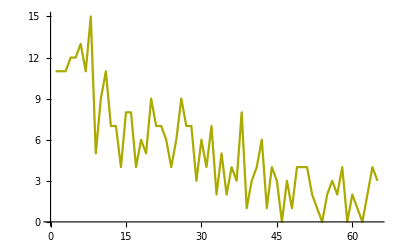

```mathematica
countYellow=Length/@myTfYellowOnlyPositions
countYellow//ListLinePlot[#,PlotStyle->Darker[Yellow]]&
```

Call RED ONLY spots per frame thru whole movie 
(ONLY red spots without green or blue colocalization)

```mathematica
(*find RED ONLY spots*)
myRedOnlySpots=Complement@@@Thread@{redRunAvp,myRedBlueSpots}//Complement@@@Thread@{#,myRedGreenSpots}&;
```

Count # of RED ONLY spots per frame thru whole movie 
(ONLY red spots without green or blue colocalization)

{37,33,34,29,35,38,51,37,32,31,36,34,47,38,32,36,36,34,32,28,35,30,32,29,33,28,36,26,33,29,31,33,30,25,29,29,24,28,26,28,32,29,29,30,30,27,30,28,28,34,35,27,38,34,31,35,29,34,38,35,32,27,24,31,39}

{86,85,82,81,83,89,95,88,75,76,81,77,93,82,81,85,77,77,75,76,78,71,76,71,74,77,78,68,73,77,74,73,69,71,69,70,62,67,65,67,70,75,68,70,70,67,73,67,70,75,72,67,76,72,68,76,69,71,70,73,70,67,60,71,74}

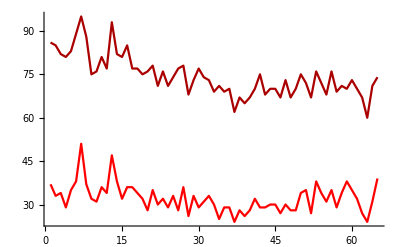

```mathematica
countRedOnly = Length/@myRedOnlySpots
Length/@redRunAvp (* This is the total # of red spots, including yellow and white, just for reference *) 
Show[ListLinePlot[{countRedOnly}, PlotStyle-> Red],ListLinePlot[{Length/@redRunAvp},PlotStyle->Darker[Red]], PlotRange->All]
```

Count # of PURPLE ONLY spots per frame thru whole movie 
      -> plus Transformed centroids w TF 
(ONLY purple spots, without green colocalization)

```mathematica
myPurpleOnlySpots= myRedBlueSpots//Complement@@@Thread@{#,myRedGreenSpots}&;
```

{21,22,19,25,20,21,19,24,21,21,22,22,28,24,27,29,20,25,23,28,28,24,27,23,25,33,28,25,28,31,33,27,31,33,33,30,29,26,29,27,25,34,32,32,34,36,35,31,33,33,31,33,33,35,30,37,34,31,32,35,35,37,33,34,31}

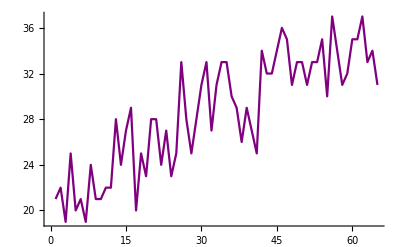

```mathematica
countPurple = Length/@myPurpleOnlySpots
ListLinePlot[{countPurple}, PlotStyle-> Purple]
```

Count # of WHITE ONLY spots per frame thru whole movie 
      -> plus Transformed centroids w TF 
(ONLY spots with red, blue, and green  colocalization)

{17,19,18,15,16,17,14,12,17,15,12,14,11,16,14,12,17,12,15,11,8,10,11,15,10,7,7,10,9,11,6,6,6,8,5,7,6,5,9,9,9,6,6,4,3,4,5,7,5,4,2,5,4,3,5,1,4,2,0,1,2,3,1,2,1}

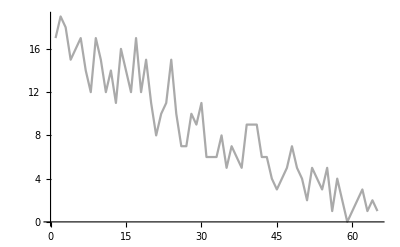

```mathematica
myWhiteSpots=Intersection@@@Thread@{myRedGreenSpots,myRedBlueSpots};
Manipulate[Show[myColMovieRunAv⟦3,frame⟧//ImageAdjust[#,{0,0,1},thgreen/.5]&,Graphics[{Gray,Circle[#,7]&/@(myWhiteSpots⟦frame⟧)}]],
{frame,1,myMaxN,1}];
countWhite = (Length/@myWhiteSpots)
countWhite//ListLinePlot[#,PlotStyle->Lighter[Gray],PlotRange->All]&
```

Use this plot to make sure that you are actually removing the white spots from the red-blue list 
---> Blue (Red-Blue) should be the SUM of white and purple

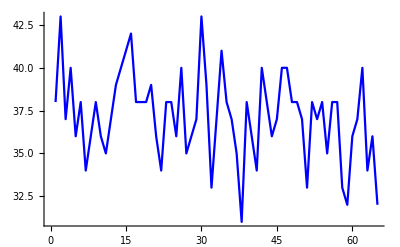

```mathematica
ListLinePlot[countRedBlue,PlotStyle->Blue]
```

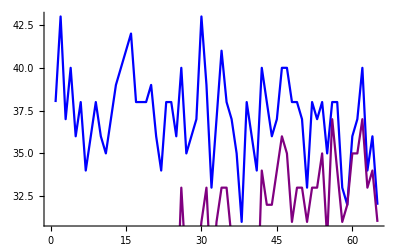

```mathematica
Show[ListLinePlot[countRedBlue,PlotStyle->Blue],ListLinePlot[{countPurple}, PlotStyle-> Purple],ListLinePlot[countWhite,PlotStyle->Lighter[Gray],PlotRange->All]]
```

```mathematica
countPurple 
 countWhite
countRedBlue
myPurpleOnlySpots[[1]]//Sort
myWhiteSpots[[1]]//Sort
myRedBlueSpots[[1]]//Sort
```

{21,22,19,25,20,21,19,24,21,21,22,22,28,24,27,29,20,25,23,28,28,24,27,23,25,33,28,25,28,31,33,27,31,33,33,30,29,26,29,27,25,34,32,32,34,36,35,31,33,33,31,33,33,35,30,37,34,31,32,35,35,37,33,34,31}

{17,19,18,15,16,17,14,12,17,15,12,14,11,16,14,12,17,12,15,11,8,10,11,15,10,7,7,10,9,11,6,6,6,8,5,7,6,5,9,9,9,6,6,4,3,4,5,7,5,4,2,5,4,3,5,1,4,2,0,1,2,3,1,2,1}

{38,43,37,40,36,38,34,36,38,36,35,37,39,40,41,42,38,38,38,39,36,34,38,38,36,40,35,36,37,43,39,33,37,41,38,37,35,31,38,36,34,40,38,36,37,40,40,38,38,37,33,38,37,38,35,38,38,33,32,36,37,40,34,36,32}

{{177.12,343.618},{179.496,317.518},{192.605,370.647},{234.076,236.903},{236.22,355.817},{239.346,349.204},{254.042,391.113},{258.87,375.832},{261.144,304.64},{267.153,258.243},{268.421,243.093},{270.142,249.895},{295.025,303.305},{307.369,325.047},{309.918,251.669},{317.82,257.606},{346.903,414.434},{350.669,238.923},{356.654,173.222},{368.163,283.597},{386.173,227.164}}

{{177.693,264.107},{183.462,331.352},{208.041,347.184},{228.316,342.237},{253.352,353.374},{256.606,275.241},{262.469,339.742},{267.336,378.347},{272.304,327.867},{282.417,307.381},{287.599,318.23},{299.771,280.436},{304.457,290.469},{328.573,270.61},{329.386,291.563},{344.508,227.64},{355.67,269.141}}

{{177.12,343.618},{177.693,264.107},{179.496,317.518},{183.462,331.352},{192.605,370.647},{208.041,347.184},{228.316,342.237},{234.076,236.903},{236.22,355.817},{239.346,349.204},{253.352,353.374},{254.042,391.113},{256.606,275.241},{258.87,375.832},{261.144,304.64},{262.469,339.742},{267.153,258.243},{267.336,378.347},{268.421,243.093},{270.142,249.895},{272.304,327.867},{282.417,307.381},{287.599,318.23},{295.025,303.305},{299.771,280.436},{304.457,290.469},{307.369,325.047},{309.918,251.669},{317.82,257.606},{328.573,270.61},{329.386,291.563},{344.508,227.64},{346.903,414.434},{350.669,238.923},{355.67,269.141},{356.654,173.222},{368.163,283.597},{386.173,227.164}}

```mathematica
Table[(countPurple[[i]] + countWhite[[i]]) == countRedBlue[[i]],{i,1,Length@countWhite,1}]
```

{True,False,True,True,True,True,False,True,True,True,False,False,True,True,True,False,False,False,True,True,True,True,True,True,False,True,True,False,True,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

#### Testing the spot calling (Look at spots in cell movie over time)

```mathematica
Manipulate[Show[myColMovie⟦2,frame⟧//ImageAdjust[#,{0,0,1},thred*4]&,Graphics[{Green,Circle[#,7]&/@(greens⟦frame⟧)}],Graphics[{Blue,Circle[#,7]&/@(blues⟦frame⟧)}],Graphics[{Red,Circle[#,6]&/@(myTfFunc/@reds⟦frame⟧)}]],
{frame,1,myMaxN,1}]
```

#### Define times of images

Change as necessary 
As put: Movie starts 2.5h and runs for 26 frames, one frame every 30 m

```mathematica
q = 4 ; (*video start time *)
r = .5; (* time interval between frames *)
mytimes = Table[i,{i,q,(r*(Length@countRedGreen)+q-r), r}]
Length@countRedOnly(* # frames in video*) 
Length@mytimes(*projected # frames in video...if these numbers are different, then your times calculation is off*)
```

{4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,9.5,10.,10.5,11.,11.5,12.,12.5,13.,13.5,14.,14.5,15.,15.5,16.,16.5,17.,17.5,18.,18.5,19.,19.5,20.,20.5,21.,21.5,22.,22.5,23.,23.5,24.,24.5,25.,25.5,26.,26.5,27.,27.5,28.,28.5,29.,29.5,30.,30.5,31.,31.5,32.,32.5,33.,33.5,34.,34.5,35.,35.5,36.}

65

65

#### Make Graphs of the counts of the spots in the cell at each time

Use this plot to total at the TOTAL counts of spots, partitioned into spot-called categories 
-> Red = red-only
-> Yellow = yellow-only
-> Purple = purple-only 
-> Gray = white-only

```mathematica
totals = countRedOnly+countYellow+countPurple+countWhite
```

{86,85,82,81,83,89,95,88,75,76,81,77,93,82,81,85,77,77,75,76,78,71,76,71,74,77,78,68,73,77,74,73,69,71,69,70,62,67,65,67,70,75,68,70,70,67,73,67,70,75,72,67,76,72,68,76,69,71,70,73,70,67,60,71,74}

```mathematica
countRYPWall = {{{"mytimes","countYellowOnly"},{"mytimes","countWhiteOnly"},{"mytimes","countPurpleOnly"},{"mytimes","countRedOnly"},{"mytimes","total spot count"}},{Transpose[{mytimes,countYellow}],Transpose[{mytimes,countWhite}],Transpose[{mytimes,countPurple}],Transpose[{mytimes,countRedOnly}],Transpose[{mytimes,totals}] }}
```

{{{mytimes,countYellowOnly},{mytimes,countWhiteOnly},{mytimes,countPurpleOnly},{mytimes,countRedOnly},{mytimes,total spot count}},{{{4.,11},{4.5,11},{5.,11},{5.5,12},{6.,12},{6.5,13},{7.,11},{7.5,15},{8.,5},{8.5,9},{9.,11},{9.5,7},{10.,7},{10.5,4},{11.,8},{11.5,8},{12.,4},{12.5,6},{13.,5},{13.5,9},{14.,7},{14.5,7},{15.,6},{15.5,4},{16.,6},{16.5,9},{17.,7},{17.5,7},{18.,3},{18.5,6},{19.,4},{19.5,7},{20.,2},{20.5,5},{21.,2},{21.5,4},{22.,3},{22.5,8},{23.,1},{23.5,3},{24.,4},{24.5,6},{25.,1},{25.5,4},{26.,3},{26.5,0},{27.,3},{27.5,1},{28.,4},{28.5,4},{29.,4},{29.5,2},{30.,1},{30.5,0},{31.,2},{31.5,3},{32.,2},{32.5,4},{33.,0},{33.5,2},{34.,1},{34.5,0},{35.,2},{35.5,4},{36.,3}},{{4.,17},{4.5,19},{5.,18},{5.5,15},{6.,16},{6.5,17},{7.,14},{7.5,12},{8.,17},{8.5,15},{9.,12},{9.5,14},{10.,11},{10.5,16},{11.,14},{11.5,12},{12.,17},{12.5,12},{13.,15},{13.5,11},{14.,8},{14.5,10},{15.,11},{15.5,15},{16.,10},{16.5,7},{17.,7},{17.5,10},{18.,9},{18.5,11},{19.,6},{19.5,6},{20.,6},{20.5,8},{21.,5},{21.5,7},{22.,6},{22.5,5},{23.,9},{23.5,9},{24.,9},{24.5,6},{25.,6},{25.5,4},{26.,3},{26.5,4},{27.,5},{27.5,7},{28.,5},{28.5,4},{29.,2},{29.5,5},{30.,4},{30.5,3},{31.,5},{31.5,1},{32.,4},{32.5,2},{33.,0},{33.5,1},{34.,2},{34.5,3},{35.,1},{35.5,2},{36.,1}},{{4.,21},{4.5,22},{5.,19},{5.5,25},{6.,20},{6.5,21},{7.,19},{7.5,24},{8.,21},{8.5,21},{9.,22},{9.5,22},{10.,28},{10.5,24},{11.,27},{11.5,29},{12.,20},{12.5,25},{13.,23},{13.5,28},{14.,28},{14.5,24},{15.,27},{15.5,23},{16.,25},{16.5,33},{17.,28},{17.5,25},{18.,28},{18.5,31},{19.,33},{19.5,27},{20.,31},{20.5,33},{21.,33},{21.5,30},{22.,29},{22.5,26},{23.,29},{23.5,27},{24.,25},{24.5,34},{25.,32},{25.5,32},{26.,34},{26.5,36},{27.,35},{27.5,31},{28.,33},{28.5,33},{29.,31},{29.5,33},{30.,33},{30.5,35},{31.,30},{31.5,37},{32.,34},{32.5,31},{33.,32},{33.5,35},{34.,35},{34.5,37},{35.,33},{35.5,34},{36.,31}},{{4.,37},{4.5,33},{5.,34},{5.5,29},{6.,35},{6.5,38},{7.,51},{7.5,37},{8.,32},{8.5,31},{9.,36},{9.5,34},{10.,47},{10.5,38},{11.,32},{11.5,36},{12.,36},{12.5,34},{13.,32},{13.5,28},{14.,35},{14.5,30},{15.,32},{15.5,29},{16.,33},{16.5,28},{17.,36},{17.5,26},{18.,33},{18.5,29},{19.,31},{19.5,33},{20.,30},{20.5,25},{21.,29},{21.5,29},{22.,24},{22.5,28},{23.,26},{23.5,28},{24.,32},{24.5,29},{25.,29},{25.5,30},{26.,30},{26.5,27},{27.,30},{27.5,28},{28.,28},{28.5,34},{29.,35},{29.5,27},{30.,38},{30.5,34},{31.,31},{31.5,35},{32.,29},{32.5,34},{33.,38},{33.5,35},{34.,32},{34.5,27},{35.,24},{35.5,31},{36.,39}},{{4.,86},{4.5,85},{5.,82},{5.5,81},{6.,83},{6.5,89},{7.,95},{7.5,88},{8.,75},{8.5,76},{9.,81},{9.5,77},{10.,93},{10.5,82},{11.,81},{11.5,85},{12.,77},{12.5,77},{13.,75},{13.5,76},{14.,78},{14.5,71},{15.,76},{15.5,71},{16.,74},{16.5,77},{17.,78},{17.5,68},{18.,73},{18.5,77},{19.,74},{19.5,73},{20.,69},{20.5,71},{21.,69},{21.5,70},{22.,62},{22.5,67},{23.,65},{23.5,67},{24.,70},{24.5,75},{25.,68},{25.5,70},{26.,70},{26.5,67},{27.,73},{27.5,67},{28.,70},{28.5,75},{29.,72},{29.5,67},{30.,76},{30.5,72},{31.,68},{31.5,76},{32.,69},{32.5,71},{33.,70},{33.5,73},{34.,70},{34.5,67},{35.,60},{35.5,71},{36.,74}}}}

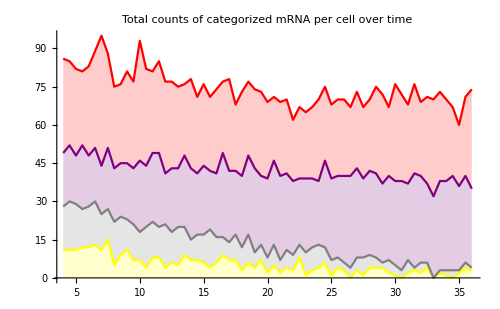

```mathematica
pcountRYPW = StackedListPlot[ countRYPWall[[2,1;;4]], PlotStyle-> {Yellow , Gray,Purple, Red},ImageSize-> 500,PlotLabel-> "Total counts of categorized mRNA per cell over time"]
```

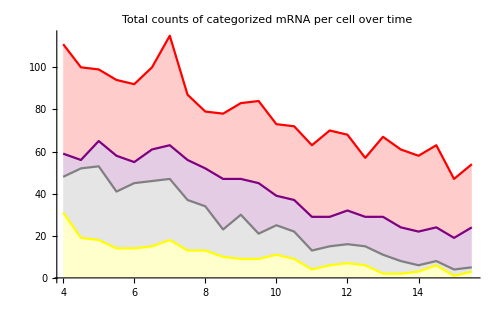

-Graphics-

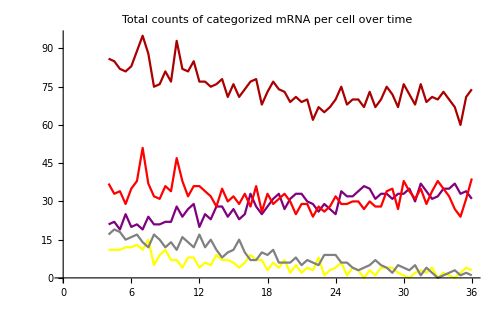

```mathematica
pcountRYPW = ListLinePlot[ countRYPWall[[2]], PlotStyle-> { Yellow ,Gray, Purple, Red, Darker[Red]},ImageSize-> 500,PlotLabel-> "Total counts of categorized mRNA per cell over time"]
```

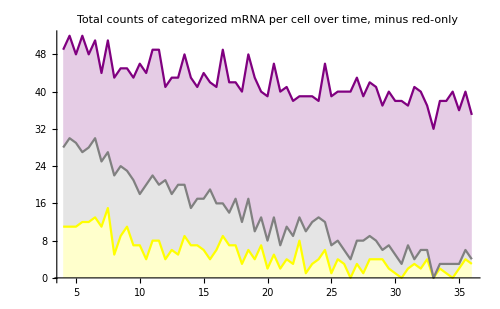

```mathematica
pcountYPW = StackedListPlot[ countRYPWall[[2,1;;3]], PlotStyle-> { Yellow ,Gray, Purple},ImageSize-> 500,PlotLabel-> "Total counts of categorized mRNA per cell over time, minus red-only",PlotRange->All]
```

```mathematica
Export[analysisFolder<>"_plot_countRYPW_filter.tif",pcountRYPW ];
Export[analysisFolder<>"_plot_countYPW_filter.tif",pcountYPW ];
countRYPWall>>analysisFolder<>"_countRYPWall_filter.dat"
```

### Trims

#### Making Trims Through Time

Make White trims 
{ { { Red Ch Img,  Green Ch Img,   Blue Ch Img } , ...  }  ...nested lists at each frame of movie...  }

```mathematica
pad2=7;
myWhiteSpotTrims=Table[Table[
tempCenter=Ceiling@myWhiteSpots[[frame,track]];
tftempCenter=Ceiling@myTfFunc@myWhiteSpots[[frame,track]];
{tempRed,tempGreen,tempBlue}=
{ImageTrim[myColMovie⟦1,frame⟧,{tempCenter-pad2,tempCenter+pad2-0.1}],
ImageTrim[myColMovie⟦2,frame⟧,{tftempCenter-pad2,tftempCenter+pad2-0.1}],
ImageTrim[myColMovie⟦3,frame⟧,{tftempCenter-pad2,tftempCenter+pad2-0.1}]},
{track,1,Length[myWhiteSpots[[frame]]],1}],{frame,1,Length[Length/@myWhiteSpots],1}];
Export[analysisFolder<>"_myWhiteSpotTrims.m",myWhiteSpotTrims];
```

Make Red-Green trims 
(ALL YELLOW... yellow + white trims)

```mathematica
myAllRedGreenTrims=Table[Table[
tempCenter=Ceiling@myRedGreenSpots[[frame,track]];
tftempCenter = Ceiling@myTfFunc@myRedGreenSpots[[frame,track]];
{tempRed,tempGreen,tempBlue}=
{ImageTrim[myColMovie⟦1,frame⟧,{tempCenter-pad2,tempCenter+pad2-0.1}],
ImageTrim[myColMovie⟦2,frame⟧,{tftempCenter-pad2,tftempCenter+pad2-0.1}],
ImageTrim[myColMovie⟦3,frame⟧,{tftempCenter-pad2,tftempCenter+pad2-0.1}]},
{track,1,Length[myTfYellowOnlyPositions[[frame]]],1}],{frame,1,Length[Length/@myTfYellowOnlyPositions],1}];
Export[analysisFolder<>"_myYellowSpotTrims.m",myAllRedGreenTrims];
```

Make YELLOW ONLY trims

```mathematica
myYellowOnlySpotTrims=Table[Table[
tempCenter=Ceiling@myYellowOnlySpots[[frame,track]];
tftempCenter=Ceiling@myTfFunc@myYellowOnlySpots[[frame,track]];
{tempRed,tempGreen,tempBlue}=
{ImageTrim[myColMovie⟦1,frame⟧,{tempCenter-pad2,tempCenter+pad2-0.1}],
ImageTrim[myColMovie⟦2,frame⟧,{tftempCenter-pad2,tftempCenter+pad2-0.1}],
ImageTrim[myColMovie⟦3,frame⟧,{tftempCenter-pad2,tftempCenter+pad2-0.1}]},
{track,1,Length[myTfYellowOnlyPositions[[frame]]],1}],{frame,1,Length[Length/@myTfYellowOnlyPositions],1}];
Export[analysisFolder<>"_myYellowSpotTrims.m",myYellowOnlySpotTrims];
```

Make Red-Blue Spot Trims
(Purple + White spots)

```mathematica
myAllBlueRedSpotTrims=Table[Table[
tempCenter=Ceiling@myRedBlueSpots[[frame,track]];
tftempCenter=Ceiling@myTfFunc@myRedBlueSpots[[frame,track]];
{tempRed,tempGreen,tempBlue}=
{ImageTrim[myColMovie⟦1,frame⟧,{tempCenter-pad2,tempCenter+pad2-0.1}],
ImageTrim[myColMovie⟦2,frame⟧,{tftempCenter-pad2,tftempCenter+pad2-0.1}],
ImageTrim[myColMovie⟦3,frame⟧,{tftempCenter-pad2,tftempCenter+pad2-0.1}]},
{track,1,Length[myRedBlueSpots[[frame]]],1}],{frame,1,Length[Length/@myRedBlueSpots],1}];
Export[analysisFolder<>"_myPurpleSpotTrims.m",myAllBlueRedSpotTrims];
```

Make Purple Spot Trims
(Purple ONLY spots)

```mathematica
pad2=7;
myPurpleSpotTrims=Table[Table[
tempCenter=Ceiling@myPurpleOnlySpots[[frame,track]];
tftempCenter=Ceiling@myTfFunc@myPurpleOnlySpots[[frame,track]];
{tempRed,tempGreen,tempBlue}=
{ImageTrim[myColMovie⟦1,frame⟧,{tempCenter-pad2,tempCenter+pad2-0.1}],
ImageTrim[myColMovie⟦2,frame⟧,{tftempCenter-pad2,tftempCenter+pad2-0.1}],
ImageTrim[myColMovie⟦3,frame⟧,{tftempCenter-pad2,tftempCenter+pad2-0.1}]},
{track,1,Length[myPurpleOnlySpots[[frame]]],1}],{frame,1,Length[Length/@myPurpleOnlySpots],1}];
Export[analysisFolder<>"_myPurpleSpotTrims.m",myPurpleSpotTrims];
```

Make RedOnly Spot Trims
(Red ONLY spots)

```mathematica
pad2=7;
myRedOnlySpotTrims=Table[Table[
tempCenter=Ceiling@myRedOnlySpots[[frame,track]];
tftempCenter=Ceiling@myTfFunc@myRedOnlySpots[[frame,track]];
{tempRed,tempGreen,tempBlue}=
{ImageTrim[myColMovie⟦1,frame⟧,{tempCenter-pad2,tempCenter+pad2-0.1}],
ImageTrim[myColMovie⟦2,frame⟧,{tftempCenter-pad2,tftempCenter+pad2-0.1}],
ImageTrim[myColMovie⟦3,frame⟧,{tftempCenter-pad2,tftempCenter+pad2-0.1}]},
{track,1,Length[myRedOnlySpots[[frame]]],1}],{frame,1,Length[Length/@myRedOnlySpots],1}];
Export[analysisFolder<>"_myRedOnlySpotTrims.m",myRedOnlySpotTrims];
```

### YELLOW ONLY:

#### Rename

```mathematica
tempspots = myYellowOnlySpots;
temptrims = myYellowOnlySpotTrims;
name = "_YELLOW_"
```

_YELLOW_

#### Background Fill Time Points that have no spots

```mathematica
Length/@tempspots[[All]]
```

{11,11,11,12,12,13,11,15,5,9,11,7,7,4,8,8,4,6,5,9,7,7,6,4,6,9,7,7,3,6,4,7,2,5,2,4,3,8,1,3,4,6,1,4,3,0,3,1,4,4,4,2,1,0,2,3,2,4,0,2,1,0,2,4,3}

```mathematica
myBGFillPositions=Table[Nearest[(Position[Length/@temptrims[[All]],x_/;x>0])[[All,1]],(Position[Length/@temptrims[[All]],x_/;x==0])[[frame,1]]][[1]],{frame,1,Length@(Position[Length/@temptrims[[All]],x_/;x==0])[[All,1]],1}]
```

{45,53,58,61}

```mathematica
my0SpotPos=Flatten@(Position[Length/@temptrims[[All]],x_/;x==0])
```

{46,54,59,62}

```mathematica
edgeMask=Image[DiskMatrix[10,{15,15}]-DiskMatrix[3,{15,15}] ];
```

```mathematica
myBGFillPositions=Table[Nearest[(Position[Length/@temptrims[[All]],x_/;x>0])[[All,1]],(Position[Length/@temptrims[[All]],x_/;x==0])[[frame,1]]][[1]],{frame,1,Length@(Position[Length/@temptrims[[All]],x_/;x==0])[[All,1]],1}]
```

{45,53,58,61}

```mathematica
edgeMask=Image[DiskMatrix[10,{15,15}]-DiskMatrix[3,{15,15}] ];
```

```mathematica
theReplacements={};
myPosBGReplacements=Partition[Partition[Flatten@Table[
ImageData[temptrims[[myBGFillPositions]][[spot,1,color]]];
mytemp0s=Flatten@Position[Flatten[ImageData[ImageMultiply[edgeMask,#]]]&@temptrims[[myBGFillPositions]][[spot,1,color]],x_/;x==0];
myBgPixels=Flatten@Position[Flatten[ImageData[ImageMultiply[edgeMask,#]]]&@temptrims[[myBGFillPositions]][[spot,1,color]],x_/;x>0];
myRandomBGPixels=RandomChoice[myBgPixels,Length@mytemp0s];
mytempImgData=Flatten[ImageData[ImageMultiply[edgeMask,#]]]&@temptrims[[myBGFillPositions]][[spot,1,color]];
mytempChgList=Thread[mytemp0s-> mytempImgData[[myRandomBGPixels]]];
{(*myBGFillPositions[[spot]],*)Image[Partition[ReplacePart[mytempImgData,mytempChgList],15]]}
,{spot,1,Length@myBGFillPositions,1},{color,1,3,1}],3],1];
```

```mathematica
tempGapFillTrims=ReplacePart[temptrims,Thread[my0SpotPos-> myPosBGReplacements]];
```

```mathematica
Length@tempGapFillTrims
```

65

```mathematica
Dimensions/@tempGapFillTrims
```

{{11,3},{11,3},{11,3},{12,3},{12,3},{13,3},{11,3},{15,3},{5,3},{9,3},{11,3},{7,3},{7,3},{4,3},{8,3},{8,3},{4,3},{6,3},{5,3},{9,3},{7,3},{7,3},{6,3},{4,3},{6,3},{9,3},{7,3},{7,3},{3,3},{6,3},{4,3},{7,3},{2,3},{5,3},{2,3},{4,3},{3,3},{8,3},{1,3},{3,3},{4,3},{6,3},{1,3},{4,3},{3,3},{1,3},{3,3},{1,3},{4,3},{4,3},{4,3},{2,3},{1,3},{1,3},{2,3},{3,3},{2,3},{4,3},{1,3},{2,3},{1,3},{1,3},{2,3},{4,3},{3,3}}

#### Making Mean Crops

```mathematica
tempGapFillTrimsMeans=Table[Mean@tempGapFillTrims[[frame,All,color]],{frame,1,Length@tempGapFillTrims},{color,1,3,1}];
```

```mathematica
ImageAdjust/@tempGapFillTrimsMeans[[All,1]]
ImageAdjust/@tempGapFillTrimsMeans[[All,2]]
ImageAdjust/@tempGapFillTrimsMeans[[All,3]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Finding intensities with a Gaussian

```mathematica
myRGaussInts=GetTrimPeakIntFixedSigma[#,1.5]&/@tempGapFillTrims[[All,All,1]]//Table[Cases[Flatten[#[[i]],1], x_/;x>0],{i,1,Length@#,1}]&;
```

```mathematica
myGGaussInts=GetTrimPeakIntFixedSigma[#,1.5]&/@tempGapFillTrims[[All,All,2]]//Table[Cases[Flatten[#[[i]],1], x_/;x>0],{i,1,Length@#,1}]&;
```

```mathematica
myBGaussInts=GetTrimPeakIntFixedSigma[#,1.5]&/@tempGapFillTrims[[All,All,3]]//Table[Cases[Flatten[#[[i]],1], x_/;x>0],{i,1,Length@#,1}]&;
```

```mathematica
Total/@myRGaussInts
Total/@myGGaussInts
Total/@myBGaussInts
```

{0.0927789,0.115658,0.0895258,0.112166,0.0887684,0.116181,0.0962406,0.163428,0.0434706,0.0851698,0.0876662,0.0405118,0.0620184,0.0477634,0.0614199,0.0722525,0.025042,0.0547945,0.0424034,0.0895059,0.0738166,0.0597067,0.0501146,0.0160242,0.0396436,0.0888079,0.0541234,0.0628986,0.0211748,0.0578775,0.0340897,0.0620617,0.0183459,0.0680539,0.0155771,0.0328205,0.0271693,0.09448,0.0090759,0.0405116,0.0274203,0.0317577,0.0111159,0.0347684,0.0146978,0,0.0186906,0.00474706,0.0189808,0.0308632,0.0521605,0.0144452,0.0129478,0.00130771,0.019472,0.0271653,0.0262512,0.0278719,0,0.0216713,0.00885454,0.00106451,0.0213354,0.0384358,0.0197164}

{0.344865,0.373833,0.320049,0.373134,0.357061,0.515409,0.314714,0.485655,0.125653,0.2888,0.353981,0.16207,0.179556,0.107405,0.257715,0.280412,0.104117,0.195765,0.106269,0.284779,0.138194,0.193884,0.206367,0.178452,0.174757,0.212026,0.143002,0.186067,0.108958,0.208519,0.139675,0.187189,0.0720671,0.141521,0.103416,0.0893779,0.0757035,0.248883,0.0300964,0.131174,0.125482,0.155164,0.0160828,0.079972,0.0538384,0.00698823,0.109608,0.0154645,0.0971164,0.0979118,0.075777,0.0482507,0.0159645,0.0024698,0.0385721,0.149181,0.127375,0.0614882,0.0191055,0.0446536,0.0193781,0.0164936,0.0428534,0.0551425,0.0546285}

{0.106641,0.102432,0.114974,0.163998,0.121045,0.1149,0.0808312,0.238209,0.0451783,0.136767,0.243941,0.0604902,0.0432952,0.0285097,0.0433333,0.220126,0.0192285,0.0332598,0.0460287,0.0841397,0.0567546,0.129106,0.0464554,0.0423784,0.0716494,0.0573266,0.0303287,0.0656872,0.0231951,0.0901792,0.0291712,0.0907115,0.0297908,0.0332503,0.0217194,0.0617374,0.0285628,0.0859961,0.0082791,0.0715765,0.0143331,0.0413211,0.00573605,0.0268962,0.0436604,0,0.0268482,0.00431328,0.0274808,0.0436788,0.0388579,0.0122002,0.00799661,0,0.00912758,0.0176187,0.0152842,0.0171059,0,0.0150422,0.0134312,0.00139488,0.0139833,0.0333282,0.035022}

```mathematica
tempdataframe = {{{"myRGaussInts_>0"},{"myGGaussInts_>0"},{"myBGaussInts_>0"}},myRGaussInts,myGGaussInts,myBGaussInts};
```

#### Plotting Gaussian intensity over time

```mathematica
Grid[{ImageAdjust/@ColorCombine/@tempGapFillTrimsMeans}]
pIntensityTime = ListLinePlot[{Transpose[{mytimes,Flatten@(Total/@myRGaussInts)}],Transpose[{mytimes,Flatten@(Total/@myGGaussInts)}],Transpose[{mytimes,Flatten@(Total/@myBGaussInts)}]}, PlotStyle->{Red,Green,Blue}, PlotLabel->name<>" Total Intensity of spots per cell", PlotRange->All];
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

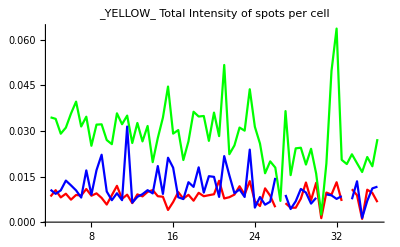

```mathematica
pIntensityTime = ListLinePlot[{Transpose[{mytimes,Flatten@(Mean/@myRGaussInts)}],Transpose[{mytimes,Flatten@(Mean/@myGGaussInts)}],Transpose[{mytimes,Flatten@(Mean/@myBGaussInts)}]}, PlotStyle->{Red,Green,Blue}, PlotLabel->name<>" Total Intensity of spots per cell", PlotRange->All]
```

```mathematica
Mean/@myRGaussInts
```

{0.00843444,0.0105144,0.00813871,0.00934716,0.00739737,0.008937,0.00874914,0.0108952,0.00869412,0.00946331,0.00796965,0.0057874,0.00885977,0.0119408,0.00767749,0.00903156,0.00626051,0.00913241,0.00848068,0.0099451,0.0105452,0.00852953,0.00835243,0.00400604,0.00660727,0.00986754,0.00773191,0.00898552,0.00705827,0.00964624,0.00852243,0.00886596,0.00917297,0.0136108,0.00778856,0.00820514,0.00905643,0.01181,0.0090759,0.0135039,0.00685509,0.00529295,0.0111159,0.00869211,0.00489926,Mean[{}],0.00623021,0.00474706,0.0047452,0.0077158,0.0130401,0.00722258,0.0129478,0.00130771,0.00973599,0.0090551,0.0131256,0.00696799,Mean[{}],0.0108356,0.00885454,0.00106451,0.0106677,0.00960895,0.00657214}

#### Export it all:

```mathematica
myGapFilledYellowOnlySpotTrims=tempGapFillTrims;
myGapFilledYellowOnlySpotTrimsMeans=tempGapFillTrimsMeans;
myYellowGausInts=tempdataframe ;
```

```mathematica
Export[analysisFolder<>name<>"_myGapFilledSpotTrims.m",tempGapFillTrims];
Export[analysisFolder<>name<>"_myGapFilledSpotTrimsMeans.m",tempGapFillTrimsMeans];
Export[analysisFolder<>name<>"_pIntensityTime.m",pIntensityTime];
Export[analysisFolder<>name<>"_myRGaussInts.m",tempdataframe];
```

### PURPLE:

#### Rename

```mathematica
tempspots = myPurpleOnlySpots;
temptrims = myPurpleSpotTrims;
name = "_PURPLE_"
```

_PURPLE_

#### Background Fill Time Points that have no spots

```mathematica
Length/@tempspots[[All]]
```

{21,22,19,25,20,21,19,24,21,21,22,22,28,24,27,29,20,25,23,28,28,24,27,23,25,33,28,25,28,31,33,27,31,33,33,30,29,26,29,27,25,34,32,32,34,36,35,31,33,33,31,33,33,35,30,37,34,31,32,35,35,37,33,34,31}

```mathematica
myBGFillPositions=Table[Nearest[(Position[Length/@temptrims[[All]],x_/;x>0])[[All,1]],(Position[Length/@temptrims[[All]],x_/;x==0])[[frame,1]]][[1]],{frame,1,Length@(Position[Length/@temptrims[[All]],x_/;x==0])[[All,1]],1}]
```

{}

```mathematica
my0SpotPos=Flatten@(Position[Length/@temptrims[[All]],x_/;x==0])
```

{}

```mathematica
edgeMask=Image[DiskMatrix[10,{15,15}]-DiskMatrix[3,{15,15}] ];
```

```mathematica
myBGFillPositions=Table[Nearest[(Position[Length/@temptrims[[All]],x_/;x>0])[[All,1]],(Position[Length/@temptrims[[All]],x_/;x==0])[[frame,1]]][[1]],{frame,1,Length@(Position[Length/@temptrims[[All]],x_/;x==0])[[All,1]],1}]
```

{}

```mathematica
theReplacements={};
myPosBGReplacements=Partition[Partition[Flatten@Table[
ImageData[temptrims[[myBGFillPositions]][[spot,1,color]]];
mytemp0s=Flatten@Position[Flatten[ImageData[ImageMultiply[edgeMask,#]]]&@temptrims[[myBGFillPositions]][[spot,1,color]],x_/;x==0];
myBgPixels=Flatten@Position[Flatten[ImageData[ImageMultiply[edgeMask,#]]]&@temptrims[[myBGFillPositions]][[spot,1,color]],x_/;x>0];
myRandomBGPixels=RandomChoice[myBgPixels,Length@mytemp0s];
mytempImgData=Flatten[ImageData[ImageMultiply[edgeMask,#]]]&@temptrims[[myBGFillPositions]][[spot,1,color]];
mytempChgList=Thread[mytemp0s-> mytempImgData[[myRandomBGPixels]]];
{(*myBGFillPositions[[spot]],*)Image[Partition[ReplacePart[mytempImgData,mytempChgList],15]]}
,{spot,1,Length@myBGFillPositions,1},{color,1,3,1}],3],1];
```

```mathematica
tempGapFillTrims=ReplacePart[temptrims,Thread[my0SpotPos-> myPosBGReplacements]];
```

```mathematica
Length@tempGapFillTrims
```

65

```mathematica
Dimensions/@tempGapFillTrims
```

{{21,3},{22,3},{19,3},{25,3},{20,3},{21,3},{19,3},{24,3},{21,3},{21,3},{22,3},{22,3},{28,3},{24,3},{27,3},{29,3},{20,3},{25,3},{23,3},{28,3},{28,3},{24,3},{27,3},{23,3},{25,3},{33,3},{28,3},{25,3},{28,3},{31,3},{33,3},{27,3},{31,3},{33,3},{33,3},{30,3},{29,3},{26,3},{29,3},{27,3},{25,3},{34,3},{32,3},{32,3},{34,3},{36,3},{35,3},{31,3},{33,3},{33,3},{31,3},{33,3},{33,3},{35,3},{30,3},{37,3},{34,3},{31,3},{32,3},{35,3},{35,3},{37,3},{33,3},{34,3},{31,3}}

#### Making Mean Crops

```mathematica
tempGapFillTrimsMeans=Table[Mean@tempGapFillTrims[[frame,All,color]],{frame,1,Length@tempGapFillTrims},{color,1,3,1}];
```

```mathematica
ImageAdjust/@tempGapFillTrimsMeans[[All,1]]
ImageAdjust/@tempGapFillTrimsMeans[[All,2]]
ImageAdjust/@tempGapFillTrimsMeans[[All,3]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Finding intensities with a Gaussian

```mathematica
myRGaussInts=GetTrimPeakIntFixedSigma[#,1.5]&/@tempGapFillTrims[[All,All,1]]//Table[Cases[Flatten[#[[i]],1], x_/;x>0],{i,1,Length@#,1}]&;
```

```mathematica
myGGaussInts=GetTrimPeakIntFixedSigma[#,1.5]&/@tempGapFillTrims[[All,All,2]]//Table[Cases[Flatten[#[[i]],1], x_/;x>0],{i,1,Length@#,1}]&;
```

```mathematica
myBGaussInts=GetTrimPeakIntFixedSigma[#,1.5]&/@tempGapFillTrims[[All,All,3]]//Table[Cases[Flatten[#[[i]],1], x_/;x>0],{i,1,Length@#,1}]&;
```

```mathematica
Total/@myRGaussInts
Total/@myGGaussInts
Total/@myBGaussInts
```

{0.299032,0.355307,0.286691,0.330517,0.298294,0.279675,0.34789,0.390537,0.320399,0.288355,0.364762,0.350363,0.464666,0.375818,0.445755,0.435564,0.299555,0.412153,0.37312,0.439535,0.468228,0.388902,0.45164,0.416914,0.397294,0.540447,0.460224,0.411319,0.451885,0.468375,0.502605,0.400793,0.416097,0.474379,0.458221,0.53289,0.449409,0.462361,0.42306,0.385317,0.379816,0.508714,0.502855,0.504874,0.484436,0.546815,0.497305,0.441924,0.524089,0.495033,0.445138,0.440804,0.505264,0.515459,0.422253,0.52864,0.494837,0.452815,0.456744,0.502486,0.493875,0.499942,0.440451,0.48148,0.431164}

{0.353867,0.235146,0.205782,0.182254,0.260731,0.335574,0.162981,0.166988,0.382092,0.252476,0.210425,0.263491,0.400047,0.277228,0.363935,0.303416,0.283567,0.287577,0.217524,0.298353,0.39333,0.205904,0.318814,0.193651,0.173913,0.389809,0.268931,0.274071,0.201345,0.217036,0.321011,0.181523,0.241138,0.322218,0.422908,0.401381,601373.,0.254423,0.262642,0.383438,0.191938,0.34914,0.250112,0.323201,0.27631,0.421816,0.286934,0.339148,0.473584,0.308588,0.327139,0.28339,0.376292,0.556813,0.272166,0.416323,0.604811,0.240041,0.262274,0.32774,0.369879,0.354306,0.244258,0.234078,0.240118}

{0.797201,0.959834,0.674922,0.751988,0.699421,0.74544,1.02898,0.855335,0.657182,0.680036,0.852213,0.675228,0.963813,0.983648,0.975975,0.969857,0.481345,0.760071,0.665673,0.858098,0.971361,0.782391,0.883975,0.762619,0.747965,0.928859,1.10286,0.984826,0.97434,1.13262,1.15708,0.871876,1.11124,1.07732,0.923038,0.874796,0.816369,0.818973,0.781497,0.762974,0.684434,1.05044,1.01016,0.844128,1.07139,1.10296,1.06867,0.94244,0.961419,0.948285,0.94147,0.995151,0.990478,1.03084,0.875633,1.04646,1.00777,0.926958,0.996153,0.995605,1.16176,1.06504,0.978177,1.11796,0.941316}

```mathematica
tempdataframe = {{{"myRGaussInts_>0"},{"myGGaussInts_>0"},{"myBGaussInts_>0"}},myRGaussInts,myGGaussInts,myBGaussInts};
```

#### Plotting Gaussian intensity over time

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

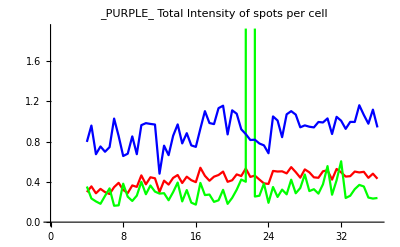

```mathematica
Grid[{ImageAdjust/@ColorCombine/@tempGapFillTrimsMeans}]
ptotIntensityTime = ListLinePlot[{Transpose[{mytimes,Flatten@(Total/@myRGaussInts)}],Transpose[{mytimes,Flatten@(Total/@myGGaussInts)}],Transpose[{mytimes,Flatten@(Total/@myBGaussInts)}]}, PlotStyle->{Red,Green,Blue}, PlotLabel->name<>" Total Intensity of spots per cell"]
```

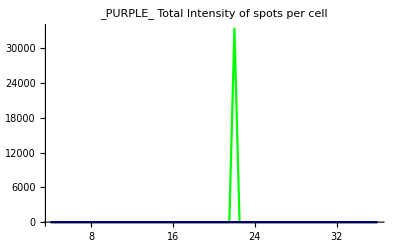

```mathematica
pavgIntensityTime = ListLinePlot[{Transpose[{mytimes,Flatten@(Mean/@myRGaussInts)}],Transpose[{mytimes,Flatten@(Mean/@myGGaussInts)}],Transpose[{mytimes,Flatten@(Mean/@myBGaussInts)}]}, PlotStyle->{Red,Green,Blue}, PlotLabel->name<>" Total Intensity of spots per cell", PlotRange->All]
```

#### Export it all:

```mathematica
myGapFilledPurpleSpotTrims=tempGapFillTrims;
myGapFilledPurpleSpotTrimsMeans=tempGapFillTrimsMeans;
myPurpleGausInts=tempdataframe ;
```

```mathematica
Export[analysisFolder<>name<>"_myGapFilledSpotTrims.m",tempGapFillTrims];
Export[analysisFolder<>name<>"_myGapFilledSpotTrimsMeans.m",tempGapFillTrimsMeans];
Export[analysisFolder<>name<>"_pIntensityTime.m",pIntensityTime];
Export[analysisFolder<>name<>"_myRGaussInts.m",tempdataframe];
```

### WHITE:

#### Rename

```mathematica
tempspots = myWhiteSpots;
temptrims = myWhiteSpotTrims;
name = "_WHITE_"
```

_WHITE_

#### Background Fill Time Points that have no spots

```mathematica
Length/@tempspots[[All]]
```

{17,19,18,15,16,17,14,12,17,15,12,14,11,16,14,12,17,12,15,11,8,10,11,15,10,7,7,10,9,11,6,6,6,8,5,7,6,5,9,9,9,6,6,4,3,4,5,7,5,4,2,5,4,3,5,1,4,2,0,1,2,3,1,2,1}

```mathematica
myBGFillPositions=Table[Nearest[(Position[Length/@temptrims[[All]],x_/;x>0])[[All,1]],(Position[Length/@temptrims[[All]],x_/;x==0])[[frame,1]]][[1]],{frame,1,Length@(Position[Length/@temptrims[[All]],x_/;x==0])[[All,1]],1}]
```

{58}

```mathematica
my0SpotPos=Flatten@(Position[Length/@temptrims[[All]],x_/;x==0])
```

{59}

```mathematica
edgeMask=Image[DiskMatrix[10,{15,15}]-DiskMatrix[3,{15,15}] ];
```

```mathematica
myBGFillPositions=Table[Nearest[(Position[Length/@temptrims[[All]],x_/;x>0])[[All,1]],(Position[Length/@temptrims[[All]],x_/;x==0])[[frame,1]]][[1]],{frame,1,Length@(Position[Length/@temptrims[[All]],x_/;x==0])[[All,1]],1}]
```

{58}

```mathematica
edgeMask=Image[DiskMatrix[10,{15,15}]-DiskMatrix[3,{15,15}] ];
```

```mathematica
theReplacements={};
myPosBGReplacements=Partition[Partition[Flatten@Table[
ImageData[temptrims[[myBGFillPositions]][[spot,1,color]]];
mytemp0s=Flatten@Position[Flatten[ImageData[ImageMultiply[edgeMask,#]]]&@temptrims[[myBGFillPositions]][[spot,1,color]],x_/;x==0];
myBgPixels=Flatten@Position[Flatten[ImageData[ImageMultiply[edgeMask,#]]]&@temptrims[[myBGFillPositions]][[spot,1,color]],x_/;x>0];
myRandomBGPixels=RandomChoice[myBgPixels,Length@mytemp0s];
mytempImgData=Flatten[ImageData[ImageMultiply[edgeMask,#]]]&@temptrims[[myBGFillPositions]][[spot,1,color]];
mytempChgList=Thread[mytemp0s-> mytempImgData[[myRandomBGPixels]]];
{(*myBGFillPositions[[spot]],*)Image[Partition[ReplacePart[mytempImgData,mytempChgList],15]]}
,{spot,1,Length@myBGFillPositions,1},{color,1,3,1}],3],1];
```

```mathematica
tempGapFillTrims=ReplacePart[temptrims,Thread[my0SpotPos-> myPosBGReplacements]];
```

```mathematica
Length@tempGapFillTrims
```

65

```mathematica
Dimensions/@tempGapFillTrims
```

{{17,3},{19,3},{18,3},{15,3},{16,3},{17,3},{14,3},{12,3},{17,3},{15,3},{12,3},{14,3},{11,3},{16,3},{14,3},{12,3},{17,3},{12,3},{15,3},{11,3},{8,3},{10,3},{11,3},{15,3},{10,3},{7,3},{7,3},{10,3},{9,3},{11,3},{6,3},{6,3},{6,3},{8,3},{5,3},{7,3},{6,3},{5,3},{9,3},{9,3},{9,3},{6,3},{6,3},{4,3},{3,3},{4,3},{5,3},{7,3},{5,3},{4,3},{2,3},{5,3},{4,3},{3,3},{5,3},{1,3},{4,3},{2,3},{1,3},{1,3},{2,3},{3,3},{1,3},{2,3},{1,3}}

#### Making Mean Crops

```mathematica
tempGapFillTrimsMeans=Table[Mean@tempGapFillTrims[[frame,All,color]],{frame,1,Length@tempGapFillTrims},{color,1,3,1}];
```

```mathematica
ImageAdjust/@tempGapFillTrimsMeans[[All,1]]
ImageAdjust/@tempGapFillTrimsMeans[[All,2]]
ImageAdjust/@tempGapFillTrimsMeans[[All,3]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Finding intensities with a Gaussian

```mathematica
myRGaussInts=GetTrimPeakIntFixedSigma[#,1.5]&/@tempGapFillTrims[[All,All,1]]//Table[Cases[Flatten[#[[i]],1], x_/;x>0],{i,1,Length@#,1}]&;
```

```mathematica
myGGaussInts=GetTrimPeakIntFixedSigma[#,1.5]&/@tempGapFillTrims[[All,All,2]]//Table[Cases[Flatten[#[[i]],1], x_/;x>0],{i,1,Length@#,1}]&;
```

```mathematica
myBGaussInts=GetTrimPeakIntFixedSigma[#,1.5]&/@tempGapFillTrims[[All,All,3]]//Table[Cases[Flatten[#[[i]],1], x_/;x>0],{i,1,Length@#,1}]&;
```

```mathematica
Total/@myRGaussInts
Total/@myGGaussInts
Total/@myBGaussInts
```

{0.339895,0.300531,0.323954,0.300997,0.299548,0.358139,0.22989,0.194255,0.290206,0.263873,0.167515,0.221855,0.168587,0.217602,0.195275,0.17153,0.258091,0.163133,0.261423,0.167181,0.136391,0.173261,0.151511,0.218621,0.17182,0.115159,0.104219,0.143349,0.129149,0.143535,0.0648292,0.105083,0.0947028,0.119695,0.102457,0.107319,0.0883117,0.0925913,0.158308,0.140394,0.16317,0.0932776,0.0864485,0.0501941,0.0402517,0.0445508,0.0858988,0.116237,0.0788508,0.0642704,0.0216159,0.0831332,0.0608296,0.0406426,0.0833991,0.0100354,0.0510649,0.0346651,0.00223685,0.00968317,0.0329926,0.0355088,0.0267976,0.044645,0.0406758}

{0.584608,0.682607,0.676156,0.573405,0.531121,0.496702,0.605244,0.337543,0.585516,0.526163,0.407946,0.480057,0.362775,0.461708,0.461295,0.376978,0.508909,0.369166,0.396305,0.421071,0.311489,0.311401,0.305786,0.381422,0.229851,0.14814,0.188249,0.267186,0.218253,0.301275,0.192277,0.215644,0.178622,0.253129,0.135745,0.178361,0.144446,0.141875,0.297369,0.173783,0.328114,0.239807,0.172812,0.107098,0.0705536,0.0727034,0.180045,0.150087,0.142559,0.0813837,0.0610564,0.143078,0.13054,0.0751808,0.164913,0.108726,0.103156,0.0804457,0.00932062,0.0117201,0.0376221,0.0368681,0.0200824,0.0159409,0.0151369}

{0.426845,0.442084,0.475056,0.477698,0.487344,0.551672,0.454264,0.379792,0.585985,0.565357,0.333173,0.470626,0.342964,0.447996,0.366239,0.372217,0.747194,0.540754,0.782983,0.497895,0.425612,0.511062,0.499623,0.647367,0.487022,0.39258,0.151478,0.271289,0.220076,0.288029,0.152846,0.171355,0.184262,0.256157,0.30458,0.3712,0.382677,0.385112,0.546194,0.429925,0.519036,0.143186,0.133988,0.274171,0.0865021,0.0693691,0.109262,0.174062,0.122502,0.0912515,0.0585588,0.125984,0.094239,0.0635004,0.0924605,0.0188331,0.0779931,0.051368,0,0.02158,0.0431073,0.0641562,0.0475717,0.0529736,0.0510337}

```mathematica
tempdataframe = {{{"myRGaussInts_>0"},{"myGGaussInts_>0"},{"myBGaussInts_>0"}},myRGaussInts,myGGaussInts,myBGaussInts};
```

#### Plotting Gaussian intensity over time

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

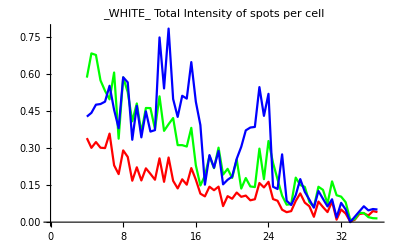

```mathematica
Grid[{ImageAdjust/@ColorCombine/@tempGapFillTrimsMeans}]
pIntensityTime = ListLinePlot[{Transpose[{mytimes,Flatten@(Total/@myRGaussInts)}],Transpose[{mytimes,Flatten@(Total/@myGGaussInts)}],Transpose[{mytimes,Flatten@(Total/@myBGaussInts)}]}, PlotStyle->{Red,Green,Blue}, PlotLabel->name<>" Total Intensity of spots per cell"]
```

#### Export it all:

```mathematica
myGapFilledWhiteSpotTrims=tempGapFillTrims;
myGapFilledWhiteSpotTrimsMeans=tempGapFillTrimsMeans;
myWhiteGausInts=tempdataframe ;
```

```mathematica
Export[analysisFolder<>name<>"_myGapFilledSpotTrims.m",tempGapFillTrims];
Export[analysisFolder<>name<>"_myGapFilledSpotTrimsMeans.m",tempGapFillTrimsMeans];
Export[analysisFolder<>name<>"_pIntensityTime.m",pIntensityTime];
Export[analysisFolder<>name<>"_myRGaussInts.m",tempdataframe];
```

### Done?

```mathematica
Finished == True
```

Finished==True

## Global HAR

```mathematica
ntFiles = FileNames["/Users/ccialek/Desktop/HAR cells/*/Analysis/MAX_NT*_countRYPWall.dat"]
tlFiles = FileNames["/Users/ccialek/Desktop/HAR cells/*/Analysis/MAX_TL*_countRYPWall.dat"]
taFiles = FileNames["/Users/ccialek/Desktop/HAR cells/*/Analysis/MAX_TA*_countRYPWall.dat"]
```

{}

{/Users/ccialek/Desktop/HAR cells/091018/Analysis/MAX_TL01har_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/091018/Analysis/MAX_TL02har_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/091018/Analysis/MAX_TL03har_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/091018/Analysis/MAX_TL04har_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/091018/Analysis/MAX_TL05har_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/092618/Analysis/MAX_TL12har_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/092618/Analysis/MAX_TL13har_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/092618/Analysis/MAX_TL14har_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/102418/Analysis/MAX_TL01harb_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/102418/Analysis/MAX_TL03hara_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/102418/Analysis/MAX_TL04harb_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/102418/Analysis/MAX_TL05harb_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/110318/Analysis/MAX_TL02harc_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/110318/Analysis/MAX_TL03harc_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/110318/Analysis/MAX_TL04harc_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/110318/Analysis/MAX_TL05harc_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/110318/Analysis/MAX_TL06harc_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/110318/Analysis/MAX_TL07harc_countRYPWall.dat}

{/Users/ccialek/Desktop/HAR cells/091018/Analysis/MAX_TA01har_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/091018/Analysis/MAX_TA02har_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/091018/Analysis/MAX_TA03har_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/091018/Analysis/MAX_TA04har_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/091018/Analysis/MAX_TA06har_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/091018/Analysis/MAX_TA07har_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/091018/Analysis/MAX_TA08har_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/091018/Analysis/MAX_TA09har_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/092618/Analysis/MAX_TA11har_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/092618/Analysis/MAX_TA12har_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/092618/Analysis/MAX_TA13har_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/092618/Analysis/MAX_TA14har_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/092618/Analysis/MAX_TA16har_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/092618/Analysis/MAX_TA17har_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/092618/Analysis/MAX_TA18har_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/092618/Analysis/MAX_TA20har_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/102418/Analysis/MAX_TA04_har_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/102418/Analysis/MAX_TA06_har_2cells_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/102418/Analysis/MAX_TA06_har_bottom_countRYPWall.dat}

### Spot counts

```mathematica
ntCounts= Table[<<(ntFiles[[i]]),{i,1,Length@ntFiles,1}];
tlCounts= Table[<<(tlFiles[[i]]),{i,1,Length@tlFiles,1}];
taCounts= Table[<<(taFiles[[i]]),{i,1,Length@taFiles,1}];
```

```mathematica
ntCountsTot=Total[ Table[ntCounts[[i]],{i,1,Length@ntCounts}]];
tlCountsTot=Total[ Table[tlCounts[[i]],{i,1,Length@tlCounts}]];
taCountsTot=Total[ Table[taCounts[[i]],{i,1,Length@taCounts}]];
Dimensions/@ntCountsTot
Dimensions/@tlCountsTot
Dimensions/@taCountsTot
```

{{5,2},{5,65,2}}

{{5,2},{5,65,2}}

{{5,2},{5,65,2}}

```mathematica
myTimes = ntCounts[[1,2,1,All,1]]
Length@myTimes
Length@ntCountsTot[[2,1,All,2]]
```

{-4,-3,-2,-1,0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60}

65

65

```mathematica
ntCountsTot[[1]]
```

{{5 mytimes,5 countRedOnly},{5 mytimes,5 countYellowOnly},{5 mytimes,5 countPurpleOnly},{5 mytimes,5 countWhiteOnly},{5 mytimes,5 total spot count}}

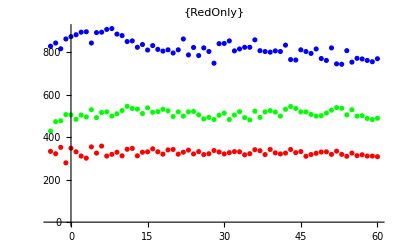

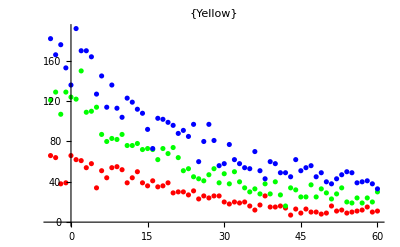

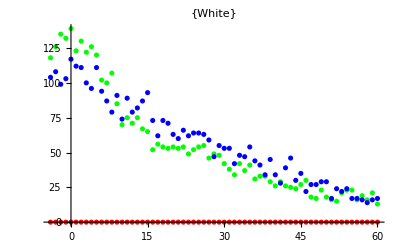

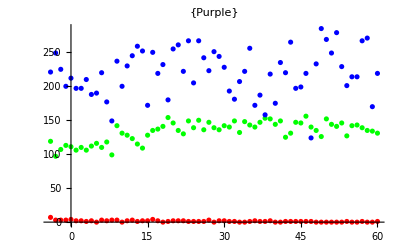

```mathematica
pRedNtTlTa=ListPlot[{Transpose[{myTimes,ntCountsTot[[2,1,All,2]]}],Transpose[{myTimes,tlCountsTot[[2,1,All,2]]}],Transpose[{myTimes,taCountsTot[[2,1,All,2]]}]},PlotStyle->{Red,Green,Blue},PlotLabel->{"RedOnly"}]
pRedNtTlTa=ListPlot[{Transpose[{myTimes,ntCountsTot[[2,2,All,2]]}],Transpose[{myTimes,tlCountsTot[[2,2,All,2]]}],Transpose[{myTimes,taCountsTot[[2,2,All,2]]}]},PlotStyle->{Red,Green,Blue},PlotLabel->{"Yellow"}]
pRedNtTlTa=ListPlot[{Transpose[{myTimes,ntCountsTot[[2,4,All,2]]}],Transpose[{myTimes,tlCountsTot[[2,4,All,2]]}],Transpose[{myTimes,taCountsTot[[2,4,All,2]]}]},PlotStyle->{Red,Green,Blue},PlotLabel->{"White"}]
pRedNtTlTa=ListPlot[{Transpose[{myTimes,ntCountsTot[[2,3,All,2]]}],Transpose[{myTimes,tlCountsTot[[2,3,All,2]]}],Transpose[{myTimes,taCountsTot[[2,3,All,2]]}]},PlotStyle->{Red,Green,Blue},PlotLabel->{"Purple"}]
```

## Intensities from gaussian fits HAR

### Import:

```mathematica
ntYFiles = FileNames["/Users/ccialek/Desktop/HAR cells/*/Analysis/MAX_NT*YELLOW__myRGaussInts.m"];
tlYFiles = FileNames["/Users/ccialek/Desktop/HAR cells/*/Analysis/MAX_TL*YELLOW__myRGaussInts.m"];
taYFiles = FileNames["/Users/ccialek/Desktop/HAR cells/*/Analysis/MAX_TA*YELLOW__myRGaussInts.m"];
```

```mathematica
ntWFiles = FileNames["/Users/ccialek/Desktop/HAR cells/*/Analysis/MAX_NT*WHITE__myRGaussInts.m"];
tlWFiles = FileNames["/Users/ccialek/Desktop/HAR cells/*/Analysis/MAX_TL*WHITE__myRGaussInts.m"];
taWFiles = FileNames["/Users/ccialek/Desktop/HAR cells/*/Analysis/MAX_TA*WHITE__myRGaussInts.m"];
```

```mathematica
ntPFiles = FileNames["/Users/ccialek/Desktop/HAR cells/*/Analysis/MAX_NT*PURPLE__myRGaussInts.m"];
tlPFiles = FileNames["/Users/ccialek/Desktop/HAR cells/*/Analysis/MAX_TL*PURPLE__myRGaussInts.m"];
taPFiles = FileNames["/Users/ccialek/Desktop/HAR cells/*/Analysis/MAX_TA*PURPLE__myRGaussInts.m"];
```

```mathematica
Length@ntYFiles
Length@tlYFiles
Length@taYFiles
movieLength = Length@taYInts0[[1,2]]
```

5

18

19

65

Below is the previous code blocked out... if the filter step (import then filter spots greater than 2) doesn’t work then go back to this OG code

```mathematica
(*
ntYInts= Table[<<(ntYFiles[[i]]),{i,1,Length@ntYFiles,1}];
tlYInts= Table[<<(tlYFiles[[i]]),{i,1,Length@tlYFiles,1}];
taYInts= Table[<<(taYFiles[[i]]),{i,1,Length@taYFiles,1}];
ntWInts= Table[<<(ntWFiles[[i]]),{i,1,Length@ntWFiles,1}];
tlWInts= Table[<<(tlWFiles[[i]]),{i,1,Length@tlWFiles,1}];
taWInts= Table[<<(taWFiles[[i]]),{i,1,Length@taWFiles,1}];
ntPInts= Table[<<(ntPFiles[[i]]),{i,1,Length@ntPFiles,1}];
tlPInts= Table[<<(tlPFiles[[i]]),{i,1,Length@tlPFiles,1}];
taPInts= Table[<<(taPFiles[[i]]),{i,1,Length@taPFiles,1}];
*)
```

```mathematica
ntYInts0= Table[<<(ntYFiles[[i]]),{i,1,Length@ntYFiles,1}];
tlYInts0= Table[<<(tlYFiles[[i]]),{i,1,Length@tlYFiles,1}];
taYInts0= Table[<<(taYFiles[[i]]),{i,1,Length@taYFiles,1}];
ntWInts0= Table[<<(ntWFiles[[i]]),{i,1,Length@ntWFiles,1}];
tlWInts0= Table[<<(tlWFiles[[i]]),{i,1,Length@tlWFiles,1}];
taWInts0= Table[<<(taWFiles[[i]]),{i,1,Length@taWFiles,1}];
ntPInts0= Table[<<(ntPFiles[[i]]),{i,1,Length@ntPFiles,1}];
tlPInts0= Table[<<(tlPFiles[[i]]),{i,1,Length@tlPFiles,1}];
taPInts0= Table[<<(taPFiles[[i]]),{i,1,Length@taPFiles,1}];
```

This line filters out the crazy intensities...
It crops out headers but adds them back in so data structure is the same as before

```mathematica
ntYInts= Table[ Join[{ntYInts0[[1,1]]}, Table[Table[Select[ntYInts0[[cell,channel,frame]],#<2&],{frame,1,movieLength}],{channel,2,4}]] ,{cell,1,Length@ntYInts0}];
tlYInts= Table[ Join[{ntYInts0[[1,1]]}, Table[Table[Select[tlYInts0[[cell,channel,frame]],#<2&],{frame,1,movieLength}],{channel,2,4}]] ,{cell,1,Length@tlYInts0}];
taYInts= Table[ Join[{ntYInts0[[1,1]]}, Table[Table[Select[taYInts0[[cell,channel,frame]],#<2&],{frame,1,movieLength}],{channel,2,4}]] ,{cell,1,Length@taYInts0}];
ntWInts= Table[ Join[{ntYInts0[[1,1]]}, Table[Table[Select[ntWInts0[[cell,channel,frame]],#<2&],{frame,1,movieLength}],{channel,2,4}]] ,{cell,1,Length@ntWInts0}];
tlWInts= Table[ Join[{ntYInts0[[1,1]]}, Table[Table[Select[tlWInts0[[cell,channel,frame]],#<2&],{frame,1,movieLength}],{channel,2,4}]] ,{cell,1,Length@tlWInts0}];
taWInts= Table[ Join[{ntYInts0[[1,1]]}, Table[Table[Select[taWInts0[[cell,channel,frame]],#<2&],{frame,1,movieLength}],{channel,2,4}]] ,{cell,1,Length@taWInts0}];
ntPInts= Table[ Join[{ntYInts0[[1,1]]}, Table[Table[Select[ntPInts0[[cell,channel,frame]],#<2&],{frame,1,movieLength}],{channel,2,4}]],{cell,1,Length@ntPInts0}];
tlPInts= Table[ Join[{ntYInts0[[1,1]]}, Table[Table[Select[tlPInts0[[cell,channel,frame]],#<2&],{frame,1,movieLength}],{channel,2,4}]] ,{cell,1,Length@tlPInts0}];
taPInts= Table[ Join[{ntYInts0[[1,1]]}, Table[Table[Select[taPInts0[[cell,channel,frame]],#<2&],{frame,1,movieLength}],{channel,2,4}]] ,{cell,1,Length@taPInts0}];
```

```mathematica
ntYInts[[1,1]]
ntYInts0[[1,1]]
```

{{myRGaussInts_>0},{myGGaussInts_>0},{myBGaussInts_>0}}

{{myRGaussInts_>0},{myGGaussInts_>0},{myBGaussInts_>0}}

### FUTURE: DEV THIS INTO A FILTER STEP!! Visualize to filter (ONLY filtering nonzeros up to this point...)

```mathematica
ListPlot[{Flatten@ntInts[[1,2]],Flatten@ntInts[[2,2]],Flatten@ntInts[[3,2]],Flatten@ntInts[[4,2]],Flatten@ntInts[[5,2]]},PlotStyle->Red,PlotRange->All]
ListPlot[{Flatten@ntInts[[1,3]],Flatten@ntInts[[2,3]],Flatten@ntInts[[3,3]],Flatten@ntInts[[4,3]],Flatten@ntInts[[5,3]]},PlotStyle->Green,PlotRange->All]
ListPlot[{Flatten@ntInts[[1,4]],Flatten@ntInts[[2,4]],Flatten@ntInts[[3,4]],Flatten@ntInts[[4,4]],Flatten@ntInts[[5,4]]},PlotStyle->Blue,PlotRange->All]
```

Part::partd: Part specification ntInts⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification ntInts⟦2,2⟧ is longer than depth of object.

Part::partd: Part specification ntInts⟦3,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

Part::partd: Part specification ntInts⟦1,3⟧ is longer than depth of object.

Part::partd: Part specification ntInts⟦2,3⟧ is longer than depth of object.

Part::partd: Part specification ntInts⟦3,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

Part::partd: Part specification ntInts⟦1,4⟧ is longer than depth of object.

Part::partd: Part specification ntInts⟦2,4⟧ is longer than depth of object.

Part::partd: Part specification ntInts⟦3,4⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

```mathematica
redmean = Mean@Flatten@{ntInts[[1,2]],ntInts[[2,2]],ntInts[[3,2]],ntInts[[4,2]],ntInts[[5,2]]}
stdev2 = 2*StandardDeviation@Flatten@{ntInts[[1,2]],ntInts[[2,2]],ntInts[[3,2]],ntInts[[4,2]],ntInts[[5,2]]}
```

Part::partd: Part specification ntInts⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification ntInts⟦2,2⟧ is longer than depth of object.

Part::partd: Part specification ntInts⟦3,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

1/5 (ntInts⟦1,2⟧+ntInts⟦2,2⟧+ntInts⟦3,2⟧+ntInts⟦4,2⟧+ntInts⟦5,2⟧)

Part::partd: Part specification ntInts⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification ntInts⟦2,2⟧ is longer than depth of object.

Part::partd: Part specification ntInts⟦3,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

1/(√5)(√(Conjugate[ntInts⟦1,2⟧] (4 ntInts⟦1,2⟧-ntInts⟦2,2⟧-ntInts⟦3,2⟧-ntInts⟦4,2⟧-ntInts⟦5,2⟧)+Conjugate[ntInts⟦2,2⟧] (-ntInts⟦1,2⟧+4 ntInts⟦2,2⟧-ntInts⟦3,2⟧-ntInts⟦4,2⟧-ntInts⟦5,2⟧)+Conjugate[ntInts⟦3,2⟧] (-ntInts⟦1,2⟧-ntInts⟦2,2⟧+4 ntInts⟦3,2⟧-ntInts⟦4,2⟧-ntInts⟦5,2⟧)+Conjugate[ntInts⟦4,2⟧] (-ntInts⟦1,2⟧-ntInts⟦2,2⟧-ntInts⟦3,2⟧+4 ntInts⟦4,2⟧-ntInts⟦5,2⟧)+Conjugate[ntInts⟦5,2⟧] (-ntInts⟦1,2⟧-ntInts⟦2,2⟧-ntInts⟦3,2⟧-ntInts⟦4,2⟧+4 ntInts⟦5,2⟧)))

```mathematica
greenmean = Mean@Flatten@{ntInts[[1,3]],ntInts[[2,3]],ntInts[[3,3]],ntInts[[4,3]],ntInts[[5,3]]}
stdev2 = 2*StandardDeviation@Flatten@{ntInts[[1,3]],ntInts[[2,3]],ntInts[[3,3]],ntInts[[4,3]],ntInts[[5,3]]}
```

Part::partd: Part specification ntInts⟦1,3⟧ is longer than depth of object.

Part::partd: Part specification ntInts⟦2,3⟧ is longer than depth of object.

Part::partd: Part specification ntInts⟦3,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

1/5 (ntInts⟦1,3⟧+ntInts⟦2,3⟧+ntInts⟦3,3⟧+ntInts⟦4,3⟧+ntInts⟦5,3⟧)

Part::partd: Part specification ntInts⟦1,3⟧ is longer than depth of object.

Part::partd: Part specification ntInts⟦2,3⟧ is longer than depth of object.

Part::partd: Part specification ntInts⟦3,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

1/(√5)(√(Conjugate[ntInts⟦1,3⟧] (4 ntInts⟦1,3⟧-ntInts⟦2,3⟧-ntInts⟦3,3⟧-ntInts⟦4,3⟧-ntInts⟦5,3⟧)+Conjugate[ntInts⟦2,3⟧] (-ntInts⟦1,3⟧+4 ntInts⟦2,3⟧-ntInts⟦3,3⟧-ntInts⟦4,3⟧-ntInts⟦5,3⟧)+Conjugate[ntInts⟦3,3⟧] (-ntInts⟦1,3⟧-ntInts⟦2,3⟧+4 ntInts⟦3,3⟧-ntInts⟦4,3⟧-ntInts⟦5,3⟧)+Conjugate[ntInts⟦4,3⟧] (-ntInts⟦1,3⟧-ntInts⟦2,3⟧-ntInts⟦3,3⟧+4 ntInts⟦4,3⟧-ntInts⟦5,3⟧)+Conjugate[ntInts⟦5,3⟧] (-ntInts⟦1,3⟧-ntInts⟦2,3⟧-ntInts⟦3,3⟧-ntInts⟦4,3⟧+4 ntInts⟦5,3⟧)))

```mathematica
bluemean = Mean@Flatten@{ntInts[[1,4]],ntInts[[2,4]],ntInts[[3,4]],ntInts[[4,4]],ntInts[[5,4]]}
stdev2 = 2*StandardDeviation@Flatten@{ntInts[[1,4]],ntInts[[2,4]],ntInts[[3,4]],ntInts[[4,4]],ntInts[[5,4]]}
```

Part::partd: Part specification ntInts⟦1,4⟧ is longer than depth of object.

Part::partd: Part specification ntInts⟦2,4⟧ is longer than depth of object.

Part::partd: Part specification ntInts⟦3,4⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

1/5 (ntInts⟦1,4⟧+ntInts⟦2,4⟧+ntInts⟦3,4⟧+ntInts⟦4,4⟧+ntInts⟦5,4⟧)

Part::partd: Part specification ntInts⟦1,4⟧ is longer than depth of object.

Part::partd: Part specification ntInts⟦2,4⟧ is longer than depth of object.

Part::partd: Part specification ntInts⟦3,4⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

1/(√5)(√(Conjugate[ntInts⟦1,4⟧] (4 ntInts⟦1,4⟧-ntInts⟦2,4⟧-ntInts⟦3,4⟧-ntInts⟦4,4⟧-ntInts⟦5,4⟧)+Conjugate[ntInts⟦2,4⟧] (-ntInts⟦1,4⟧+4 ntInts⟦2,4⟧-ntInts⟦3,4⟧-ntInts⟦4,4⟧-ntInts⟦5,4⟧)+Conjugate[ntInts⟦3,4⟧] (-ntInts⟦1,4⟧-ntInts⟦2,4⟧+4 ntInts⟦3,4⟧-ntInts⟦4,4⟧-ntInts⟦5,4⟧)+Conjugate[ntInts⟦4,4⟧] (-ntInts⟦1,4⟧-ntInts⟦2,4⟧-ntInts⟦3,4⟧+4 ntInts⟦4,4⟧-ntInts⟦5,4⟧)+Conjugate[ntInts⟦5,4⟧] (-ntInts⟦1,4⟧-ntInts⟦2,4⟧-ntInts⟦3,4⟧-ntInts⟦4,4⟧+4 ntInts⟦5,4⟧)))

```mathematica
mean+stdev2
mean-stdev2
```

mean+1/(√5)(√(Conjugate[ntInts⟦1,4⟧] (4 ntInts⟦1,4⟧-ntInts⟦2,4⟧-ntInts⟦3,4⟧-ntInts⟦4,4⟧-ntInts⟦5,4⟧)+Conjugate[ntInts⟦2,4⟧] (-ntInts⟦1,4⟧+4 ntInts⟦2,4⟧-ntInts⟦3,4⟧-ntInts⟦4,4⟧-ntInts⟦5,4⟧)+Conjugate[ntInts⟦3,4⟧] (-ntInts⟦1,4⟧-ntInts⟦2,4⟧+4 ntInts⟦3,4⟧-ntInts⟦4,4⟧-ntInts⟦5,4⟧)+Conjugate[ntInts⟦4,4⟧] (-ntInts⟦1,4⟧-ntInts⟦2,4⟧-ntInts⟦3,4⟧+4 ntInts⟦4,4⟧-ntInts⟦5,4⟧)+Conjugate[ntInts⟦5,4⟧] (-ntInts⟦1,4⟧-ntInts⟦2,4⟧-ntInts⟦3,4⟧-ntInts⟦4,4⟧+4 ntInts⟦5,4⟧)))

mean-1/(√5)(√(Conjugate[ntInts⟦1,4⟧] (4 ntInts⟦1,4⟧-ntInts⟦2,4⟧-ntInts⟦3,4⟧-ntInts⟦4,4⟧-ntInts⟦5,4⟧)+Conjugate[ntInts⟦2,4⟧] (-ntInts⟦1,4⟧+4 ntInts⟦2,4⟧-ntInts⟦3,4⟧-ntInts⟦4,4⟧-ntInts⟦5,4⟧)+Conjugate[ntInts⟦3,4⟧] (-ntInts⟦1,4⟧-ntInts⟦2,4⟧+4 ntInts⟦3,4⟧-ntInts⟦4,4⟧-ntInts⟦5,4⟧)+Conjugate[ntInts⟦4,4⟧] (-ntInts⟦1,4⟧-ntInts⟦2,4⟧-ntInts⟦3,4⟧+4 ntInts⟦4,4⟧-ntInts⟦5,4⟧)+Conjugate[ntInts⟦5,4⟧] (-ntInts⟦1,4⟧-ntInts⟦2,4⟧-ntInts⟦3,4⟧-ntInts⟦4,4⟧+4 ntInts⟦5,4⟧)))

```mathematica
Histogram[Flatten@{ntInts[[1,3]],ntInts[[2,3]],ntInts[[3,3]],ntInts[[4,3]],ntInts[[5,3]]}, ChartStyle->Green]
Histogram[Flatten@{ntInts[[1,4]],ntInts[[2,4]],ntInts[[3,4]],ntInts[[4,4]],ntInts[[5,4]]},100000, ChartStyle->Blue]
```

Part::partd: Part specification ntInts⟦1,3⟧ is longer than depth of object.

Part::partd: Part specification ntInts⟦2,3⟧ is longer than depth of object.

Part::partd: Part specification ntInts⟦3,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

Part::partd: Part specification ntInts⟦1,4⟧ is longer than depth of object.

Part::partd: Part specification ntInts⟦2,4⟧ is longer than depth of object.

Part::partd: Part specification ntInts⟦3,4⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

### Total and count intensities

need to filter out shithead intensts out of blue

```mathematica
(*ntYInts=Table[Table[Select[ntYInts0[[All,channel,frame]],#<5&],{channel,2,4,1}],{frame,1,movieLength,1}];
```

```mathematica
Dimensions@ntYInts
Dimensions/@ntYInts0[[1]]
```

{5,4}

{{3,1},{65},{65},{65}}

{{3,1},{65},{65},{65}}

{65}

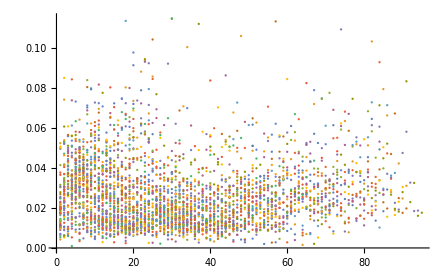

```mathematica
Dimensions/@tlWInts[[1]]
Dimensions@ Table[Flatten[tlWInts[[All,3,frame]],1],{frame,1,65,1}]
 Table[Flatten[taWInts[[All,3,frame]],1],{frame,1,65,1}]//ListPlot[#,PlotRange->All]&
```

```mathematica
Select[{1,2,4,7,6,2},#>2&]
```

{4,7,6}

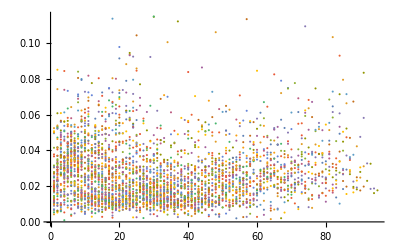
-Graphics--Graphics-

```mathematica
Row[{ Table[Flatten[taWInts[[All,3,frame]],1],{frame,1,65,1}]//ListPlot[#,PlotRange->All, ImageSize->400]&,
Table[Select[Flatten[taWInts[[All,3,frame]],1],#<2&],{frame,1,65,1}]//ListPlot[#,PlotRange->All,ImageSize->400]&  }]
(*This is showing that without filtering I'm getting some crazy intensities.... *)
```

```mathematica
ntYIntsTotRGB= Table[Table[Total@(Total/@ntYInts[[All,j,i]]),{i,1,Length@ntYInts[[1,2]],1}],{j,2,Length@ntYInts[[2]],1}];
tlYIntsTotRGB= Table[Table[Total@(Total/@tlYInts[[All,j,i]]),{i,1,Length@tlYInts[[1,2]],1}],{j,2,Length@tlYInts[[2]],1}];
taYIntsTotRGB= Table[Table[Total@(Total/@taYInts[[All,j,i]]),{i,1,Length@taYInts[[1,2]],1}],{j,2,Length@taYInts[[2]],1}];
```

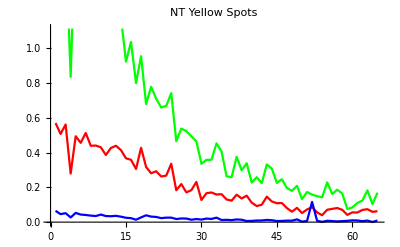

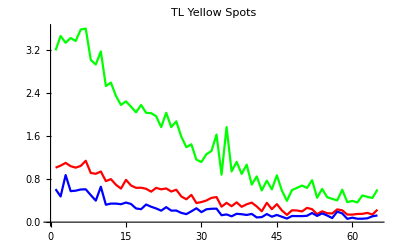

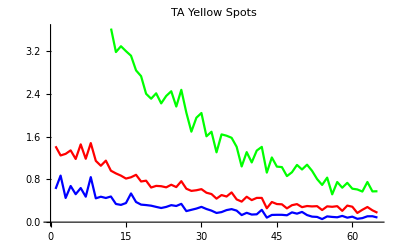

```mathematica
ListLinePlot[ntYIntsTotRGB,PlotStyle->{Red,Green,Blue},PlotLabel->"NT Yellow Spots"]
ListLinePlot[tlYIntsTotRGB,PlotStyle->{Red,Green,Blue},PlotRange->All,PlotLabel->"TL Yellow Spots"]
ListLinePlot[taYIntsTotRGB,PlotStyle->{Red,Green,Blue},PlotLabel->"TA Yellow Spots"]
```

```mathematica
ntWIntsTotRGB= Table[Table[Total@(Total/@ntWInts[[All,j,i]]),{i,1,Length@ntWInts[[1,2]],1}],{j,2,Length@ntWInts[[2]],1}];
tlWIntsTotRGB= Table[Table[Total@(Total/@tlWInts[[All,j,i]]),{i,1,Length@tlWInts[[1,2]],1}],{j,2,Length@tlWInts[[2]],1}];
taWIntsTotRGB= Table[Table[Total@(Total/@taWInts[[All,j,i]]),{i,1,Length@taWInts[[1,2]],1}],{j,2,Length@taWInts[[2]],1}];
```

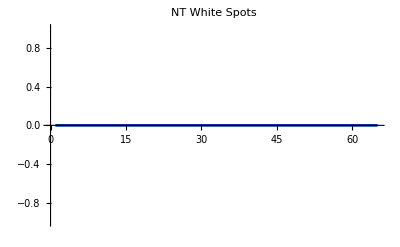

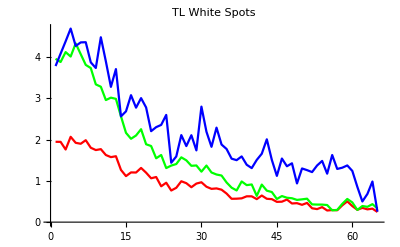

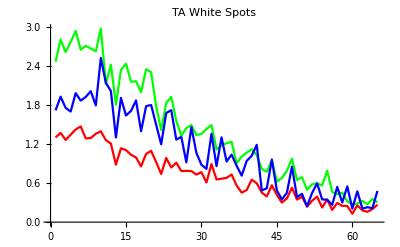

```mathematica
ListLinePlot[ntWIntsTotRGB,PlotStyle->{Red,Green,Blue},PlotLabel->"NT White Spots"]
ListLinePlot[tlWIntsTotRGB,PlotStyle->{Red,Green,Blue},PlotLabel->"TL White Spots",PlotRange->All]
ListLinePlot[taWIntsTotRGB,PlotStyle->{Red,Green,Blue},PlotLabel->"TA White Spots"]
```

### Find and subtract out the immobile fraction, and normalize to start at 1 Replot Total and count intensities

## Yellow spots

#### Input:

```mathematica
myTimes = ntCounts[[1,2,1,All,1]]*60;
Length@myTimes
Length@ntCountsTot[[2,1,All,2]]
```

65

65

```mathematica
(*green intensity *) ntGIntsY0 = Table[Total@(Total/@ntYInts[[All,3,i]] ),{i,1,Length@ntYInts[[1,2]],1}];
(*green intensity *) tlGIntsY0 = Table[Total@(Total/@tlYInts[[All,3,i]]),{i,1,Length@tlYInts[[1,2]],1}];
(*green intensity *) taGIntsY0 = Table[Total@(Total/@taYInts[[All,3,i]]),{i,1,Length@taYInts[[1,2]],1}];
```

#### FIRST, find the Immobile Fraction and subtract that out of the Y value...

#### NT: calculating immobile fraction MANUAL INPUT: Set where you want the Immobile Fraction to be...

```mathematica
mySpots = ntGIntsY0
```

{1.61514,1.73256,1.61662,0.836033,1.72787,1.43641,1.51469,1.24759,1.27531,1.46769,1.19638,1.14925,1.29907,1.1793,0.923426,1.03679,0.800207,0.954784,0.679285,0.778772,0.710761,0.659682,0.668734,0.742418,0.465323,0.538357,0.523707,0.493819,0.464715,0.335595,0.358115,0.358923,0.453089,0.406628,0.263608,0.258656,0.376047,0.298814,0.338545,0.227547,0.258613,0.224536,0.332408,0.307508,0.225597,0.246716,0.196889,0.179673,0.208745,0.132624,0.173446,0.158601,0.149471,0.142966,0.228695,0.162471,0.186314,0.164606,0.0760099,0.0846173,0.109773,0.124528,0.182509,0.103962,0.169009}

```mathematica
Mean[mySpots[[40;;All]]]
immobileFraction = Mean[mySpots[[45;;All]]]
Mean[mySpots[[50;;All]]]
Mean[mySpots[[55;;All]]]
```

0.182994

0.162249

0.14685

0.144772

```mathematica
ntGIntsY00 = mySpots-immobileFraction ;
```

#### TL: calculating immobile fraction MANUAL INPUT: Set where you want the Immobile Fraction to be...

```mathematica
mySpots = tlGIntsY0;
```

```mathematica
Mean[mySpots[[40;;All]]]
immobileFraction = Mean[mySpots[[45;;All]]]
Mean[mySpots[[50;;All]]]
Mean[mySpots[[55;;All]]]
```

0.570871

0.539127

0.514578

0.46037

```mathematica
tlGIntsY00 = mySpots-immobileFraction ;
```

#### TA: calculating immobile fraction MANUAL INPUT: Set where you want the Immobile Fraction to be...

```mathematica
mySpots = taGIntsY0;
```

```mathematica
Mean[mySpots[[40;;All]]]
immobileFraction = Mean[mySpots[[45;;All]]]
Mean[mySpots[[50;;All]]]
Mean[mySpots[[55;;All]]]
```

0.873102

0.794609

0.73389

0.655616

```mathematica
taGIntsY00 = mySpots-immobileFraction ;
```

#### Normalizing Intensity...

```mathematica
(*normalized green intensity *) ntGIntsY = ntGIntsY00 /Mean[ntGIntsY00[[1;;7]]];
(*normalized green intensity *) tlGIntsY = tlGIntsY00 /Mean[tlGIntsY00[[1;;7]]];
(*normalized green intensity *)   taGIntsY =  taGIntsY00/Mean[taGIntsY00[[1;;7]]];
```

```mathematica
(*normalized green intensity *) ntGIntsYTime = Transpose[{myTimes,ntGIntsY}] 
(*normalized green intensity *) tlGIntsYTime =  Transpose[{myTimes,tlGIntsY}];
(*normalized green intensity *)   taGIntsYTime =   Transpose[{myTimes,taGIntsY}];
```

{{-240,1.08847},{-180,1.17644},{-120,1.08959},{-60,0.504784},{0,1.17293},{60,0.954571},{120,1.01322},{180,0.813116},{240,0.83388},{300,0.978009},{360,0.774751},{420,0.739442},{480,0.851683},{540,0.761955},{600,0.570257},{660,0.655185},{720,0.477944},{780,0.593749},{840,0.387352},{900,0.461886},{960,0.410933},{1020,0.372666},{1080,0.379447},{1140,0.43465},{1200,0.227057},{1260,0.281772},{1320,0.270797},{1380,0.248405},{1440,0.226601},{1500,0.129867},{1560,0.146739},{1620,0.147344},{1680,0.217891},{1740,0.183084},{1800,0.075936},{1860,0.0722265},{1920,0.160173},{1980,0.102312},{2040,0.132077},{2100,0.0489202},{2160,0.0721941},{2220,0.0466641},{2280,0.127479},{2340,0.108825},{2400,0.047459},{2460,0.0632811},{2520,0.0259519},{2580,0.0130539},{2640,0.0348337},{2700,-0.0221944},{2760,0.00838883},{2820,-0.00273302},{2880,-0.00957299},{2940,-0.0144459},{3000,0.0497799},{3060,0.000166889},{3120,0.0180293},{3180,0.00176619},{3240,-0.0646081},{3300,-0.0581597},{3360,-0.0393136},{3420,-0.0282593},{3480,0.0151788},{3540,-0.043667},{3600,0.00506438}}

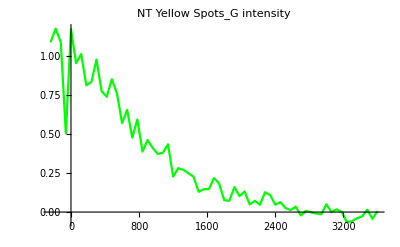

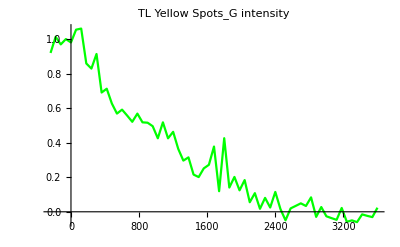

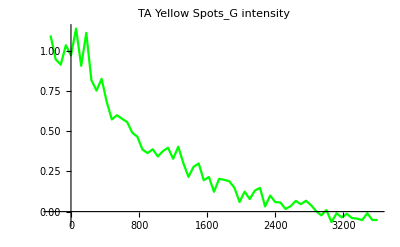

```mathematica
pNT = ListLinePlot[ntGIntsYTime,PlotStyle->{Green},PlotLabel->"NT Yellow Spots_G intensity"]
pTL = ListLinePlot[tlGIntsYTime,PlotStyle->{Green},PlotLabel->"TL Yellow Spots_G intensity"]
pTA = ListLinePlot[taGIntsYTime,PlotStyle->{Green},PlotLabel->"TA Yellow Spots_G intensity"]
```

#### Define tag and protein lengths in AAs

```mathematica
l2 = (1010/3)//N   (*Length of smFLAG tag in AAs*)
l1 = (4645/3)//N   (*Length of KDM5B in AAs*)
```

336.667

1548.33

```mathematica
fraction = (l1/(l1+l2/2))   (*Once the fluorescence drops by this much, this is t0*)
```

0.901942

#### Select the data that falls within the linear range: l1/(l1+l2/2) --> linear part MANUAL INPUT: Set what you want the data range to be...

```mathematica
(*Selecct the LINEAR range of hte graph above by looking at where it's linear and fittable and plugging the start and stop of this range into RangeA and RangeB *)
```

```mathematica
ntrangeA = 10;
ntrangeB = 30;
ntRangedata =  ntGIntsYTime[[ntrangeA ;; ntrangeB ]]
```

{{300,0.978009},{360,0.774751},{420,0.739442},{480,0.851683},{540,0.761955},{600,0.570257},{660,0.655185},{720,0.477944},{780,0.593749},{840,0.387352},{900,0.461886},{960,0.410933},{1020,0.372666},{1080,0.379447},{1140,0.43465},{1200,0.227057},{1260,0.281772},{1320,0.270797},{1380,0.248405},{1440,0.226601},{1500,0.129867}}

```mathematica
tlrangeA = 8;
tlrangeB = 28;
tlRangedata =  tlGIntsYTime[[tlrangeA ;; tlrangeB ]]
```

{{180,0.859118},{240,0.829382},{300,0.914083},{360,0.690737},{420,0.712767},{480,0.627495},{540,0.568808},{600,0.591617},{660,0.557312},{720,0.521199},{780,0.568665},{840,0.518189},{900,0.515922},{960,0.495744},{1020,0.425709},{1080,0.518133},{1140,0.425512},{1200,0.463108},{1260,0.364302},{1320,0.2965},{1380,0.315148}}

```mathematica
tarangeA = 9;
tarangeB = 24;
taRangedata =  taGIntsYTime[[tarangeA ;; tarangeB ]]
```

{{240,0.816568},{300,0.751764},{360,0.824831},{420,0.681321},{480,0.572624},{540,0.598819},{600,0.576614},{660,0.556147},{720,0.490479},{780,0.46463},{840,0.385518},{900,0.363398},{960,0.387641},{1020,0.34248},{1080,0.375842},{1140,0.396866}}

### Fit to the rate of elongation

#### NT: Fit and calculate elongation rate

```mathematica
fdata = ntRangedata;
```

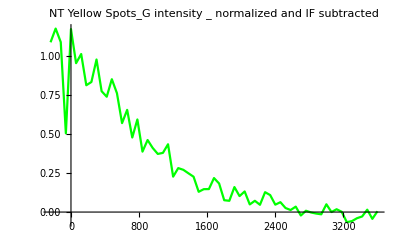

```mathematica
pfdata = ListLinePlot[ntGIntsYTime,PlotStyle->{Green},PlotLabel->"NT Yellow Spots_G intensity _ normalized and IF subtracted"]
```

equation : y (ke, b) =  -ke/(L1 + L2/2)t +b

```mathematica
Clear@b
Clear@temp
Clear@ke
```

```mathematica
nlm=NonlinearModelFit[fdata ,-ke/(l1 + l2/2)t + b, {{ke},{b}},t]
```

FittedModel[1.02507-0.000597458 t]

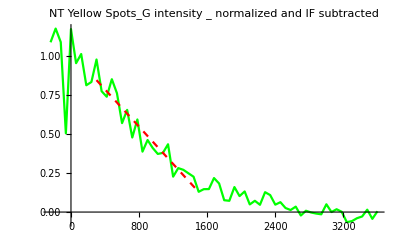

```mathematica
Show[pfdata, Plot[nlm[t],{t,(ntrangeA-5)*60,(ntrangeB-5)*60}, PlotStyle->{Red,Dashed},PlotLegends->Normal[nlm]]]
```

```mathematica
nlm["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
ke | 1.02564 | 0.0769621 | {0.864553,1.18672}
b | 1.02507 | 0.0435127 | {0.933992,1.11614}

```mathematica
(*Confidence interval of the first element of the confidence, divide by 2 because it's + or - *)
confinterval = Differences@nlm["ParameterConfidenceIntervals"][[1]]/2
```

{0.161084}

```mathematica
elongationrate =  PlusMinus[nlm["BestFitParameters"][[1,2]],confinterval[[1]]]
```

1.02564±0.161084

#### TL: Fit and calculate elongation rate

```mathematica
fdata = tlRangedata;
```

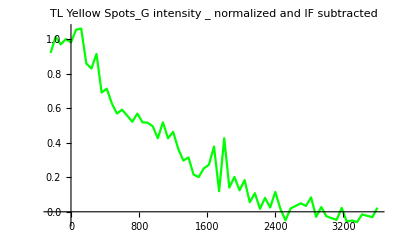

```mathematica
pfdata = ListLinePlot[tlGIntsYTime,PlotStyle->{Green},PlotLabel->"TL Yellow Spots_G intensity _ normalized and IF subtracted"]
```

equation : y (ke, b) =  -ke/(L1 + L2/2)t +b

```mathematica
nlm=NonlinearModelFit[fdata ,-ke/(l1 + l2/2)t + b, {{ke},{b}},t]
```

FittedModel[0.889192-0.000420853 t]

```mathematica
60*(tarangeA+5) ;; 60*(tarangeB + 5)
```

840;;1740

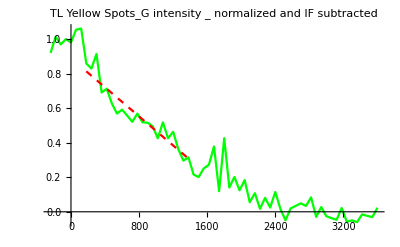

```mathematica
Show[pfdata, Plot[nlm[t],{t,(tlrangeA-5)*60,(tlrangeB-5)*60}, PlotStyle->{Red,Dashed},PlotLegends->Normal[nlm]]]
```

```mathematica
nlm["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
ke | 0.722465 | 0.0611546 | {0.594467,0.850463}
b | 0.889192 | 0.0306532 | {0.825034,0.95335}

```mathematica
(*Confidence interval of the first element of the confidence, divide by 2 because it's + or - *)
confinterval = Differences@nlm["ParameterConfidenceIntervals"][[1]]/2
```

{0.127998}

```mathematica
elongationrate =  PlusMinus[nlm["BestFitParameters"][[1,2]],confinterval[[1]]] (*AA per sec*)
```

0.722465±0.127998

#### TA: Fit and calculate elongation rate

```mathematica
fdata = taRangedata;
```

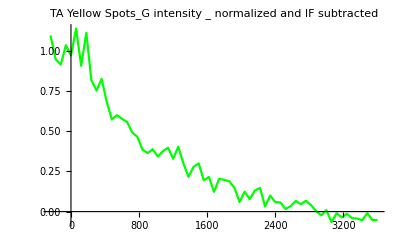

```mathematica
pfdata = ListLinePlot[taGIntsYTime,PlotStyle->{Green},PlotLabel->"TA Yellow Spots_G intensity _ normalized and IF subtracted"]
```

equation : y (ke, b) =  -ke/(L1 + L2/2)t +b

```mathematica
nlm=NonlinearModelFit[fdata ,-ke/(l1 + l2/2)t + b, {{ke},{b}},t]
```

FittedModel[0.909741-0.000540789 t]

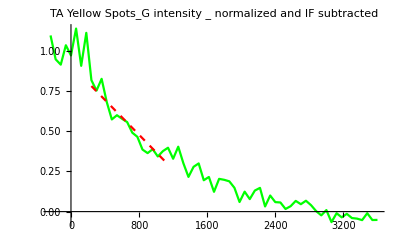

```mathematica
Show[pfdata, Plot[nlm[t],{t,(tarangeA-5)*60,(tarangeB-5)*60}, PlotStyle->{Red,Dashed},PlotLegends->Normal[nlm]]]
```

```mathematica
nlm["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
ke | 0.928355 | 0.0862533 | {0.74336,1.11335}
b | 0.909741 | 0.0373504 | {0.829632,0.98985}

```mathematica
(*Confidence interval of the first element of the confidence, divide by 2 because it's + or - *)
confinterval = Differences@nlm["ParameterConfidenceIntervals"][[1]]/2
```

{0.184995}

```mathematica
elongationrate =  PlusMinus[nlm["BestFitParameters"][[1,2]],confinterval[[1]]] (*AA per sec*)
```

0.928355±0.184995

## White spots

#### Input:

```mathematica
myTimes = ntCounts[[1,2,1,All,1]]*60;
Length@myTimes
Length@ntCountsTot[[2,1,All,2]]
```

65

65

```mathematica
(*green intensity *) ntGIntsY0 = Table[Total@(Total/@ntWInts[[All,3,i]]),{i,1,Length@ntWInts[[1,2]],1}];
(*green intensity *) tlGIntsY0 = Table[Total@(Total/@tlWInts[[All,3,i]]),{i,1,Length@tlWInts[[1,2]],1}];
(*green intensity *) taGIntsY0 = Table[Total@(Total/@taWInts[[All,3,i]]),{i,1,Length@taWInts[[1,2]],1}];
```

#### FIRST, find the Immobile Fraction and subtract that out of the Y value...

#### NT: calculating immobile fraction MANUAL INPUT: Set where you want the Immobile Fraction to be...

```mathematica
mySpots = ntGIntsY0;
```

```mathematica
Mean[mySpots[[40;;All]]]
immobileFraction = Mean[mySpots[[45;;All]]]
Mean[mySpots[[50;;All]]]
Mean[mySpots[[55;;All]]]
```

0

0

0

«1 more identical outputs»

```mathematica
ntGIntsY00 = mySpots-immobileFraction ;
```

#### TL: calculating immobile fraction MANUAL INPUT: Set where you want the Immobile Fraction to be...

```mathematica
mySpots = tlGIntsY0;
```

```mathematica
Mean[mySpots[[40;;All]]]
 Mean[mySpots[[45;;All]]]
immobileFraction =Mean[mySpots[[50;;All]]]
Mean[mySpots[[55;;All]]]
```

0.521265

0.457268

0.418856

0.390971

```mathematica
tlGIntsY00 = mySpots-immobileFraction ;
```

#### TA: calculating immobile fraction MANUAL INPUT: Set where you want the Immobile Fraction to be...

```mathematica
mySpots = taGIntsY0;
```

```mathematica
Mean[mySpots[[40;;All]]]
Mean[mySpots[[45;;All]]]
Mean[mySpots[[50;;All]]]
immobileFraction = Mean[mySpots[[54;;All]]]
```

0.601582

0.52073

0.45084

0.403459

```mathematica
taGIntsY00 = mySpots-immobileFraction ;
```

#### Normalizing Intensity...

```mathematica
tlGIntsY00
```

{3.53884,3.46108,3.70061,3.59361,3.91111,3.65119,3.39069,3.31417,2.91884,2.86193,2.53889,2.59681,2.56811,2.14623,1.74514,1.60067,1.68042,1.83286,1.46803,1.42498,1.12821,1.20814,0.890998,0.951443,0.988938,1.15134,1.07803,0.946055,0.954018,0.804105,0.951701,0.784093,0.73501,0.710246,0.542409,0.415693,0.348919,0.566683,0.477704,0.493917,0.217006,0.49078,0.344089,0.310187,0.142011,0.212635,0.172172,0.159778,0.120055,0.133417,0.149284,0.0112758,0.00676764,0.00599311,-0.00452564,-0.133371,-0.122707,0.02303,0.142844,0.0587779,-0.12309,-0.0284082,-0.0477538,0.0169694,-0.0885025}

```mathematica
Mean[tlGIntsY00[[1;;7]]]
```

3.60673

```mathematica
(*normalized green intensity *) ntGIntsY = ntGIntsY00 /Mean[ntGIntsY00[[1;;7]]];
(*normalized green intensity *) tlGIntsY = tlGIntsY00 /Mean[tlGIntsY00[[1;;7]]];
(*normalized green intensity *)   taGIntsY =  taGIntsY00/Mean[taGIntsY00[[1;;7]]];
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
(*normalized green intensity *) ntGIntsYTime = Transpose[{myTimes,ntGIntsY}] ;
(*normalized green intensity *) tlGIntsYTime =  Transpose[{myTimes,tlGIntsY}];
(*normalized green intensity *)   taGIntsYTime =   Transpose[{myTimes,taGIntsY}];
```

-Graphics-

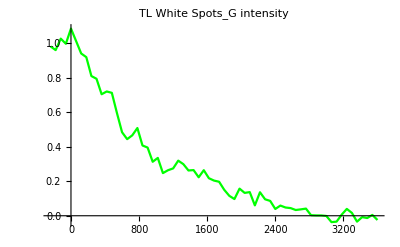

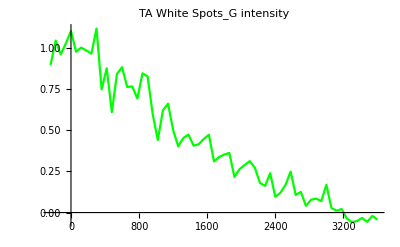

```mathematica
ListLinePlot[ntGIntsYTime,PlotStyle->{Green},PlotLabel->"NT White Spots_G intensity"]
ListLinePlot[tlGIntsYTime,PlotStyle->{Green},PlotLabel->"TL White Spots_G intensity"]
ListLinePlot[taGIntsYTime,PlotStyle->{Green},PlotLabel->"TA White Spots_G intensity"]
```

#### Define tag and protein lengths in AAs

```mathematica
l2 = (1010/3)//N   (*Length of smFLAG tag in AAs*)
l1 = (4645/3)//N   (*Length of KDM5B in AAs*)
```

336.667

1548.33

```mathematica
fraction = (l1/(l1+l2/2))   (*Once the fluorescence drops by this much, this is t0*)
```

0.901942

#### Select the data that falls within the linear range: l1/(l1+l2/2) --> linear part MANUAL INPUT: Set where you want the Linear Range to be...

```mathematica
(*Selecct the LINEAR range of hte graph above by looking at where it's linear and fittable and plugging the start and stop of this range into RangeA and RangeB *)
```

```mathematica
ListLinePlot[ntGIntsYTime/60,PlotStyle->{Green},PlotLabel->"NT WHITE Spots_G intensity _ normalized and IF subtracted"]
```

-Graphics-

```mathematica
ntrangeA = 14;
ntrangeB = 26;
ntRangedata =  ntGIntsYTime[[ntrangeA;; ntrangeB ]]
```

{{540,Indeterminate},{600,Indeterminate},{660,Indeterminate},{720,Indeterminate},{780,Indeterminate},{840,Indeterminate},{900,Indeterminate},{960,Indeterminate},{1020,Indeterminate},{1080,Indeterminate},{1140,Indeterminate},{1200,Indeterminate},{1260,Indeterminate}}

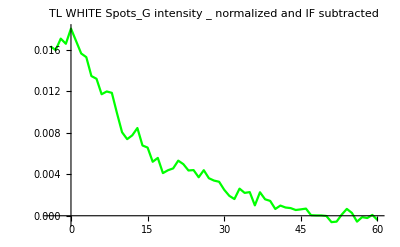

```mathematica
ListLinePlot[tlGIntsYTime/60,PlotStyle->{Green},PlotLabel->"TL WHITE Spots_G intensity _ normalized and IF subtracted"]
```

```mathematica
tlrangeA = 8;
tlrangeB = 20;
tlRangedata =  tlGIntsYTime[[tlrangeA;; tlrangeB ]]
```

{{180,0.918885},{240,0.809275},{300,0.793498},{360,0.703932},{420,0.71999},{480,0.712033},{540,0.595064},{600,0.483858},{660,0.4438},{720,0.465912},{780,0.508177},{840,0.407025},{900,0.395088}}

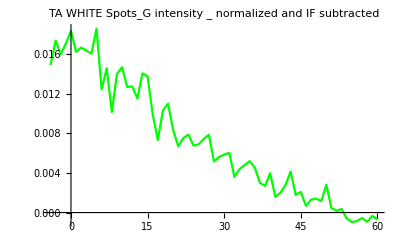

```mathematica
ListLinePlot[taGIntsYTime/60,PlotStyle->{Green},PlotLabel->"TA WHITE Spots_G intensity _ normalized and IF subtracted"]
```

```mathematica
tarangeA = 11;
tarangeB = 26;
taRangedata =  taGIntsYTime[[tarangeA ;; tarangeB ]]
```

{{360,0.74707},{420,0.875133},{480,0.609079},{540,0.840221},{600,0.881678},{660,0.762122},{720,0.764873},{780,0.691557},{840,0.844243},{900,0.825835},{960,0.596783},{1020,0.440081},{1080,0.619464},{1140,0.660477},{1200,0.500835},{1260,0.401702}}

#### Fit to the rate of elongation

### Fit to the rate of elongation

#### NT: Fit and calculate elongation rate

```mathematica
fdata = ntRangedata;
```

```mathematica
pfdata = ListLinePlot[ntGIntsYTime,PlotStyle->{Green},PlotLabel->"NT WHITE Spots_G intensity _ normalized and IF subtracted"]
```

-Graphics-

equation : y (ke, b) =  -ke/(L1 + L2/2)t +b

```mathematica
nlm=NonlinearModelFit[fdata ,-ke/(l1 + l2/2)t + b, {{ke},{b}},t]
```

FindFit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

NonlinearModelFit[{{540,Indeterminate},{600,Indeterminate},{660,Indeterminate},{720,Indeterminate},{780,Indeterminate},{840,Indeterminate},{900,Indeterminate},{960,Indeterminate},{1020,Indeterminate},{1080,Indeterminate},{1140,Indeterminate},{1200,Indeterminate},{1260,Indeterminate}},b-0.000582524 ke t,{{ke},{b}},t]

```mathematica
pntYnlm = Show[pfdata, Plot[nlm[t],{t,(ntrangeA)*60,(ntrangeB)*60}, PlotStyle->{Red,Dashed},PlotLegends->Normal[nlm]]]
```

FindFit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

General::stop: Further output of FindFit::fitm will be suppressed during this calculation.

General::ivar: 840.015 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

-Graphics-

```mathematica
nlm["ParameterConfidenceIntervalTable"]
```

FindFit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

NonlinearModelFit[{{540,Indeterminate},{600,Indeterminate},{660,Indeterminate},{720,Indeterminate},{780,Indeterminate},{840,Indeterminate},{900,Indeterminate},{960,Indeterminate},{1020,Indeterminate},{1080,Indeterminate},{1140,Indeterminate},{1200,Indeterminate},{1260,Indeterminate}},b-0.000582524 ke t,{{ke},{b}},t][ParameterConfidenceIntervalTable]

```mathematica
(*Confidence interval of the first element of the confidence, divide by 2 because it's + or - *)
confinterval = Differences@nlm["ParameterConfidenceIntervals"][[1]]/2
```

FindFit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

Differences::listrp: List or SparseArray or StructuredArray expected at position 1 in Differences[ParameterConfidenceIntervals].

Differences[ParameterConfidenceIntervals]/2

```mathematica
elongationrate =  PlusMinus[nlm["BestFitParameters"][[1,2]],confinterval[[1]]]
```

FindFit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

Part::partd: Part specification NonlinearModelFit[{{540,Indeterminate},{600,Indeterminate},{660,Indeterminate},{720,Indeterminate},{780,Indeterminate},{840,Indeterminate},{900,Indeterminate},{960,Indeterminate},{1020,Indeterminate},{1080,Indeterminate},{1140,Indeterminate},{1200,Indeterminate},{1260,Indeterminate}},b-0.000582524 ke t,{{ke},{b}},t][BestFitParameters]⟦1,2⟧ is longer than depth of object.

FindFit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

Part::partd: Part specification NonlinearModelFit[{{540,Indeterminate},{600,Indeterminate},{660,Indeterminate},{720,Indeterminate},{780,Indeterminate},{840,Indeterminate},{900,Indeterminate},{960,Indeterminate},{1020,Indeterminate},{1080,Indeterminate},{1140,Indeterminate},{1200,Indeterminate},{1260,Indeterminate}},b-0.000582524 ke t,{{ke},{b}},t][BestFitParameters]⟦1,2⟧ is longer than depth of object.

NonlinearModelFit[{{540,Indeterminate},{600,Indeterminate},{660,Indeterminate},{720,Indeterminate},{780,Indeterminate},{840,Indeterminate},{900,Indeterminate},{960,Indeterminate},{1020,Indeterminate},{1080,Indeterminate},{1140,Indeterminate},{1200,Indeterminate},{1260,Indeterminate}},b-0.000582524 ke t,{{ke},{b}},t][BestFitParameters]⟦1,2⟧±1/2

#### TL: Fit and calculate elongation rate

```mathematica
fdata = tlRangedata;
```

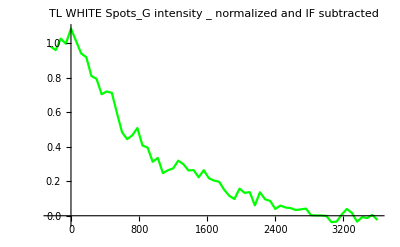

```mathematica
pfdata = ListLinePlot[tlGIntsYTime,PlotStyle->{Green},PlotLabel->"TL WHITE Spots_G intensity _ normalized and IF subtracted"]
```

equation : y (ke, b) =  -ke/(L1 + L2/2)t +b

```mathematica
nlm=NonlinearModelFit[fdata ,-ke/(l1 + l2/2)t + b, {{ke},{b}},t]
```

FittedModel[0.997257-0.000713363 t]

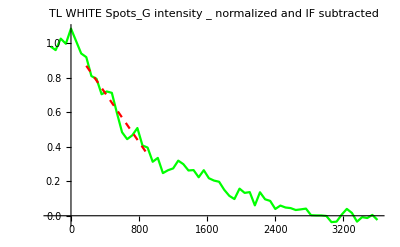

```mathematica
ptlWnlm =Show[pfdata, Plot[nlm[t],{t,(tlrangeA-5)*60,(tlrangeB-5)*60}, PlotStyle->{Red,Dashed},PlotLegends->Normal[nlm]],PlotRange->{{All,2800},{0,1.3}}]
```

```mathematica
nlm["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
ke | 1.22461 | 0.108741 | {0.985269,1.46394}
b | 0.997257 | 0.0370443 | {0.915724,1.07879}

```mathematica
(*Confidence interval of the first element of the confidence, divide by 2 because it's + or - *)
confinterval = Differences@nlm["ParameterConfidenceIntervals"][[1]]/2
```

{0.239338}

```mathematica
elongationrate =  PlusMinus[nlm["BestFitParameters"][[1,2]],confinterval[[1]]] (*AA per sec*)
```

1.22461±0.239338

#### TA: Fit and calculate elongation rate

```mathematica
fdata = taRangedata;
```

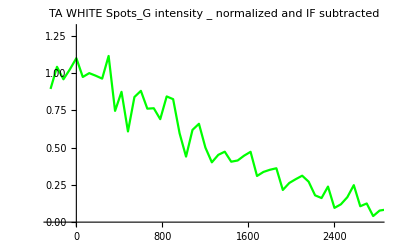

```mathematica
pfdata = ListLinePlot[taGIntsYTime,PlotStyle->{Green},PlotLabel->"TA WHITE Spots_G intensity _ normalized and IF subtracted",PlotRange->{{All,2800},{0,1.3}}]
```

equation : y (ke, b) =  -ke/(L1 + L2/2)t +b

```mathematica
nlm=NonlinearModelFit[fdata ,-ke/(l1 + l2/2)t + b, {{ke},{b}},t]
```

FittedModel[0.990112-0.000368876 t]

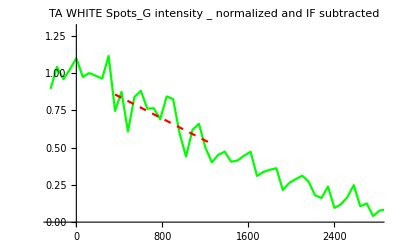

```mathematica
ptaWnlm =Show[pfdata, Plot[nlm[t],{t,(tarangeA-5)*60,(tarangeB-5)*60}, PlotStyle->{Red,Dashed},PlotLegends->Normal[nlm],PlotRange->{0,1.3}]]
```

```mathematica
nlm["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
ke | 0.633237 | 0.178733 | {0.249894,1.01658}
b | 0.990112 | 0.0891151 | {0.798979,1.18124}

```mathematica
(*Confidence interval of the first element of the confidence, divide by 2 because it's + or - *)
confinterval = Differences@nlm["ParameterConfidenceIntervals"][[1]]/2
```

{0.383343}

```mathematica
elongationrate =  PlusMinus[nlm["BestFitParameters"][[1,2]],confinterval[[1]]] (*AA per sec*)
```

0.633237±0.383343

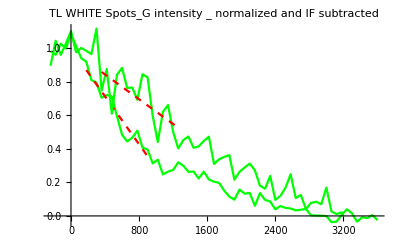

```mathematica
Show[ptlWnlm,ptaWnlm, PlotRange->{{All,2750},{0,1.3}}]
```

Comparing different days of data collection (only graphing, no nlm)

First, you need to import the data and gather by days ....

### Import:

```mathematica
ntYFiles = FileNames["/Users/ccialek/Desktop/HAR cells/*/Analysis/MAX_NT*YELLOW__myRGaussInts.m"];
tlYFiles = FileNames["/Users/ccialek/Desktop/HAR cells/*/Analysis/MAX_TL*YELLOW__myRGaussInts.m"];
taYFiles = FileNames["/Users/ccialek/Desktop/HAR cells/*/Analysis/MAX_TA*YELLOW__myRGaussInts.m"];
```

```mathematica
ntWFiles = FileNames["/Users/ccialek/Desktop/HAR cells/*/Analysis/MAX_NT*WHITE__myRGaussInts.m"];
tlWFiles = FileNames["/Users/ccialek/Desktop/HAR cells/*/Analysis/MAX_TL*WHITE__myRGaussInts.m"];
taWFiles = FileNames["/Users/ccialek/Desktop/HAR cells/*/Analysis/MAX_TA*WHITE__myRGaussInts.m"];
```

```mathematica
ntPFiles = FileNames["/Users/ccialek/Desktop/HAR cells/*/Analysis/MAX_NT*PURPLE__myRGaussInts.m"];
tlPFiles = FileNames["/Users/ccialek/Desktop/HAR cells/*/Analysis/MAX_TL*PURPLE__myRGaussInts.m"];
taPFiles = FileNames["/Users/ccialek/Desktop/HAR cells/*/Analysis/MAX_TA*PURPLE__myRGaussInts.m"];
```

```mathematica
Length@ntYFiles
Length@tlYFiles
Length@taYFiles
movieLength = Length@taYInts[[1,2]]
```

5

18

19

65

```mathematica
ntYInts0= Table[<<(ntYFiles[[i]]),{i,1,Length@ntYFiles,1}];
tlYInts0= Table[<<(tlYFiles[[i]]),{i,1,Length@tlYFiles,1}];
taYInts0= Table[<<(taYFiles[[i]]),{i,1,Length@taYFiles,1}];
ntWInts0= Table[<<(ntWFiles[[i]]),{i,1,Length@ntWFiles,1}];
tlWInts0= Table[<<(tlWFiles[[i]]),{i,1,Length@tlWFiles,1}];
taWInts0= Table[<<(taWFiles[[i]]),{i,1,Length@taWFiles,1}];
ntPInts0= Table[<<(ntPFiles[[i]]),{i,1,Length@ntPFiles,1}];
tlPInts0= Table[<<(tlPFiles[[i]]),{i,1,Length@tlPFiles,1}];
taPInts0= Table[<<(taPFiles[[i]]),{i,1,Length@taPFiles,1}];
```

This line filters out the crazy intensities...
It crops out headers but adds them back in so data structure is the same as before

```mathematica
ntYInts= Table[ Join[{ntYInts0[[1,1]]}, Table[Table[Select[ntYInts0[[cell,channel,frame]],#<1&],{frame,1,movieLength}],{channel,2,4}]] ,{cell,1,Length@ntYInts0}];
tlYInts= Table[ Join[{ntYInts0[[1,1]]}, Table[Table[Select[tlYInts0[[cell,channel,frame]],#<1&],{frame,1,movieLength}],{channel,2,4}]] ,{cell,1,Length@tlYInts0}];
taYInts= Table[ Join[{ntYInts0[[1,1]]}, Table[Table[Select[taYInts0[[cell,channel,frame]],#<1&],{frame,1,movieLength}],{channel,2,4}]] ,{cell,1,Length@taYInts0}];
ntWInts= Table[ Join[{ntYInts0[[1,1]]}, Table[Table[Select[ntWInts0[[cell,channel,frame]],#<1&],{frame,1,movieLength}],{channel,2,4}]] ,{cell,1,Length@ntWInts0}];
tlWInts= Table[ Join[{ntYInts0[[1,1]]}, Table[Table[Select[tlWInts0[[cell,channel,frame]],#<1&],{frame,1,movieLength}],{channel,2,4}]] ,{cell,1,Length@tlWInts0}];
taWInts= Table[ Join[{ntYInts0[[1,1]]}, Table[Table[Select[taWInts0[[cell,channel,frame]],#<1&],{frame,1,movieLength}],{channel,2,4}]] ,{cell,1,Length@taWInts0}];
ntPInts= Table[ Join[{ntYInts0[[1,1]]}, Table[Table[Select[ntPInts0[[cell,channel,frame]],#<1&],{frame,1,movieLength}],{channel,2,4}]],{cell,1,Length@ntPInts0}];
tlPInts= Table[ Join[{ntYInts0[[1,1]]}, Table[Table[Select[tlPInts0[[cell,channel,frame]],#<1&],{frame,1,movieLength}],{channel,2,4}]] ,{cell,1,Length@tlPInts0}];
taPInts= Table[ Join[{ntYInts0[[1,1]]}, Table[Table[Select[taPInts0[[cell,channel,frame]],#<1&],{frame,1,movieLength}],{channel,2,4}]] ,{cell,1,Length@taPInts0}];
```

#### Check imports...

```mathematica
ntYInts[[1,1]]
ntYInts0[[1,1]]
```

{{myRGaussInts_>0},{myGGaussInts_>0},{myBGaussInts_>0}}

{{myRGaussInts_>0},{myGGaussInts_>0},{myBGaussInts_>0}}

```mathematica
Dimensions@ntYInts
Dimensions@ntYInts0
Dimensions/@ntYInts0[[1]]
```

{5,4}

{5,4}

{{3,1},{65},{65},{65}}

{{3,1},{65},{65},{65}}

{65}

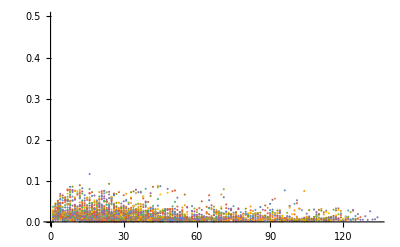

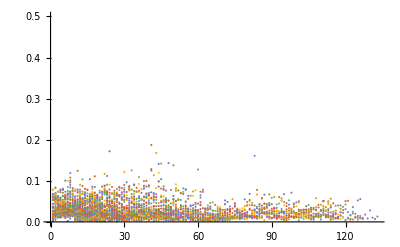

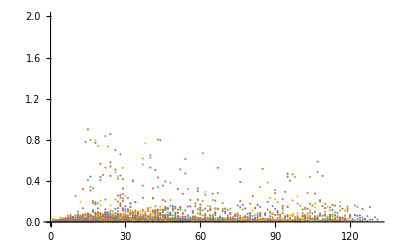

```mathematica
Dimensions/@tlWInts[[1]]
Dimensions@ Table[Flatten[tlWInts[[All,3,frame]],1],{frame,1,65,1}]
 Table[Flatten[tlWInts[[All,2,frame]],1],{frame,1,65,1}]//ListPlot[#,PlotRange->{0,.5}]&
 Table[Flatten[tlWInts[[All,3,frame]],1],{frame,1,65,1}]//ListPlot[#,PlotRange->{0,.5}]&
 Table[Flatten[tlWInts[[All,4,frame]],1],{frame,1,65,1}]//ListPlot[#,PlotRange->{0,2}]&
```

```mathematica
Select[{1,2,4,7,6,2},#>2&]
```

{4,7,6}

```mathematica
Row[{ Table[Flatten[taWInts[[All,3,frame]],1],{frame,1,65,1}]//ListPlot[#,PlotRange->All, ImageSize->400]&,
Table[Select[Flatten[taWInts[[All,3,frame]],1],#<2&],{frame,1,65,1}]//ListPlot[#,PlotRange->All,ImageSize->400]&  }]
(*This is showing that without filtering I'm getting some crazy intensities.... *)
```

-Graphics--Graphics-

#### Looking at EACH cell....

These are the TOTALS of ALL CELLS

```mathematica
ntYIntsTotRGB= Table[Table[Total@(Total/@ntYInts[[All,j,i]]),{i,1,Length@ntYInts[[1,2]],1}],{j,2,Length@ntYInts[[2]],1}];
tlYIntsTotRGB= Table[Table[Total@(Total/@tlYInts[[All,j,i]]),{i,1,Length@tlYInts[[1,2]],1}],{j,2,Length@tlYInts[[2]],1}];
taYIntsTotRGB= Table[Table[Total@(Total/@taYInts[[All,j,i]]),{i,1,Length@taYInts[[1,2]],1}],{j,2,Length@taYInts[[2]],1}];
```

These are the TOTALS of EACH CELL

```mathematica
ntYIntsRGB=  ntYInts//Table[Table[(Total/@#[[cell,channel]]),{channel,2,4}],{cell,1,Length@#,1}]&;
tlYIntsRGB=  tlYInts//Table[Table[(Total/@#[[cell,channel]]),{channel,2,4}],{cell,1,Length@#,1}]&;
taYIntsRGB=  taYInts//Table[Table[(Total/@#[[cell,channel]]),{channel,2,4}],{cell,1,Length@#,1}]&;
```

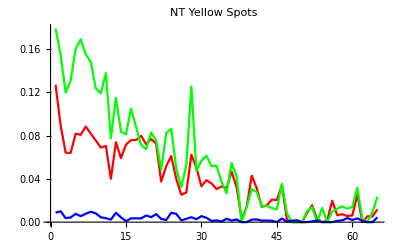
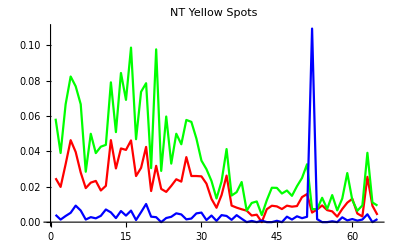
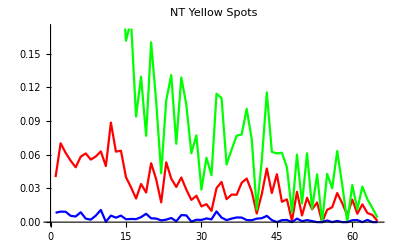
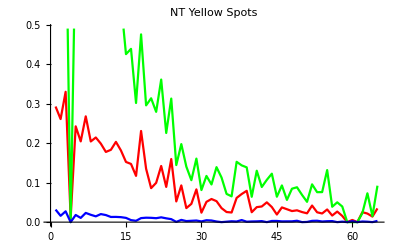
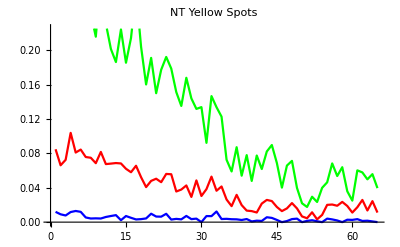

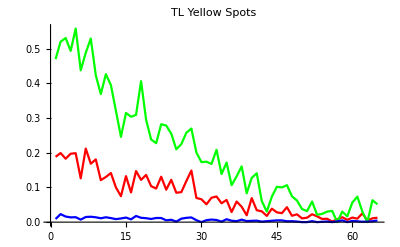
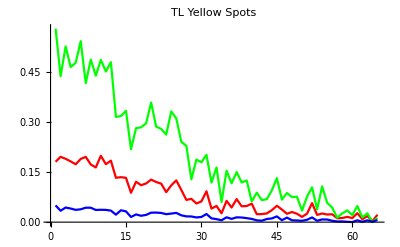
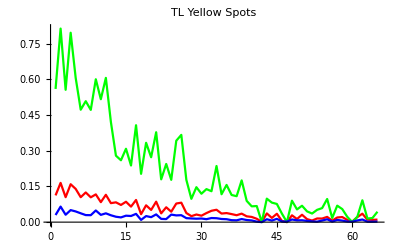

```mathematica
ListLinePlot[#,PlotStyle->{Red,Green,Blue},PlotLabel->"NT Yellow Spots"]&/@ntYIntsRGB
ListLinePlot[#,PlotStyle->{Red,Green,Blue},PlotRange->All,PlotLabel->"TL Yellow Spots"]&/@tlYIntsRGB
ListLinePlot[#,PlotStyle->{Red,Green,Blue},PlotLabel->"TA Yellow Spots"] &/@taYIntsRGB
```

```mathematica
ntWIntsTotRGB= Table[Table[Total@(Total/@ntWInts[[All,j,i]]),{i,1,Length@ntWInts[[1,2]],1}],{j,2,Length@ntWInts[[2]],1}];
tlWIntsTotRGB= Table[Table[Total@(Total/@tlWInts[[All,j,i]]),{i,1,Length@tlWInts[[1,2]],1}],{j,2,Length@tlWInts[[2]],1}];
taWIntsTotRGB= Table[Table[Total@(Total/@taWInts[[All,j,i]]),{i,1,Length@taWInts[[1,2]],1}],{j,2,Length@taWInts[[2]],1}];
```

```mathematica
ntWIntsRGB=  ntWInts//Table[Table[(Total/@#[[cell,channel]]),{channel,2,4}],{cell,1,Length@#,1}]& //  Table[#[[cell]]/#[[cell,1]],{cell,1,Length@ntWInts}]&  ;
tlWIntsRGB=  tlWInts//Table[Table[(Total/@#[[cell,channel]]),{channel,2,4}],{cell,1,Length@#,1}] & ;
taWIntsRGB=  taWInts//Table[Table[(Total/@#[[cell,channel]]),{channel,2,4}],{cell,1,Length@#,1}]&;
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in {{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«15»},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«15»},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«15»}} {ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,«15»,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,«15»} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

```mathematica
ListLinePlot[ntWIntsTotRGB,PlotStyle->{Red,Green,Blue},PlotLabel->"NT White Spots"]
ListLinePlot[tlWIntsTotRGB,PlotStyle->{Red,Green,Blue},PlotLabel->"TL White Spots",PlotRange->All]
ListLinePlot[taWIntsTotRGB,PlotStyle->{Red,Green,Blue},PlotLabel->"TA White Spots"]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
ntPIntsTotRGB= Table[Table[Total@(Total/@ntPInts[[All,j,i]]),{i,1,Length@ntPInts[[1,2]],1}],{j,2,Length@ntPInts[[2]],1}];
tlPIntsTotRGB= Table[Table[Total@(Total/@tlPInts[[All,j,i]]),{i,1,Length@tlPInts[[1,2]],1}],{j,2,Length@tlPInts[[2]],1}];
taPIntsTotRGB= Table[Table[Total@(Total/@taPInts[[All,j,i]]),{i,1,Length@taPInts[[1,2]],1}],{j,2,Length@taPInts[[2]],1}];
```

```mathematica
ntPIntsRGB=  ntPInts//Table[Table[(Total/@#[[cell,channel]]),{channel,2,4}],{cell,1,Length@#,1}]&;
tlPIntsRGB=  tlPInts//Table[Table[(Total/@#[[cell,channel]]),{channel,2,4}],{cell,1,Length@#,1}]&;
taPIntsRGB=  taPInts//Table[Table[(Total/@#[[cell,channel]]),{channel,2,4}],{cell,1,Length@#,1}]&;
```

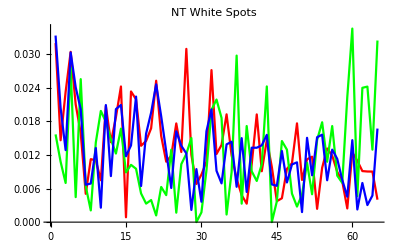

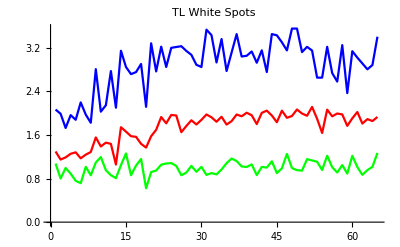

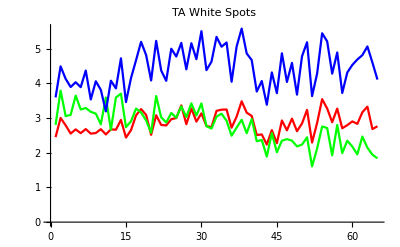

```mathematica
ListLinePlot[ntPIntsTotRGB,PlotStyle->{Red,Green,Blue},PlotLabel->"NT White Spots"]
ListLinePlot[tlPIntsTotRGB,PlotStyle->{Red,Green,Blue},PlotLabel->"TL White Spots",PlotRange->All]
ListLinePlot[taPIntsTotRGB,PlotStyle->{Red,Green,Blue},PlotLabel->"TA White Spots"]
```

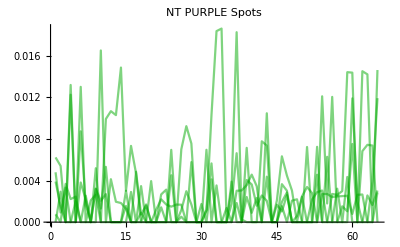

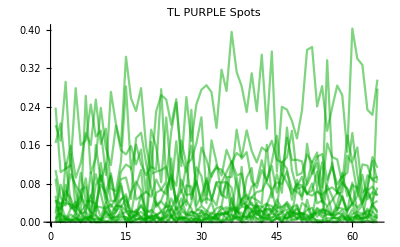

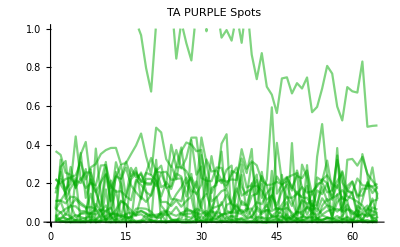

```mathematica
ListLinePlot[#,PlotStyle-> {{Darker[Green],Opacity[0.5]}},PlotLabel->"NT PURPLE Spots",PlotRange->All]&@ntPIntsRGB[[All,2]]
ListLinePlot[#,PlotStyle-> {{Darker[Green],Opacity[0.5]}},PlotRange->All,PlotLabel->"TL PURPLE Spots"]&@tlPIntsRGB[[All,2]]
ListLinePlot[#,PlotStyle-> {{Darker[Green],Opacity[0.5]}},PlotLabel->"TA PURPLE Spots" ,PlotRange->{0,1}] & @taPIntsRGB[[All,2]]
```

Comparing different days of data collection (only graphing, no nlm)

First, you need to import the data and gather by days ....

### Import:

```mathematica
ntYFiles = FileNames["/Users/ccialek/Desktop/HAR cells/*/Analysis/MAX_NT*YELLOW__myRGaussInts.m"];
tlYFiles = FileNames["/Users/ccialek/Desktop/HAR cells/*/Analysis/MAX_TL*YELLOW__myRGaussInts.m"];
taYFiles = FileNames["/Users/ccialek/Desktop/HAR cells/*/Analysis/MAX_TA*YELLOW__myRGaussInts.m"];
```

```mathematica
ntWFiles = FileNames["/Users/ccialek/Desktop/HAR cells/*/Analysis/MAX_NT*WHITE__myRGaussInts.m"];
tlWFiles = FileNames["/Users/ccialek/Desktop/HAR cells/*/Analysis/MAX_TL*WHITE__myRGaussInts.m"];
taWFiles = FileNames["/Users/ccialek/Desktop/HAR cells/*/Analysis/MAX_TA*WHITE__myRGaussInts.m"];
```

```mathematica
ntPFiles = FileNames["/Users/ccialek/Desktop/HAR cells/*/Analysis/MAX_NT*PURPLE__myRGaussInts.m"];
tlPFiles = FileNames["/Users/ccialek/Desktop/HAR cells/*/Analysis/MAX_TL*PURPLE__myRGaussInts.m"];
taPFiles = FileNames["/Users/ccialek/Desktop/HAR cells/*/Analysis/MAX_TA*PURPLE__myRGaussInts.m"];
```

```mathematica
Length@ntYFiles
Length@tlYFiles
Length@taYFiles
movieLength = Length@taYInts[[1,2]]
```

5

18

19

65

```mathematica
ntYInts0= Table[<<(ntYFiles[[i]]),{i,1,Length@ntYFiles,1}];
tlYInts0= Table[<<(tlYFiles[[i]]),{i,1,Length@tlYFiles,1}];
taYInts0= Table[<<(taYFiles[[i]]),{i,1,Length@taYFiles,1}];
ntWInts0= Table[<<(ntWFiles[[i]]),{i,1,Length@ntWFiles,1}];
tlWInts0= Table[<<(tlWFiles[[i]]),{i,1,Length@tlWFiles,1}];
taWInts0= Table[<<(taWFiles[[i]]),{i,1,Length@taWFiles,1}];
ntPInts0= Table[<<(ntPFiles[[i]]),{i,1,Length@ntPFiles,1}];
tlPInts0= Table[<<(tlPFiles[[i]]),{i,1,Length@tlPFiles,1}];
taPInts0= Table[<<(taPFiles[[i]]),{i,1,Length@taPFiles,1}];
```

This line filters out the crazy intensities...
It crops out headers but adds them back in so data structure is the same as before

```mathematica
ntYInts= Table[ Join[{ntYInts0[[1,1]]}, Table[Table[Select[ntYInts0[[cell,channel,frame]],#<1&],{frame,1,movieLength}],{channel,2,4}]] ,{cell,1,Length@ntYInts0}];
tlYInts= Table[ Join[{ntYInts0[[1,1]]}, Table[Table[Select[tlYInts0[[cell,channel,frame]],#<1&],{frame,1,movieLength}],{channel,2,4}]] ,{cell,1,Length@tlYInts0}];
taYInts= Table[ Join[{ntYInts0[[1,1]]}, Table[Table[Select[taYInts0[[cell,channel,frame]],#<1&],{frame,1,movieLength}],{channel,2,4}]] ,{cell,1,Length@taYInts0}];
ntWInts= Table[ Join[{ntYInts0[[1,1]]}, Table[Table[Select[ntWInts0[[cell,channel,frame]],#<1&],{frame,1,movieLength}],{channel,2,4}]] ,{cell,1,Length@ntWInts0}];
tlWInts= Table[ Join[{ntYInts0[[1,1]]}, Table[Table[Select[tlWInts0[[cell,channel,frame]],#<1&],{frame,1,movieLength}],{channel,2,4}]] ,{cell,1,Length@tlWInts0}];
taWInts= Table[ Join[{ntYInts0[[1,1]]}, Table[Table[Select[taWInts0[[cell,channel,frame]],#<1&],{frame,1,movieLength}],{channel,2,4}]] ,{cell,1,Length@taWInts0}];
ntPInts= Table[ Join[{ntYInts0[[1,1]]}, Table[Table[Select[ntPInts0[[cell,channel,frame]],#<1&],{frame,1,movieLength}],{channel,2,4}]],{cell,1,Length@ntPInts0}];
tlPInts= Table[ Join[{ntYInts0[[1,1]]}, Table[Table[Select[tlPInts0[[cell,channel,frame]],#<1&],{frame,1,movieLength}],{channel,2,4}]] ,{cell,1,Length@tlPInts0}];
taPInts= Table[ Join[{ntYInts0[[1,1]]}, Table[Table[Select[taPInts0[[cell,channel,frame]],#<1&],{frame,1,movieLength}],{channel,2,4}]] ,{cell,1,Length@taPInts0}];
```

#### Check imports...

```mathematica
ntYInts[[1,1]]
ntYInts0[[1,1]]
```

{{myRGaussInts_>0},{myGGaussInts_>0},{myBGaussInts_>0}}

{{myRGaussInts_>0},{myGGaussInts_>0},{myBGaussInts_>0}}

```mathematica
Dimensions@ntYInts
Dimensions@ntYInts0
Dimensions/@ntYInts0[[1]]
```

{5,4}

{5,4}

{{3,1},{65},{65},{65}}

```mathematica
Dimensions/@tlWInts[[1]]
Dimensions@ Table[Flatten[tlWInts[[All,3,frame]],1],{frame,1,65,1}]
 Table[Flatten[tlWInts[[All,2,frame]],1],{frame,1,65,1}]//ListPlot[#,PlotRange->{0,.5}]&
 Table[Flatten[tlWInts[[All,3,frame]],1],{frame,1,65,1}]//ListPlot[#,PlotRange->{0,.5}]&
 Table[Flatten[tlWInts[[All,4,frame]],1],{frame,1,65,1}]//ListPlot[#,PlotRange->{0,2}]&
```

{{3,1},{65},{65},{65}}

{65}

-Graphics-

-Graphics-

-Graphics-

```mathematica
Select[{1,2,4,7,6,2},#>2&]
```

{4,7,6}

```mathematica
Row[{ Table[Flatten[taWInts[[All,3,frame]],1],{frame,1,65,1}]//ListPlot[#,PlotRange->All, ImageSize->400]&,
Table[Select[Flatten[taWInts[[All,3,frame]],1],#<2&],{frame,1,65,1}]//ListPlot[#,PlotRange->All,ImageSize->400]&  }]
(*This is showing that without filtering I'm getting some crazy intensities.... *)
```

-Graphics--Graphics-

#### Looking at EACH cell....

These are the TOTALS of ALL CELLS

```mathematica
ntYIntsTotRGB= Table[Table[Total@(Total/@ntYInts[[All,j,i]]),{i,1,Length@ntYInts[[1,2]],1}],{j,2,Length@ntYInts[[2]],1}];
tlYIntsTotRGB= Table[Table[Total@(Total/@tlYInts[[All,j,i]]),{i,1,Length@tlYInts[[1,2]],1}],{j,2,Length@tlYInts[[2]],1}];
taYIntsTotRGB= Table[Table[Total@(Total/@taYInts[[All,j,i]]),{i,1,Length@taYInts[[1,2]],1}],{j,2,Length@taYInts[[2]],1}];
```

These are the TOTALS of EACH CELL

```mathematica
ntYIntsRGB=  ntYInts//Table[Table[(Total/@#[[cell,channel]]),{channel,2,4}],{cell,1,Length@#,1}]&;
tlYIntsRGB=  tlYInts//Table[Table[(Total/@#[[cell,channel]]),{channel,2,4}],{cell,1,Length@#,1}]&;
taYIntsRGB=  taYInts//Table[Table[(Total/@#[[cell,channel]]),{channel,2,4}],{cell,1,Length@#,1}]&;
```

```mathematica
ListLinePlot[#,PlotStyle->{Red,Green,Blue},PlotLabel->"NT Yellow Spots"]&/@ntYIntsRGB
ListLinePlot[#,PlotStyle->{Red,Green,Blue},PlotRange->All,PlotLabel->"TL Yellow Spots"]&/@tlYIntsRGB
ListLinePlot[#,PlotStyle->{Red,Green,Blue},PlotLabel->"TA Yellow Spots"] &/@taYIntsRGB
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListLinePlot[#,PlotStyle-> {{Darker[Green],Opacity[0.4]}},PlotLabel->"NT Yellow Spots",PlotRange->All]&@ntYIntsRGB[[All,2]]
ListLinePlot[#,PlotStyle-> {{Darker[Green],Opacity[0.4]}},PlotRange->All,PlotLabel->"TL Yellow Spots"]&@tlYIntsRGB[[All,2]]
ListLinePlot[#,PlotStyle-> {{Darker[Green],Opacity[0.4]}},PlotLabel->"TA Yellow Spots" ,PlotRange->All] & @taYIntsRGB[[All,2]]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
ntWIntsTotRGB= Table[Table[Total@(Total/@ntWInts[[All,j,i]]),{i,1,Length@ntWInts[[1,2]],1}],{j,2,Length@ntWInts[[2]],1}];
tlWIntsTotRGB= Table[Table[Total@(Total/@tlWInts[[All,j,i]]),{i,1,Length@tlWInts[[1,2]],1}],{j,2,Length@tlWInts[[2]],1}];
taWIntsTotRGB= Table[Table[Total@(Total/@taWInts[[All,j,i]]),{i,1,Length@taWInts[[1,2]],1}],{j,2,Length@taWInts[[2]],1}];
```

```mathematica
(*ntWIntsRGB=  ntWInts//Table[Table[(Total/@#[[cell,channel]]),{channel,2,4}],{cell,1,Length@#,1}]& //  Table[#[[cell]]/#[[cell,1]],{cell,1,Length@ntWInts}]&  ;*)
tlWIntsRGB=  tlWInts//Table[Table[(Total/@#[[cell,channel]]),{channel,2,4}],{cell,1,Length@#,1}] & ;
taWIntsRGB=  taWInts//Table[Table[(Total/@#[[cell,channel]]),{channel,2,4}],{cell,1,Length@#,1}]&;
```

```mathematica
ListLinePlot[ntWIntsTotRGB,PlotStyle->{Red,Green,Blue},PlotLabel->"NT White Spots"]
ListLinePlot[tlWIntsTotRGB,PlotStyle->{Red,Green,Blue},PlotLabel->"TL White Spots",PlotRange->All]
ListLinePlot[taWIntsTotRGB,PlotStyle->{Red,Green,Blue},PlotLabel->"TA White Spots"]
```

-Graphics-

-Graphics-

-Graphics-

#### Totals of each day:

```mathematica
ntYIntsByDayRGB= ntYIntsRGB//Total@#[[All]]&;
tlYIntsByDayRGB=  tlYIntsRGB//{Total@#[[1;;5]], Total@#[[6;;8]],Total@#[[9;;12]],Total@#[[13;;18]]}&;
taYIntsByDayRGB=  taYIntsRGB//{Total@#[[1;;8]],Total@#[[9;;16]],Total@#[[17;;19]]}&;
```

```mathematica
ListLinePlot[#,PlotStyle->{Red,Green,Blue},PlotLabel->"NT YELLOW Spots",PlotRange->All]&@ntYIntsByDayRGB
ListLinePlot[#,PlotStyle->{Red,Green,Blue},PlotLabel->"TL YELLOW Spots",PlotRange->All] &/@tlYIntsByDayRGB
ListLinePlot[#,PlotStyle->{Red,Green,Blue},PlotLabel->"TA YELLOW Spots"]&/@taYIntsByDayRGB
```

-Graphics-

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-}

{No NT White cells}

```mathematica
{"No NT White cells"}
ListLinePlot[#,PlotStyle->{Red,Green,Blue},PlotLabel->"TL WHITE Spots",PlotRange->All] &/@tlWIntsByDayRGB
ListLinePlot[#,PlotStyle->{Red,Green,Blue},PlotLabel->"TA WHITE Spots"]&/@taWIntsByDayRGB
```

{No NT White cells}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-}

#### White: each cell

Not normalized, value on Y axis represents total intensity of all green spots in a cell

```mathematica
ListLinePlot[#,PlotStyle-> {{Darker[Green],Opacity[0.5]}},PlotLabel->"NT WHITE Spots",PlotRange->All]&@ntWIntsRGB[[All,2]]
ListLinePlot[#,PlotStyle-> {{Darker[Green],Opacity[0.5]}},PlotRange->All,PlotLabel->"TL WHITE Spots"]&@tlWIntsRGB[[All,2]]
ListLinePlot[#,PlotStyle-> {{Darker[Green],Opacity[0.5]}},PlotLabel->"TA WHITE Spots" ,PlotRange->{0,1}] & @taWIntsRGB[[All,2]]
```

-Graphics-

-Graphics-

-Graphics-

#### Looking at normalized totals by day

```mathematica
{"No NT White cells"}
tlWIntsByDayRGB=  tlWIntsRGB//{Total@#[[1;;5]], Total@#[[6;;8]],Total@#[[9;;12]],Total@#[[13;;18]]}&;
taWIntsByDayRGB=  taWIntsRGB//{Total@#[[1;;8]],Total@#[[9;;16]],Total@#[[17;;19]]}&;
```

{No NT White cells}

```mathematica
ntYIntsByDayRGB[[2]]//  ListLinePlot[#,PlotStyle-> {{Darker[Green],Opacity[0.5]}},PlotLabel->"NT YELLOW normalized total per day"]&
tlYIntsByDayRGB[[All,2]]//  Table[#[[cell]]/#[[cell,1]],{cell,1,Length@#[[All,2]]}]&//ListLinePlot[#,PlotStyle-> {{Darker[Green],Opacity[0.5]}},PlotLabel->"TL YELLOW normalized total per day",PlotRange->{0,2}]&
taYIntsByDayRGB[[All,2]]//  Table[#[[cell]]/#[[cell,1]],{cell,1,Length@#[[All,2]]}]&//ListLinePlot[#,PlotStyle-> {{Darker[Green],Opacity[0.5]}},PlotLabel->"TA YELLOW normalized total per day"]&
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
{"No NT White cells"}
tlWIntsByDayRGB[[All,2]]//  Table[#[[cell]]/#[[cell,1]],{cell,1,Length@#[[All,2]]}]&//ListLinePlot[#,PlotStyle-> {{Darker[Green],Opacity[0.5]}},PlotLabel->"TL WHITE normalized total per day"]&
taWIntsByDayRGB[[All,2]]//  Table[#[[cell]]/#[[cell,1]],{cell,1,Length@#[[All,2]]}]&//ListLinePlot[#,PlotStyle-> {{Darker[Green],Opacity[0.5]}},PlotLabel->"TA WHITE normalized total per day"]&
```

{No NT White cells}

-Graphics-

-Graphics-

#### Purple spots

```mathematica
ntPIntsTotRGB= Table[Table[Total@(Total/@ntPInts[[All,j,i]]),{i,1,Length@ntPInts[[1,2]],1}],{j,2,Length@ntPInts[[2]],1}];
tlPIntsTotRGB= Table[Table[Total@(Total/@tlPInts[[All,j,i]]),{i,1,Length@tlPInts[[1,2]],1}],{j,2,Length@tlPInts[[2]],1}];
taPIntsTotRGB= Table[Table[Total@(Total/@taPInts[[All,j,i]]),{i,1,Length@taPInts[[1,2]],1}],{j,2,Length@taPInts[[2]],1}];
```

```mathematica
ntPIntsRGB=  ntPInts//Table[Table[(Total/@#[[cell,channel]]),{channel,2,4}],{cell,1,Length@#,1}]&;
tlPIntsRGB=  tlPInts//Table[Table[(Total/@#[[cell,channel]]),{channel,2,4}],{cell,1,Length@#,1}]&;
taPIntsRGB=  taPInts//Table[Table[(Total/@#[[cell,channel]]),{channel,2,4}],{cell,1,Length@#,1}]&;
```

```mathematica
ListLinePlot[ntPIntsTotRGB,PlotStyle->{Red,Green,Blue},PlotLabel->"NT PURP Spots"]
ListLinePlot[tlPIntsTotRGB,PlotStyle->{Red,Green,Blue},PlotLabel->"TL PURP Spots",PlotRange->All]
ListLinePlot[taPIntsTotRGB,PlotStyle->{Red,Green,Blue},PlotLabel->"TA PURP Spots"]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
ListLinePlot[#,PlotStyle-> {{Darker[Green],Opacity[0.5]}},PlotLabel->"NT WHITE Spots",PlotRange->All]&@ntPIntsRGB[[All,2]]
ListLinePlot[#,PlotStyle-> {{Darker[Green],Opacity[0.5]}},PlotRange->All,PlotLabel->"TL WHITE Spots"]&@tlPIntsRGB[[All,2]]
ListLinePlot[#,PlotStyle-> {{Darker[Green],Opacity[0.5]}},PlotLabel->"TA WHITE Spots" ,PlotRange->{0,1}] & @taPIntsRGB[[All,2]]
```

-Graphics-

-Graphics-

-Graphics-

## Old code (Not used anymore) Filter (not used) Linear fit Linear fit elongation rate

## Filter out super bright spots.... DEVEL ONLY NOT USED

```mathematica
Mean/@taPIntsTotRGB
StandardDeviation/@taPIntsTotRGB
```

{2.74263,35285.9,4.22213}

{0.449464,246767.,0.877374}

```mathematica
Flatten@taPInts[[2,2;;All]]//ListPlot[#,PlotRange->All]&
```

```mathematica
Flatten@taPInts[[2,2;;All]]//ListPlot[#,PlotRange->All]&
```

-Graphics-

```mathematica
taPIntsTotRGB[[1]]
```

{2.47584,3.07414,2.86488,2.65799,2.62659,2.60375,2.60432,2.49616,2.39273,2.4301,2.62514,2.46654,1.54375,2.98487,2.5901,2.67558,2.83154,3.19738,3.04889,1.79608,3.07772,2.68259,2.81214,2.18564,3.14384,3.2118,2.66394,3.39831,2.77247,3.27428,2.87858,2.95246,3.14649,3.08243,2.82629,2.50264,2.21784,2.42245,2.89442,3.14418,1.75569,2.22796,2.17026,2.7947,2.30414,3.11704,2.57342,3.1438,2.44234,2.76412,2.49059,1.54537,3.02607,3.6355,3.44101,2.98863,3.41848,2.83269,2.76175,3.02623,2.83506,3.31131,3.42907,1.98778,2.9709}

```mathematica
temp = Cases[Flatten@taPInts[[2]], x_/;x<.04];
ListPlot[temp,PlotRange->All]
```

-Graphics-

## back to the code

```mathematica
ntPIntsTotRGB= Table[Table[Total@(Total/@ntPInts[[All,j,i]]),{i,1,Length@ntPInts[[1,2]],1}],{j,2,Length@ntPInts[[2]],1}];
tlPIntsTotRGB= Table[Table[Total@(Total/@tlPInts[[All,j,i]]),{i,1,Length@tlPInts[[1,2]],1}],{j,2,Length@tlPInts[[2]],1}];
taPIntsTotRGB= Table[Table[Total@(Total/@taPInts[[All,j,i]]),{i,1,Length@taPInts[[1,2]],1}],{j,2,Length@taPInts[[2]],1}];
```

```mathematica
ListLinePlot[ntPIntsTotRGB,PlotStyle->{Red,Green,Blue},PlotLabel->"NT Purp Spots"]
ListLinePlot[tlPIntsTotRGB,PlotStyle->{Red,Green,Blue},PlotLabel->"TL Purp Spots"]
ListLinePlot[taPIntsTotRGB,PlotStyle->{Red,Green,Blue},PlotLabel->"TA Purp Spots"]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
Range[Length@taYIntsTotRGB]
```

{1,2,3}

## Fits:

### FIRST : take the immobile fraction adn average those spots. THIS is the Immobile fration. Subtract this # by all timepints NEW Length of the gene is JUST L1. ONLY USE the length of KDM5B, NOT plus smFLAG tag THEN, normalize my graphs to start at 1. THEN, Calculate (L1/(L1+L2/2))

### TA fits for green channel intensity over time

#### TA yellow spot fits

```mathematica
fdata = {{1, .7},{2, .45},{3, .2},{4,.01}}
```

{{1,0.7},{2,0.45},{3,0.2},{4,0.01}}

```mathematica
ListPlot[fdata]
```

-Graphics-

```mathematica
l1 = 10;
l2 = 100;
```

```mathematica
(*l1*)
```

equation : y (ke, b) =  -ke/(L1 + L2/2)t +b

```mathematica
nlm=NonlinearModelFit[fdata ,-ke/(l1 + l2/2)t + b, {{ke,3},{b,2}},t]
```

FittedModel[0.92-0.232 t]

```mathematica
nlm["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
ke | 13.92 | 0.623538 | {11.2371,16.6029}
b | 0.92 | 0.0284605 | {0.797544,1.04246}

```mathematica
(*Confidence interval of the first element of the confidence, divide by 2 because it's + or - *)
Differences@nlm["ParameterConfidenceIntervals"][[1]]/2
```

{2.68287}

```mathematica
(*10 means start the fit at timept 10*)
fits = Table[Fit[taYIntsTotRGB[[2]][[5;;i]],{1,x},x],{i, 15,65,5}]
```

{5.79262-0.233167 x,5.57188-0.185193 x,5.37823-0.157267 x,5.20138-0.135775 x,5.03051-0.118205 x,4.91283-0.107987 x,4.77333-0.0975009 x,4.62915-0.0879299 x,4.48951-0.0795129 x,4.29081-0.068758 x,4.19658-0.0640402 x}

```mathematica
Plot[{fits},{x,0,65}, PlotStyle->Table[GrayLevel[i],{i,.1,Length@fits,.1}],PlotLegends->"Expressions"]
```

-Graphics-

```mathematica
FindRoot[fits[[6]],{x,0}]
```

{x→45.4945}

```mathematica
xints = Table[FindRoot[fits[[i]],{x,0}],{i,1,Length@fits,1}]//Cases[#,{x->x_}->x]&
```

{24.8432,30.0869,34.198,38.3087,42.5577,45.4945,48.9568,52.6459,56.4626,62.4045,65.5303}

This graph shows the fits of regression in TA Yellow spots... I’m using 10 as the starting point so I don’t fit to the first 10 points (first 5 are pre-HT, next 5 are too early to see ribosome drop off bc they’re still translating the tag)

#### TA White spot fits

```mathematica
(*10 means start the fit at timept 10*)
fits = Table[Fit[taWIntsTotRGB[[2]][[5;;i]],{1,x},x],{i, 15,65,5}]
```

{3.88556-0.125161 x,3.68528-0.086903 x,3.70961-0.0913791 x,3.6523-0.0848357 x,3.58215-0.0776633 x,3.50992-0.0715215 x,3.45484-0.0673555 x,3.38634-0.0628213 x,2.20961+0.00808293 x,2.55195-0.010663 x,2.78108-0.0221601 x}

```mathematica
Plot[{fits},{x,0,65}, PlotStyle->Table[GrayLevel[i],{i,.1,Length@fits,.1}],PlotLegends->"Expressions"]
```

-Graphics-

```mathematica
FindRoot[fits[[6]],{x,0}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{x→49.0751}

```mathematica
xints = Table[FindRoot[fits[[i]],{x,0}],{i,1,Length@fits,1}]//Cases[#,{x->x_}->x]&
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{31.0445,42.4068,40.5958,43.0515,46.1242,49.0751,51.2927,53.9044,-273.367,239.328,125.499}

This graph shows the fits of regression in TA Yellow spots... I’m using 10 as the starting point so I don’t fit to the first 10 points (first 5 are pre-HT, next 5 are too early to see ribosome drop off bc they’re still translating the tag)

#### TA purple spot fits

```mathematica
(*10 means start the fit at timept 10*)
fits = Table[Fit[taPIntsTotRGB[[2]][[5;;i]],{1,x},x],{i, 15,65,5}]
```

{50.1529-3.02216 x,51.493-3.37974 x,45.9873-2.5512 x,40.4501-1.88278 x,35.9514-1.43025 x,-6.26353+2.10789 x,-39.4782+4.62208 x,-14.605+2.95637 x,7.57234+1.62007 x,22.388+0.80908 x,-9.14977+2.4851 x}

```mathematica
Plot[{fits},{x,0,65}, PlotStyle->Table[GrayLevel[i],{i,.1,Length@fits,.1}],PlotLegends->"Expressions"]
```

-Graphics-

```mathematica
xints = Table[FindRoot[fits[[i]],{x,0}],{i,1,Length@fits,1}]//Cases[#,{x->x_}->x]&
```

{16.595,15.2358,18.0258,21.4843,25.1365,2.97147,8.54123,4.94017,-4.67409,-27.6709,3.68185}

This graph shows the fits of regression in TA Yellow spots... I’m using 10 as the starting point so I don’t fit to the first 10 points (first 5 are pre-HT, next 5 are too early to see ribosome drop off bc they’re still translating the tag)

### TL fits for green channel intensity over time

#### TL yellow spot fits

```mathematica
(*10 means start the fit at timept 10*)
fits = Table[Fit[tlYIntsTotRGB[[2]][[5;;i]],{1,x},x],{i, 15,65,5}]
```

{3.6645-0.140717 x,3.45032-0.0995764 x,3.32379-0.0808464 x,3.33087-0.0814946 x,3.26202-0.0746307 x,3.22017-0.070997 x,3.15629-0.0662434 x,3.0849-0.0615204 x,2.99486-0.0560985 x,2.91706-0.0518532 x,2.82186-0.0471019 x}

```mathematica
Plot[{fits},{x,0,65}, PlotStyle->Table[GrayLevel[i],{i,.1,Length@fits,.1}],PlotLegends->"Expressions"]
```

-Graphics-

```mathematica
FindRoot[fits[[6]],{x,0}]
```

{x→45.3565}

```mathematica
xints = Table[FindRoot[fits[[i]],{x,0}],{i,1,Length@fits,1}]//Cases[#,{x->x_}->x]&
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{26.0417,34.65,41.1124,40.8723,43.7088,45.3565,47.6469,50.1443,53.3857,56.2561,59.9096}

This graph shows the fits of regression in TA Yellow spots... I’m using 10 as the starting point so I don’t fit to the first 10 points (first 5 are pre-HT, next 5 are too early to see ribosome drop off bc they’re still translating the tag)

#### TL White spot fits

```mathematica
(*10 means start the fit at timept 10*)
fits = Table[Fit[tlWIntsTotRGB[[2]][[5;;i]],{1,x},x],{i, 15,65,5}]
```

{4.66117-0.201336 x,4.53238-0.176423 x,4.39388-0.156016 x,4.13608-0.124865 x,3.95666-0.106739 x,3.80793-0.0940833 x,3.68066-0.0845049 x,3.55206-0.0759224 x,3.43914-0.0691394 x,3.32181-0.0627609 x,3.20528-0.0569349 x}

```mathematica
Plot[{fits},{x,0,65}, PlotStyle->Table[GrayLevel[i],{i,.1,Length@fits,.1}],PlotLegends->"Expressions"]
```

-Graphics-

```mathematica
FindRoot[fits[[6]],{x,0}]
```

{x→40.4741}

```mathematica
xints = Table[FindRoot[fits[[i]],{x,0}],{i,1,Length@fits,1}]//Cases[#,{x->x_}->x]&
```

{23.1512,25.6903,28.163,33.1244,37.0686,40.4741,43.5556,46.7854,49.7422,52.9279,56.2973}

This graph shows the fits of regression in TA Yellow spots... I’m using 10 as the starting point so I don’t fit to the first 10 points (first 5 are pre-HT, next 5 are too early to see ribosome drop off bc they’re still translating the tag)

#### TL purple spot fits

```mathematica
(*10 means start the fit at timept 10*)
fits = Table[Fit[tlPIntsTotRGB[[2]][[5;;i]],{1,x},x],{i, 15,65,5}]
```

{0.670645+0.0370692 x,0.795642+0.0101591 x,0.793366+0.0104097 x,0.809457+0.0082742 x,0.850046+0.00415539 x,-66.8208+5.86945 x,-33.5794+3.36145 x,-12.1254+1.92422 x,1.92363+1.07786 x,8.56933+0.717789 x,15.9538+0.347439 x}

```mathematica
Plot[{fits},{x,0,65}, PlotStyle->Table[GrayLevel[i],{i,.1,Length@fits,.1}],PlotLegends->"Expressions"]
```

-Graphics-

```mathematica
xints = Table[FindRoot[fits[[i]],{x,0}],{i,1,Length@fits,1}]//Cases[#,{x->x_}->x]&
```

{-18.0917,-78.3185,-76.214,-97.829,-204.565,11.3845,9.98954,6.30144,-1.78468,-11.9385,-45.9183}

This graph shows the fits of regression in TA Yellow spots... I’m using 10 as the starting point so I don’t fit to the first 10 points (first 5 are pre-HT, next 5 are too early to see ribosome drop off bc they’re still translating the tag)

### NT fits for green channel intensity over time

#### NT yellow spot fits

```mathematica
(*10 means start the fit at timept 10*)
fits = Table[Fit[ntYIntsTotRGB[[2]][[5;;i]],{1,x},x],{i, 15,65,5}]
```

{1.70794-0.059297 x,1.67375-0.0530072 x,1.61917-0.0442865 x,1.61528-0.0437276 x,1.58922-0.0410968 x,1.53973-0.0369038 x,1.48924-0.0331015 x,1.44919-0.030414 x,1.40121-0.0275343 x,1.35138-0.0248065 x,1.29922-0.0221997 x}

```mathematica
Plot[{fits},{x,0,65}, PlotStyle->Table[GrayLevel[i],{i,.1,Length@fits,.1}],PlotLegends->"Expressions"]
```

-Graphics-

```mathematica
FindRoot[fits[[6]],{x,0}]
```

{x→41.7229}

```mathematica
xints = Table[FindRoot[fits[[i]],{x,0}],{i,1,Length@fits,1}]//Cases[#,{x->x_}->x]&
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{28.8031,31.5758,36.5613,36.9395,38.6702,41.7229,44.9902,47.6488,50.8896,54.4769,58.5241}

This graph shows the fits of regression in TA Yellow spots... I’m using 10 as the starting point so I don’t fit to the first 10 points (first 5 are pre-HT, next 5 are too early to see ribosome drop off bc they’re still translating the tag)

#### NT White spot fits

```mathematica
(*10 means start the fit at timept 10*)
fits = Table[Fit[ntWIntsTotRGB[[2]][[5;;i]],{1,x},x],{i, 15,65,5}]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
Plot[{fits},{x,0,65}, PlotStyle->Table[GrayLevel[i],{i,.1,Length@fits,.1}],PlotLegends->"Expressions"]
```

-Graphics-

```mathematica
FindRoot[fits[[6]],{x,0}]
```

{x→0.}

```mathematica
xints = Table[FindRoot[fits[[i]],{x,0}],{i,1,Length@fits,1}]//Cases[#,{x->x_}->x]&
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

This graph shows the fits of regression in TA Yellow spots... I’m using 10 as the starting point so I don’t fit to the first 10 points (first 5 are pre-HT, next 5 are too early to see ribosome drop off bc they’re still translating the tag)

#### NT purple spot fits

```mathematica
(*10 means start the fit at timept 10*)
fits = Table[Fit[ntPIntsTotRGB[[2]][[5;;i]],{1,x},x],{i, 15,65,5}]
```

{0.0058036+0.000295911 x,0.00764468-0.000074285 x,0.00541578+0.000250637 x,0.000859321+0.000777084 x,0.00454353+0.000408876 x,0.0069567+0.00019762 x,0.00763802+0.000145649 x,0.00847719+0.0000870209 x,0.00857304+0.0000822734 x,0.00960571+0.0000261275 x,0.00900533+0.0000575938 x}

```mathematica
Plot[{fits},{x,0,65}, PlotStyle->Table[GrayLevel[i],{i,.1,Length@fits,.1}],PlotLegends->"Expressions"]
```

-Graphics-

```mathematica
xints = Table[FindRoot[fits[[i]],{x,0}],{i,1,Length@fits,1}]
```

{{x→-19.6127},{x→102.91},{x→-21.608},{x→-1.10583},{x→-11.1123},{x→-35.2024},{x→-52.4414},{x→-97.4155},{x→-104.202},{x→-367.648},{x→-156.36}}

This graph shows the fits of regression in TA Yellow spots... I’m using 10 as the starting point so I don’t fit to the first 10 points (first 5 are pre-HT, next 5 are too early to see ribosome drop off bc they’re still translating the tag)

#### Conclusions

It looks like the elongation rates are SLOWER for the TA cells... Add more cells and see if this holds true!! 
I randomly picked the 6th fit to look at with each, I can redo this and look at different fits if Tim says that a different equation is better (I don’t really know how to discern between these...they all look good but get less and less sloped when you add more time points)

Also ask.... do I need to try nonlinear fits?

## Rate of Elongation:

```mathematica
lengthProtein= (4645 + 1010/2)
```

5150

```mathematica
lengthProteinAA = (4645 + 1010/2)/3//N
```

1716.67

The elongation time is the X-intercept MINUS the dead frames not used at the beginning of the movie (~8??) 
IN SECONDS

```mathematica
elongSec = (41.7-8)*60
```

2022.

```mathematica
lengthProteinAA/elongSec//N
```

0.848994

Amino Acids per second for NT...
SO, ~ half amino acid per second increase in time for TA white spots (slower TA translation rate)

```mathematica
Cases[test,{x->x_}->x]
```

{0.,0.}